### MLE

#### Equilibrium populations

```mathematica
p[i_,ϵ_,θ_,kb_:1]:=ⅇ^(-ϵ[[i]]/(kb θ))/Total[ⅇ^(-ϵ/(kb θ))]
p::usage="p[i,ϵ,θ,kb] returns the equilibrium populations for a system with energies given in vector ϵ";
Ζ[θ_,ϵ_,kb_:1]:=Total[ⅇ^(-ϵ/(kb θ))];
Ζ::usage="Ζ[θ,ϵ,kb] returns the partition function for a system with energies given in ϵ";
```

#### Test: sampling energy measurements

```mathematica
measurements3[𝒩_,𝒫_]:=Module[
{rawmeas,meas},
rawmeas=RandomReal[{},𝒩];
meas=Table[Which[0<rawmeas[[i]]≤𝒫[[1]],1,𝒫[[1]]<rawmeas[[i]]≤𝒫[[1]]+𝒫[[2]],2,𝒫[[1]]+𝒫[[2]]<rawmeas[[i]]≤1,3],{i,𝒩}];
Count[meas,#]&/@Range[1,3]
]
measurements3::usage="measurements3[𝒩,𝒫] simulates 𝒩 energy measurements of three-level spectrum with probabilities 𝒫 and returns three-dimensional list with the outcome count for each state";
```

```mathematica
measurements2[𝒩_,𝒫_]:=Module[
{rawmeas,meas},
rawmeas=RandomReal[{},𝒩];
meas=Table[Which[0<rawmeas[[i]]≤𝒫[[1]],1,𝒫[[1]]<rawmeas[[i]]≤1,2],{i,𝒩}];
Count[meas,#]&/@Range[1,2]
]
measurements2::usage="measurements2[𝒩,𝒫] simulates 𝒩 energy measurements of two-level spectrum with probabilities 𝒫 and returns two-dimensional list with the outcome count for each state";
```

```mathematica
rϵ=RandomReal[{},3]//Sort;
rT=RandomReal[{}];
r𝒫={p[1,rϵ,rT],p[2,rϵ,rT],p[3,rϵ,rT]};
```

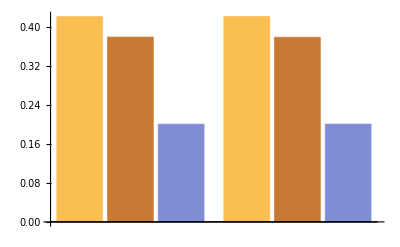

```mathematica
r𝒩=5000000;
n=measurements3[r𝒩,r𝒫];
BarChart[{r𝒫,n/r𝒩}]
```

#### Setting up MLE

```mathematica
ϵ={ϵ1,ϵ2,ϵ3};
n={n1,n2,n3};
Clear[𝒩]
```

```mathematica
D[Sum[-n[[i]] ϵ[[i]]/θ,{i,3}]-𝒩 Log[Ζ[θ,ϵ,kb]],θ]
```

-(𝒩 ((ⅇ^(-ϵ1/(kb θ)) ϵ1)/(kb θ^2)+(ⅇ^(-ϵ2/(kb θ)) ϵ2)/(kb θ^2)+(ⅇ^(-ϵ3/(kb θ)) ϵ3)/(kb θ^2)))/(ⅇ^(-ϵ1/(kb θ))+ⅇ^(-ϵ2/(kb θ))+ⅇ^(-ϵ3/(kb θ)))+(n1 ϵ1)/θ^2+(n2 ϵ2)/θ^2+(n3 ϵ3)/θ^2

```mathematica
mle[meas_,ϵ_,kb_:1]:=Module[
{𝒩,d,f},
𝒩=Total[meas];
d=Length[meas];
f[θ_]:=-(𝒩 Sum[(ⅇ^(-ϵ[[i]]/(kb θ)) ϵ[[i]])/(kb θ^2),{i,d}])/Sum[ⅇ^(-ϵ[[i]]/(kb θ)),{i,d}]+Sum[(meas[[i]] ϵ[[i]])/(kb θ^2),{i,d}];
θ/.NSolve[f[θ]==0,θ,Reals][[1]]
]
mle::usage="mle[meas,ϵ,kb] returns the mle temperature estimate based on the measurement vector meas which contains counts of energy measurements in either of the d energies stored in ϵ";
```

#### Test MLE

```mathematica
f[θ_,kb_:1]:=-(r𝒩 Sum[(ⅇ^(-rϵ[[i]]/(kb θ)) rϵ[[i]])/(kb θ^2),{i,3}])/Sum[ⅇ^(-rϵ[[i]]/(kb θ)),{i,3}]+Sum[(n[[i]] rϵ[[i]])/(kb θ^2),{i,3}]
```

```mathematica
{θ/.NSolve[f[θ]==0,θ,Reals][[1]],rT}//AbsoluteTiming
```

{0.19673,{0.733665,0.732942}}

```mathematica
mleT=mle[n,rϵ]//AbsoluteTiming
```

{0.024076,0.733665}

```mathematica
{100 Abs[mleT[[2]]-rT]/rT,Abs[mleT[[2]]-rT]}
```

{0.0986618,0.000723134}

#### Test: CRB

```mathematica
out=ParallelTable[
{i,mle[measurements3[i,r𝒫],rϵ]}
,{i,10^#&/@Range[3,8]},{j,30}]
```

{{{1000,1.09929},{1000,1.03121},{1000,0.837503},{1000,0.935525},{1000,0.936782},{1000,0.994642},{1000,1.05641},{1000,0.889276},{1000,1.02481},{1000,0.931926},{1000,1.12606},{1000,0.903319},{1000,1.12136},{1000,1.05049},{1000,0.856637},{1000,0.927425},{1000,0.998542},{1000,0.802355},{1000,1.07558},{1000,0.90156},{1000,0.860912},{1000,0.988499},{1000,0.841084},{1000,0.950674},{1000,0.816832},{1000,1.02613},{1000,1.15318},{1000,0.888706},{1000,1.03065},{1000,0.984153}},{{10000,0.956392},{10000,0.986756},{10000,1.01067},{10000,1.0329},{10000,0.989739},{10000,0.978288},{10000,1.01038},{10000,0.967371},{10000,0.972572},{10000,0.94698},{10000,0.950497},{10000,1.01518},{10000,0.936499},{10000,0.981669},{10000,0.979623},{10000,0.952135},{10000,0.983808},{10000,0.940322},{10000,0.976307},{10000,0.96863},{10000,0.964916},{10000,0.928322},{10000,1.01753},{10000,0.95613},{10000,1.00335},{10000,0.993073},{10000,0.991053},{10000,0.987017},{10000,1.01881},{10000,0.960471}},{{100000,0.966592},{100000,0.981706},{100000,0.961397},{100000,1.00613},{100000,0.983829},{100000,0.977626},{100000,0.980495},{100000,0.988889},{100000,0.97712},{100000,0.989893},{100000,0.986869},{100000,0.979591},{100000,0.993347},{100000,0.980634},{100000,0.986374},{100000,0.987634},{100000,0.983573},{100000,0.986838},{100000,0.983915},{100000,0.96379},{100000,0.98261},{100000,0.980348},{100000,0.972095},{100000,0.988003},{100000,0.979774},{100000,0.997144},{100000,1.0033},{100000,0.977035},{100000,0.982408},{100000,0.980107}},{{1000000,0.979021},{1000000,0.984494},{1000000,0.978393},{1000000,0.982337},{1000000,0.987278},{1000000,0.989108},{1000000,0.985529},{1000000,0.980923},{1000000,0.982349},{1000000,0.982408},{1000000,0.981516},{1000000,0.979501},{1000000,0.983042},{1000000,0.981506},{1000000,0.981718},{1000000,0.979018},{1000000,0.98608},{1000000,0.98148},{1000000,0.984186},{1000000,0.982702},{1000000,0.986656},{1000000,0.97954},{1000000,0.981798},{1000000,0.980643},{1000000,0.982496},{1000000,0.981779},{1000000,0.986518},{1000000,0.982424},{1000000,0.9909},{1000000,0.98918}},{{10000000,0.982701},{10000000,0.981815},{10000000,0.983337},{10000000,0.982616},{10000000,0.982822},{10000000,0.983366},{10000000,0.982645},{10000000,0.983135},{10000000,0.983},{10000000,0.981838},{10000000,0.982778},{10000000,0.983723},{10000000,0.980565},{10000000,0.982981},{10000000,0.983054},{10000000,0.983077},{10000000,0.982925},{10000000,0.981637},{10000000,0.982071},{10000000,0.981673},{10000000,0.981043},{10000000,0.982084},{10000000,0.981937},{10000000,0.984805},{10000000,0.982672},{10000000,0.982075},{10000000,0.982026},{10000000,0.981596},{10000000,0.981638},{10000000,0.981241}},{{100000000,0.9825},{100000000,0.982679},{100000000,0.981881},{100000000,0.982101},{100000000,0.982759},{100000000,0.982501},{100000000,0.982753},{100000000,0.982765},{100000000,0.982579},{100000000,0.982225},{100000000,0.982328},{100000000,0.982601},{100000000,0.982561},{100000000,0.982387},{100000000,0.982713},{100000000,0.982403},{100000000,0.982354},{100000000,0.982502},{100000000,0.982001},{100000000,0.982239},{100000000,0.982595},{100000000,0.982372},{100000000,0.982336},{100000000,0.982714},{100000000,0.982215},{100000000,0.982138},{100000000,0.98231},{100000000,0.982182},{100000000,0.982184},{100000000,0.982366}}}

```mathematica
qfi=Sum[r𝒫[[i]](D[Log[ⅇ^(-rϵ/(kb θ))/Total[ⅇ^(-rϵ/(kb θ))]]/.kb->1,θ]^2)[[i]],{i,3}]/.θ->rT
```

0.115724

```mathematica
{10^#,1/(10^# qfi)}&/@Range[3,8]
```

{{1000,0.00864125},{10000,0.000864125},{100000,0.0000864125},{1000000,8.64125×10^-6},{10000000,8.64125×10^-7},{100000000,8.64125×10^-8}}

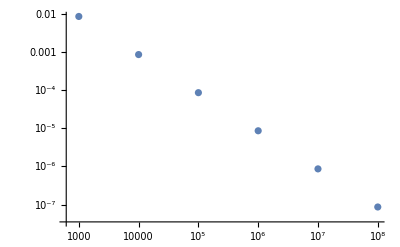

```mathematica
ListLogLogPlot[{10^#,1/(10^# qfi)}&/@Range[3,8]]
```

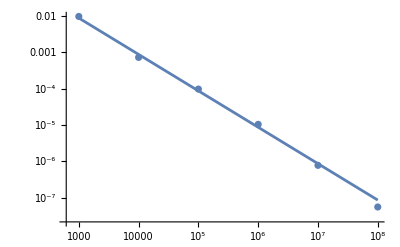

```mathematica
Show[ListLogLogPlot[Partition[Riffle[10^#&/@Range[3,8],Variance[Transpose[out[[#]]][[2]]]&/@Range[1,6]],2]],ListLogLogPlot[{10^#,1/(10^# qfi)}&/@Range[3,8],Joined->True]]
```

```mathematica
{mle[n,rϵ],rT}
```

{0.285092,0.284835}

```mathematica
n
```

{2159035,1652032,1188933}

### Master equation

```mathematica
J[ω_,γ_,Λ_]:=(γ Λ^2 ω)/(ω^2+Λ^2)

J::usage="J[ω,γ,Λ] evaluates the Ohmic spectral density with Lorentz-Drude cutoff at frequency ω";
```

```mathematica
Γ[ω_,T_,γ_,Λ_,ℏ_:1,kb_:1]:=2J[ω,γ,Λ](1+1/(ⅇ^((ℏ ω)/(kb T))-1));
Γ::usage="Γ[ω,T,γ,Λ,ℏ,kb] evaluates the decay rate at frequency ω and temperature T for the spectral density J[ω]";
```

```mathematica
{(Γ[1,0.1,10^-3,10^2,1,1]+10^-2 Γ[1,1,10^-3,10^2,1,1]-Γ[1,0.1,10^-3,10^2,1,1])/Γ[1,0.1,10^-3,10^2,1,1] 100,Γ[1,0.1,10^-3,10^2,1,1]+10^-2 Γ[1,1,10^-3,10^2,1,1],Γ[1,0.1,10^-3,10^2,1,1]}//N
```

{1.5819,0.00203153,0.00199989}

```mathematica
{Teff[1,0.1,1,10^-2,10^-3,10^2,1,1]//N,Teff[1,0.1,1,0,10^-3,10^2,1,1]//N}
```

{0.194007,0.1}

#### Effective temperature of a transition from decay rates

```mathematica
Teff[ω_,T_,Tp_,α_,γ_:10^-3,Λ_:10^2,ℏ_:1,kb_:1]:=-ω (Log[(Γ[-ω,T,γ,Λ,ℏ,kb]+α Γ[-ω,Tp,γ,Λ,ℏ,kb])/(Γ[ω,T,γ,Λ,ℏ,kb]+α Γ[ω,Tp,γ,Λ,ℏ,kb])])^-1
Teff::usage="Teff[ω,T,Tp,α,γ,Λ,ℏ,kb] returns the effective temperature of a transition coupled to both a bath at T and a parasitic bath at Tp (the latter coupling with a strength weakened by a factor of α)";
```

```mathematica
FullSimplify[-ω (Log[(Γ[-ω,T,γ,Λ,ℏ,kb]+α Γ[-ω,x T,γ,Λ,ℏ,kb])/(Γ[ω,T,γ,Λ,ℏ,kb]+α Γ[ω,x T,γ,Λ,ℏ,kb])])^-1/.{ℏ->1,kb->1},Assumptions->{{ω,T,x,α}∈PositiveReals}]
```

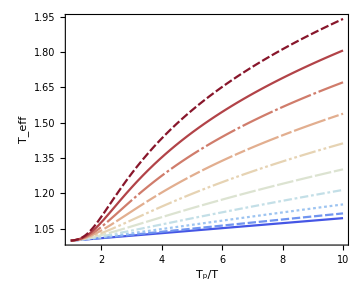

```mathematica
Plot[Evaluate@(Teff[#,1,x ,10^-2]&/@Range[10]),{x,1,10},PlotStyle->ColorData["ThermometerColors"]/@(Range[1,10]/10),AxesLabel->Automatic,Frame->True,Axes->False,AspectRatio->0.8,FrameLabel->{"T_p/T","T_eff"},FrameStyle->Directive["Helvetica",14],PlotTheme->"Monochrome"]//Quiet
```

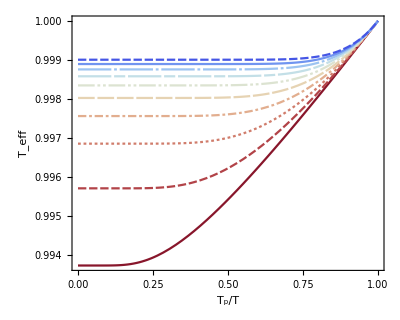

```mathematica
Plot[Evaluate@(Teff[#,1,x ,10^-2]&/@Range[10]),{x,10^-3,1},PlotStyle->ColorData[{"ThermometerColors","Reverse"}]/@(Range[0,10]/10),AxesLabel->Automatic,Frame->True,Axes->False,AspectRatio->0.8,FrameLabel->{"T_p/T","T_eff"},FrameStyle->Directive["Helvetica",14],PlotTheme->"Monochrome"]//Quiet
```

### Setting up master equation for a single qubit

```mathematica
{σx,σy,σz}=(PauliMatrix[#]&/@Range[3]);
{σp,σm}=1/2{σx+ⅈ σy,σx-ⅈ σy};
σ13=KroneckerProduct[{0,0,1},{1,0,0}];
σ23=KroneckerProduct[{0,1,0},{1,0,0}];
A={σm,σp};
A23={σ23,σ23†};
A13={σ13,σ13†};
H2[ϵ_]:=ϵ/2 σz;
H2::usage="H2[ϵ] returns the Hamiltonian of a two-level system with energy gap ϵ";
H3[ϵ13_,ϵ23_]:=({{ϵ13, 0, 0}, {0, ϵ13-ϵ23, 0}, {0, 0, 0}});
H3::usage="H3[ϵ13,ϵ23] returns the Hamiltonian of a three-level Λ-system with gaps ϵ13 and ϵ23";
comm[A_,B_,s_:-1]:=A.B+s B.A
```

```mathematica
steadystate2[ω_,T_,Tp_,α_,γ_:10^-3,Λ_:10^2,kb_:1,ℏ_:1]:=
Module[
{Ω,ρ},
Ω={ω,-ω};
ρ=Table[ϱ0[i,j],{i,2},{j,2}];
ρ/.Solve[Append[Thread[Equal[Flatten[-ⅈ comm[H2[ℏ ω],ρ,-1]+Sum[(Γ[Ω[[i]],T,γ,Λ]+α Γ[Ω[[i]],Tp,γ,Λ])(A[[i]].ρ.A[[i]]†-1/2 comm[A[[i]]†.A[[i]],ρ,1]),{i,2}]],0]],Total[Diagonal[ρ]]==1],Flatten[ρ]][[1]]//Chop
]
steadystate2::usage="steadystate2[ω,T,Tp,α,γ,Λ,kb,ℏ] returns the steady state of a two-level system on a two baths (one parasitic with coupling strength attenuated by a factor α and at temperature Tp)";
```

```mathematica
Ω={ω,-ω};
ρ=Table[ϱ0[i,j],{i,2},{j,2}];
```

```mathematica
ρ//MatrixForm
```

(ϱ0[1,1] | ϱ0[1,2]
ϱ0[2,1] | ϱ0[2,2])

```mathematica
ρ=({{ϱ0[1,1], 0}, {0, ϱ0[2,2]}});
Sum[(Γ[Ω[[i]],T]+α Γ[Ω[[i]],Tp])(A[[i]].ρ.A[[i]]†-1/2 comm[A[[i]]†.A[[i]],ρ,1]),{i,2}]//FullSimplify//MatrixForm
```

(-((Γ[ω,T]+α Γ[ω,Tp]) ϱ0[1,1])+(Γ[-ω,T]+α Γ[-ω,Tp]) ϱ0[2,2] | 0
0 | (Γ[ω,T]+α Γ[ω,Tp]) ϱ0[1,1]-(Γ[-ω,T]+α Γ[-ω,Tp]) ϱ0[2,2])

```mathematica
-Γeff[ω] ϱ0[1,1]+Γeff[-ω] ϱ0[2,2]
```

```mathematica
Γeff[ω] ϱ0[1,1]-Γeff[-ω] ϱ0[2,2]
```

```mathematica
evolution2[init_,ω_,T_,Tp_,α_,γ_:10^-3,Λ_:10^2,kb_:1,ℏ_:1]:=
Module[
{Ω,ρ,ϱ,solution,ℒ},
Ω={ω,-ω};
ϱ[t_]=Table[ϱ0[i,j][t],{i,2},{j,2}];
ρ=Table[ϱ0[i,j],{i,2},{j,2}];
ℒ[X_]:=-ⅈ comm[H2[ℏ ω],X,-1]+Sum[(Γ[Ω[[i]],T,γ,Λ]+α Γ[Ω[[i]],Tp,γ,Λ])(A[[i]].X.A[[i]]†-1/2 comm[A[[i]]†.A[[i]],X,1]),{i,2}];
solution=DSolve[Join[Flatten[Table[ϱ'[t][[i,j]]==ℒ[ϱ[t]][[i,j]],{i,2},{j,2}]]//Chop,Flatten[Table[ϱ[0][[i,j]]==init[[i,j]],{i,2},{j,2}]]//Chop],Flatten[ρ],t];
Return[ϱ[t]/.solution⟦1⟧]
]
evolution2::usage="evolution2[init,ω,T,Tp,α,γ,Λ,kb,ℏ] returns the dynamics of a two-level system on two baths (one parasitic with coupling strength attenuated by a factor α and at temperature Tp)";
```

```mathematica
steadystate3[ω13_,ω23_,T_,Tp_,α_,γ_:10^-3,Λ_:10^2,kb_:1,ℏ_:1]:=
Module[
{Ω13,Ω23,ρ},
Ω13={ω13,-ω13};
Ω23={ω23,-ω23};
ρ=Table[ϱ0[i,j],{i,3},{j,3}];
ρ/.Solve[Append[Thread[Equal[Flatten[-ⅈ comm[H3[ℏ ω13,ℏ ω23],ρ,-1]+Sum[(Γ[Ω23[[i]],T,γ,Λ]+α Γ[Ω23[[i]],Tp,γ,Λ])(A23[[i]].ρ.A23[[i]]†-1/2 comm[A23[[i]]†.A23[[i]],ρ,1]),{i,2}]+Sum[Γ[Ω13[[i]],T,γ,Λ](A13[[i]].ρ.A13[[i]]†-1/2 comm[A13[[i]]†.A13[[i]],ρ,1]),{i,2}]],0]],Total[Diagonal[ρ]]==1],Flatten[ρ]][[1]]//Chop
]
steadystate3::usage="steadystate3[ω13,ω23,T,Tp,α,γ,Λ,kb,ℏ] returns the steady state of a three-level Λ-system on a two baths. The main one coupled to 1-3 and 2-3 and a parasitic one coupled to 2-3 with coupling attenuated by a factor of α";
```

```mathematica
ClearAll[ϱ,ρ]
```

```mathematica
evolution3[init_,ω13_,ω23_,T_,Tp_,α_,γ_:10^-3,Λ_:10^2,kb_:1,ℏ_:1]:=
Module[
{Ω13,Ω23,ρ,ϱ,solution,ℒ},
Ω13={ω13,-ω13};
Ω23={ω23,-ω23};
ϱ=Table[ϱ0[i,j],{i,3},{j,3}];
ρ[t_]=Table[ϱ0[i,j][t],{i,3},{j,3}];
ℒ[X_]:=-ⅈ comm[H3[ℏ ω13,ℏ ω23],X,-1]+Sum[(Γ[Ω23[[i]],T,γ,Λ]+α Γ[Ω23[[i]],Tp,γ,Λ])(A23[[i]].X.A23[[i]]†-1/2 comm[A23[[i]]†.A23[[i]],X,1]),{i,2}]+Sum[Γ[Ω13[[i]],T,γ,Λ](A13[[i]].X.A13[[i]]†-1/2 comm[A13[[i]]†.A13[[i]],X,1]),{i,2}];
solution=DSolve[Join[Flatten[Table[ρ'[t][[i,j]]==ℒ[ρ[t]][[i,j]],{i,3},{j,3}]]//Chop,Flatten[Table[ρ[0][[i,j]]==init[[i,j]],{i,3},{j,3}]]//Chop],Flatten[ϱ],t];
Return[ρ[t]/.solution⟦1⟧]
]
evolution3::usage="evolution3[init,ω13,ω23,T,Tp,α,γ,Λ,kb,ℏ] returns the dynamics of a three-level λ-system on two baths (one parasitic with coupling strength attenuated by a factor α and at temperature Tp)";
```

#### Tests

```mathematica
randomPureState[n_]:=RandomComplex[{-1-I,1+I},n]//Normalize
singleStateDensityMatrix[state_]:=Outer[Times,state,Conjugate[state]]

randomPureDensityMatrix[n_]:=singleStateDensityMatrix@randomPureState@n
```

```mathematica
Teff[(rϵ[[2]]-rϵ[[1]]),(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]]),10^-2,10^-3,10^2]
```

0.422452

```mathematica
10rT
```

0.209105

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
```

```mathematica
r𝒫ness=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,0.01]],#1>#2&]
```

{0.621278,0.378722}

```mathematica
r𝒫eq={p[1,rϵ,rT],p[2,rϵ,rT]}
```

{0.731059,0.268941}

```mathematica
Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,0,10^-3,10^2]],#1>#2&]
```

{0.731059,0.268941}

```mathematica
Diagonal[sol0[5 10^4]]
```

{0.268941,0.731059}

```mathematica
r𝒫ness=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,0.01]],#1>#2&]
Diagonal[sol[5 10^4]]
```

{0.621278,0.378722}

{0.378722,0.621278}

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
sol[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,0.01,10^-3,10^2];
sol0[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,0,10^-3,10^2];
r𝒫ness=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,0.01]],#1>#2&];
r𝒫eq=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,0]],#1>#2&];
```

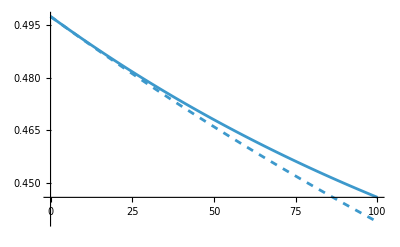

```mathematica
Show[Plot[{sol[t][[1,1]]},{t,0,10^2}],Plot[{sol0[t][[1,1]]},{t,0,10^2},PlotStyle->{Dashed}],PlotRange->All]
```

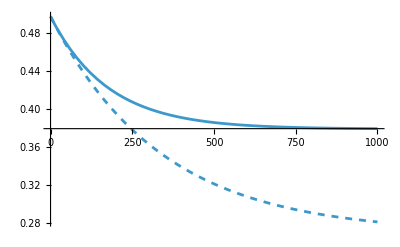

```mathematica
Show[Plot[{sol[t][[1,1]]},{t,0,10^3}],Plot[{sol0[t][[1,1]]},{t,0,10^3},PlotStyle->{Dashed}],PlotRange->All]
```

```mathematica
teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,0.01];
```

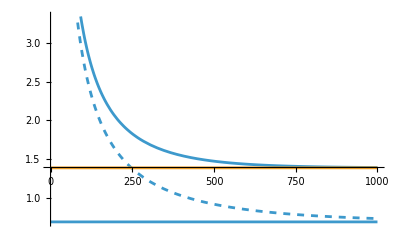

```mathematica
Show[Plot[-(rϵ[[2]]-rϵ[[1]])/Log[(sol[t][[1,1]])/(sol[t][[2,2]])],{t,0,10^3}],Plot[-(rϵ[[2]]-rϵ[[1]])/Log[(sol0[t][[1,1]])/(sol0[t][[2,2]])],{t,0,10^3},PlotStyle->{Dashed}],Show[Plot[{rT,teff},{t,0,10^3}]],PlotRange->All]
```

```mathematica
r𝒩=10^5;
nness=measurements2[r𝒩,r𝒫ness]
neq=measurements2[r𝒩,r𝒫eq]
```

{62093,37907}

{72917,27083}

```mathematica
{mle[nness,rϵ],mle[neq,rϵ],rT}
```

{0.914664,0.455752,0.451384}

```mathematica
Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,0.01]
```

0.911927

### Kullback–Leibler divergence

#### Test

```mathematica
{ρ00,ρ11}={({{0, 0}, {0, 1}}),({{1, 0}, {0, 0}})};
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
sol[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,0.01,10^-3,10^2];
sol0[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,0,10^-3,10^2];
r𝒫ness=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,0.01]],#1>#2&];
r𝒫eq=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,0]],#1>#2&];
```

```mathematica
{Pness[2,1][t_],Pness[2,2][t_]}=Diagonal[evolution2[r𝒫ness[[1]]ρ00,rϵ[[2]]-rϵ[[1]],rT,rTp,0.01]];
```

```mathematica
{Pness[1,1][t_],Pness[1,2][t_]}=Diagonal[evolution2[r𝒫ness[[2]]ρ11,rϵ[[2]]-rϵ[[1]],rT,rTp,0.01]];
```

```mathematica
{Peq[2,1][t_],Peq[2,2][t_]}=Diagonal[evolution2[r𝒫ness[[1]]ρ00,rϵ[[2]]-rϵ[[1]],rT,rTp,0]];
```

```mathematica
{Peq[1,1][t_],Peq[1,2][t_]}=Diagonal[evolution2[r𝒫ness[[2]]ρ11,rϵ[[2]]-rϵ[[1]],rT,rTp,0]];
```

```mathematica
r𝒫init=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0]],#1>#2&];
```

```mathematica
{Pness[2,1][t_],Pness[2,2][t_]}=Diagonal[evolution2[r𝒫init[[1]]ρ00,rϵ[[2]]-rϵ[[1]],rT,rTp,0.01]];
{Pness[1,1][t_],Pness[1,2][t_]}=Diagonal[evolution2[r𝒫init[[2]]ρ11,rϵ[[2]]-rϵ[[1]],rT,rTp,0.01]];
{Peq[2,1][t_],Peq[2,2][t_]}=Diagonal[evolution2[r𝒫init[[1]]ρ00,rϵ[[2]]-rϵ[[1]],rT,rTp,0]];
{Peq[1,1][t_],Peq[1,2][t_]}=Diagonal[evolution2[r𝒫init[[2]]ρ11,rϵ[[2]]-rϵ[[1]],rT,rTp,0]];
```

```mathematica
dKL[A_,B_]:=Sum[A[[i,j]]Log[A[[i,j]]/B[[i,j]]],{i,Dimensions[A][[1]]},{j,Dimensions[A][[2]]}]
dKL::usage="dKL[A,B] gives the Kullback-Liebler divergence between joint probability distributions A_ij and B_ij";
```

```mathematica
distance[t_]:=dKL[Table[Pness[i,j][t],{i,2},{j,2}],Table[Peq[i,j][t],{i,2},{j,2}]]
```

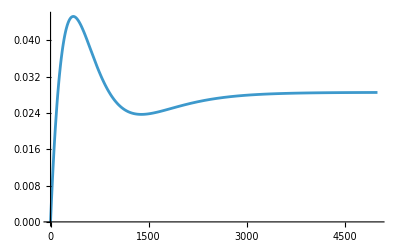

```mathematica
Plot[distance[t],{t,0,5000},PlotRange->All]
```

#### Finding the temperature that minimises the distance (as a function of time)

```mathematica
{ρ00,ρ11}={({{0, 0}, {0, 1}}),({{1, 0}, {0, 0}})};
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={RandomReal[],100(rϵ[[2]]-rϵ[[1]])}//Sort;
teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,0.01];
init=randomPureDensityMatrix[2];
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
{rT,rTp,teff}
```

{0.58531,13.5766,0.714385}

```mathematica
{ρ00,ρ11}={({{0, 0}, {0, 1}}),({{1, 0}, {0, 0}})};
teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,0.01];
Pness[time_]:={Diagonal[evolution2[init[[1,1]]ρ11,rϵ[[2]]-rϵ[[1]],rT,rTp,0.01]],Diagonal[evolution2[init[[2,2]]ρ00,rϵ[[2]]-rϵ[[1]],rT,rTp,0.01]]}/.t->time;
Peq[time_,θ_]:={Diagonal[evolution2[init[[1,1]]ρ11,rϵ[[2]]-rϵ[[1]],θ,rTp,0]],Diagonal[evolution2[init[[2,2]]ρ00,rϵ[[2]]-rϵ[[1]],θ,rTp,0]]}/.t->time;
f[t_,θ_]:=dKL[Pness[t],Peq[t,θ]];
```

```mathematica
out=ParallelTable[{ⅇ^time,θ,f[ⅇ^time,θ]},{time,Log[1],Log[1000],(Log[1000]-Log[1])/30},{θ,0.5teff,1.5teff,(1.5teff-0.5teff)/30}];
```

```mathematica
ListPlot3D[Partition[Flatten[out],3]]
```

-Graphics3D-

```mathematica
{rT,rTp,teff}
```

{0.58531,13.5766,0.714385}

```mathematica
θest=ParallelTable[{ⅇ^time,θ/.NMinimize[{Chop[f[ⅇ^time,θ]],10^-3 rTp<θ<rTp},θ][[2]]},{time,Log[0.01],Log[10^4],(Log[10^4]-Log[0.01])/30}];
```

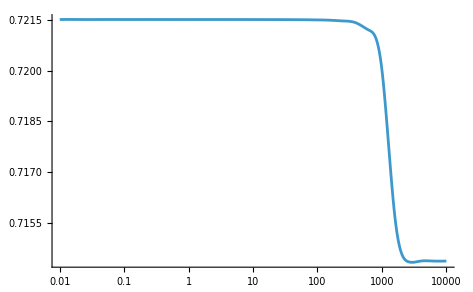

```mathematica
Show[ListLogLinearPlot[θest,PlotRange->All,Joined->True,InterpolationOrder->3]]
```

```mathematica
rTp
```

13.5766

```mathematica
rT
```

0.58531

```mathematica
{10^-3 rTp,rT}
```

{0.0135766,0.58531}

```mathematica
SetOptions[$FrontEnd,"WindowMargins"->Automatic]
```

## Ed

```mathematica
defaultPlotColors=Cases[#,_?ColorQ,All]&["DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme[Automatic,Plot])]
```

{RGBColor[0.24, 0.6, 0.8],RGBColor[0.95, 0.627, 0.1425],RGBColor[0.455, 0.7, 0.21],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.578, 0.51, 0.85],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.4, 0.64, 1.],RGBColor[1., 0.75, 0.],RGBColor[0.8, 0.4, 0.76],RGBColor[0.637, 0.65, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

### Faster sample measurements

```mathematica
measurementsn[𝒩_,𝒫_,n_]:=Count[RandomChoice[𝒫->Range[1,n],𝒩],#]&/@Range[1,n]
measurementsn::usage="measurementsn[𝒩,𝒫,n] simulates 𝒩 energy measurements of an n-level spectrum with probabilities 𝒫 and returns n-dimensional list with the outcome count for each state.";
```

```mathematica
rϵ=RandomReal[{},3]//Sort;
rT=RandomReal[{}];
r𝒫={p[1,rϵ,rT],p[2,rϵ,rT],p[3,rϵ,rT]};
r𝒩=10^5;
```

```mathematica
measurements3[r𝒩,r𝒫]//AbsoluteTiming
measurementsn[r𝒩,r𝒫,3]//AbsoluteTiming
```

{0.188732,{47917,27387,24696}}

{0.0183685,{47715,27475,24542}}

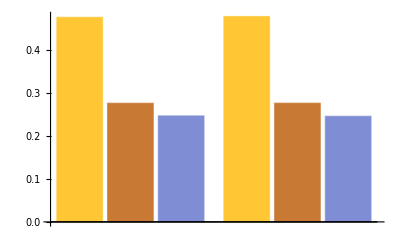

```mathematica
BarChart[{r𝒫,measurementsn[r𝒩,r𝒫,3]/r𝒩}]
```

```mathematica
nmeasurements2[𝒩_,𝒫_]:=RandomVariate[MultinomialDistribution[𝒩,𝒫]];
```

```mathematica
nmeasurements2[r𝒩,Diagonal[ρQubitExact[10,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]]//AbsoluteTiming
```

{0.0004754,{493449,506551}}

```mathematica
Sort[measurementsn[r𝒩,Sort[Diagonal[ρQubitExact[10,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]],#1>#2&],2],#2>#1&]//AbsoluteTiming
```

{0.124306,{494740,506283}}

```mathematica
nmeasurements2PM[𝒩_,𝒫joint_]:=ArrayReshape[RandomVariate[MultinomialDistribution[𝒩,Flatten@𝒫joint]],{2,2}]
```

```mathematica
?Pness2PMExact
```

```mathematica
rt=20;

r𝒩=10^6;


1/r𝒩 nmeasurements2PM[r𝒩,Pness2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]//N
```

{{0.49167,0.006588},{0.004142,0.4976}}

```mathematica
Pness2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]
```

{{0.490944,0.00655575},{0.00403645,0.498464}}

### Effective temperature

```mathematica
?Teff
```

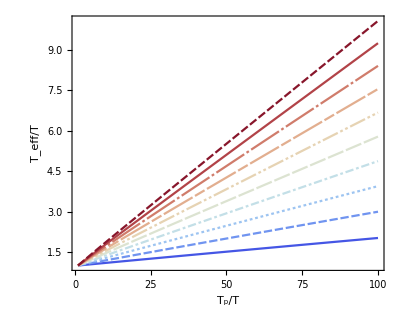

```mathematica
Plot[Evaluate@(Teff[1,1,Tp ,#]&/@(Range[10]/100)),{Tp,1,100},PlotStyle->ColorData["ThermometerColors"]/@(Range[1,10]/10),AxesLabel->Automatic,Frame->True,Axes->False,AspectRatio->0.8,FrameLabel->{"T_p/T","T_eff/T"},FrameStyle->Directive["Helvetica",14],PlotTheme->"Monochrome"]//Quiet
```

```mathematica
Teff[1,1,100 ,0.01]
```

2.02029

Therefore T_eff deviates from T for large α and T_p. If α is small, a large T_p can still have T_eff~T.

### Exact solution to master equation for a qubit

#### Exact solution

```mathematica
{p1[t],p2[t]}/.DSolve[{p1'[t]==-Γp*p1[t]+Γm*p2[t],p2'[t]==+Γp*p1[t]-Γm*p2[t],p1[0]==p1init,p2[0]==p2init}, {p1,p2},t][[1]]
```

{-(-p1init Γm-p2init Γm+ⅇ^(t (-Γm-Γp)) p2init Γm-ⅇ^(t (-Γm-Γp)) p1init Γp)/(Γm+Γp),(ⅇ^(t (-Γm-Γp)) p2init Γm+p1init Γp-ⅇ^(t (-Γm-Γp)) p1init Γp+p2init Γp)/(Γm+Γp)}

```mathematica
{p1[t],p2[t]}/.DSolve[{p1'[t]==-Γp*p1[t]+Γm*p2[t],p2'[t]==+Γp*p1[t]-Γm*p2[t],p1[0]==p1init,p2[0]==p2init}, {p1,p2},t][[1]]//Tr//FullSimplify
```

p1init+p2init

```mathematica
p1Qubit[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=Module[
{Γm=Γ[ω,T,γ,Λ]+α*Γ[ω,Tp,γ,Λ],Γp=Γ[-ω,T,γ,Λ]+α*Γ[-ω,Tp,γ,Λ]},
-(-p1init Γm-p2init Γm+ⅇ^(t (-Γm-Γp)) p2init Γm-ⅇ^(t (-Γm-Γp)) p1init Γp)/(Γm+Γp)]
p2Qubit[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=Module[
{Γm=Γ[ω,T,γ,Λ]+α*Γ[ω,Tp,γ,Λ],Γp=Γ[-ω,T,γ,Λ]+α*Γ[-ω,Tp,γ,Λ]},
(ⅇ^(t (-Γm-Γp)) p2init Γm+p1init Γp-ⅇ^(t (-Γm-Γp)) p1init Γp+p2init Γp)/(Γm+Γp)]
```

```mathematica
-(-p1init Γm-p2init Γm+ⅇ^(t (-Γm-Γp)) p2init Γm-ⅇ^(t (-Γm-Γp)) p1init Γp)/(Γm+Γp)/.{p1init->1,p2init->0}//Simplify
-(-p1init Γm-p2init Γm+ⅇ^(t (-Γm-Γp)) p2init Γm-ⅇ^(t (-Γm-Γp)) p1init Γp)/(Γm+Γp)/.{p1init->0,p2init->1}//Simplify
```

(Γm+ⅇ^(-t (Γm+Γp)) Γp)/(Γm+Γp)

(Γm-ⅇ^(-t (Γm+Γp)) Γm)/(Γm+Γp)

```mathematica
(ⅇ^(t (-Γm-Γp)) p2init Γm+p1init Γp-ⅇ^(t (-Γm-Γp)) p1init Γp+p2init Γp)/(Γm+Γp)/.{p1init->1,p2init->0}//Simplify
(ⅇ^(t (-Γm-Γp)) p2init Γm+p1init Γp-ⅇ^(t (-Γm-Γp)) p1init Γp+p2init Γp)/(Γm+Γp)/.{p1init->0,p2init->1}//Simplify
```

(Γp-ⅇ^(-t (Γm+Γp)) Γp)/(Γm+Γp)

(ⅇ^(-t (Γm+Γp)) Γm+Γp)/(Γm+Γp)

```mathematica
p1QubitExact2[t_,Γm_,Γp_,p1init_,p2init_]:=-(-p1init Γm-p2init Γm+ⅇ^(t (-Γm-Γp)) p2init Γm-ⅇ^(t (-Γm-Γp)) p1init Γp)/(Γm+Γp)
p2QubitExact2[t_,Γm_,Γp_,p1init_,p2init_]:=(ⅇ^(t (-Γm-Γp)) p2init Γm+p1init Γp-ⅇ^(t (-Γm-Γp)) p1init Γp+p2init Γp)/(Γm+Γp)
```

```mathematica
ρQubitExact2[t_,Γm_,Γp_,p1init_,p2init_]:=({{p1QubitExact2[t,Γm,Γp,p1init,p2init], 0}, {0, p2QubitExact2[t,Γm,Γp,p1init,p2init]}})
```

```mathematica
D[p1Qubit[t,ω,T,Tp,α,p1init,p2init,γ,Λ],t]==-(Γ[-ω,T,γ,Λ]+α*Γ[-ω,Tp,γ,Λ])*p1Qubit[t,ω,T,Tp,α,p1init,p2init,γ,Λ]+(Γ[ω,T,γ,Λ]+α*Γ[ω,Tp,γ,Λ])*p2Qubit[t,ω,T,Tp,α,p1init,p2init,γ,Λ]//Simplify

D[p2Qubit[t,ω,T,Tp,α,p1init,p2init,γ,Λ],t]==(Γ[-ω,T,γ,Λ]+α*Γ[-ω,Tp,γ,Λ])*p1Qubit[t,ω,T,Tp,α,p1init,p2init,γ,Λ]-
(Γ[ω,T,γ,Λ]+α*Γ[ω,Tp,γ,Λ])*p2Qubit[t,ω,T,Tp,α,p1init,p2init,γ,Λ]//Simplify
```

True

True

```mathematica
ρQubitExact[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=({{p2Qubit[t,ω,T,Tp,α,p1init,p2init,γ,Λ], 0}, {0, p1Qubit[t,ω,T,Tp,α,p1init,p2init,γ,Λ]}})
```

Now for the steady state

```mathematica
ρSteadyQubitExact[ω_,T_,Tp_,α_,γ_:10^-3,Λ_:10^2]:=Module[
{Γm=Γ[ω,T,γ,Λ]+α*Γ[ω,Tp,γ,Λ],Γp=Γ[-ω,T,γ,Λ]+α*Γ[-ω,Tp,γ,Λ]},
({{Γp/(Γm+Γp), 0}, {0, Γm/(Γm+Γp)}})]
```

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
nα=0.01;
init=randomPureDensityMatrix[2];


ρQubitExact[10^6,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]
ρSteadyQubitExact[rϵ[[2]]-rϵ[[1]],rT,rTp,nα]
```

General::munfl: Exp[-6013.03] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{0.378722+0. ⅈ,0},{0,0.621278+0. ⅈ}}

{{0.378722,0},{0,0.621278}}

Now for some plots

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
nα=0.01;

(*nΓm=Γ[rϵ[[2]]-rϵ[[1]],rT,10^-3,10^2]+nα*Γ[rϵ[[2]]-rϵ[[1]],rTp,10^-3,10^2];
nΓp=Γ[-(rϵ[[2]]-rϵ[[1]]),rT,10^-3,10^2]+nα*Γ[-(rϵ[[2]]-rϵ[[1]]),rTp,10^-3,10^2];*)

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
sol[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,10^-3,10^2];
sol0[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,0,10^-3,10^2];
r𝒫ness=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,nα]],#1>#2&];
r𝒫eq=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,0]],#1>#2&];
```

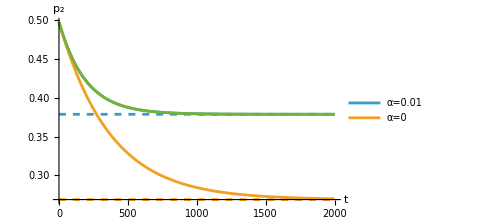
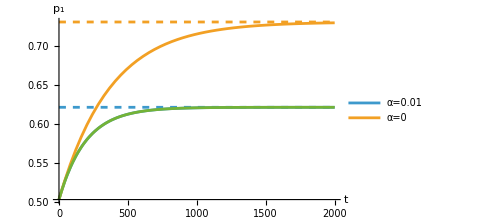

```mathematica
tmax=2*10^3;

{Plot[{sol[t][[1,1]],sol0[t][[1,1]],r𝒫ness[[2]],r𝒫eq[[2]],p2Qubit[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,0,tmax},PlotRange->Automatic,PlotLegends->{"α=0.01","α=0"},PlotStyle->{defaultPlotColors[[1]],defaultPlotColors[[2]],{defaultPlotColors[[1]],Dashed},{defaultPlotColors[[2]],Dashed},defaultPlotColors[[3]]},AxesLabel->{"t","p_2"},ImageSize->Medium],

Plot[{sol[t][[2,2]],sol0[t][[2,2]],r𝒫ness[[1]],r𝒫eq[[1]],p1Qubit[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,0,tmax},PlotRange->Automatic,PlotLegends->{"α=0.01","α=0"},PlotStyle->{defaultPlotColors[[1]],defaultPlotColors[[2]],{defaultPlotColors[[1]],Dashed},{defaultPlotColors[[2]],Dashed},defaultPlotColors[[3]]},AxesLabel->{"t","p_1"},ImageSize->Medium]}
```

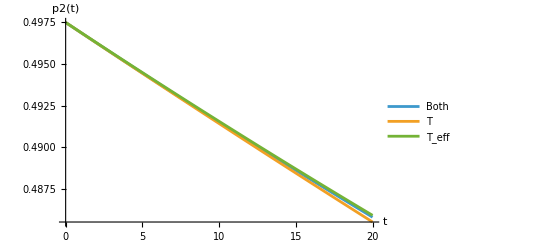

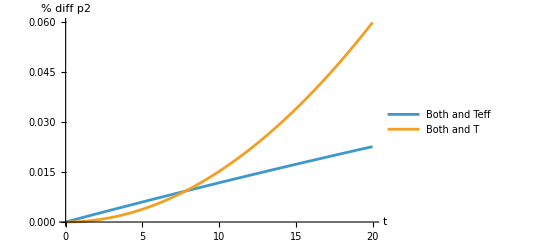

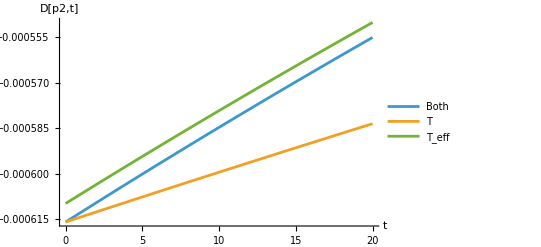

```mathematica
teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];


Plot[{p2Qubit[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],p2Qubit[t,rϵ[[2]]-rϵ[[1]],rT,rTp,0,init[[2,2]],init[[1,1]]],p2Qubit[t,rϵ[[2]]-rϵ[[1]],teff,rTp,0,init[[2,2]],init[[1,1]]]},{t,0,20},PlotLegends->{"Both","T","T_eff"},AxesLabel->{"t","p2(t)"}]

Plot[{Abs[(p2Qubit[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]-p2Qubit[t,rϵ[[2]]-rϵ[[1]],teff,1,0,init[[2,2]],init[[1,1]]])/p2Qubit[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]*100],Abs[(p2Qubit[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]-p2Qubit[t,rϵ[[2]]-rϵ[[1]],rT,1,0,init[[2,2]],init[[1,1]]])/p2Qubit[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]*100]},{t,0,20},PlotLegends->{"Both and Teff","Both and T"},AxesLabel->{"t","% diff p2"}]


Plot[{D[p2Qubit[time,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],time]/.time->t,D[p2Qubit[time,rϵ[[2]]-rϵ[[1]],rT,rTp,0,init[[2,2]],init[[1,1]]],time]/.time->t,D[p2Qubit[time,rϵ[[2]]-rϵ[[1]],teff,rTp,0,init[[2,2]],init[[1,1]]],time]/.time->t},{t,0,20},PlotLegends->{"Both","T","T_eff"},AxesLabel->{"t","D[p2,t]"}]
```

```mathematica
sol[10]//MatrixForm

ρQubitExact[10,nΓm,nΓp,init[[2,2]],init[[1,1]]]//MatrixForm
```

(0.492909 | 0
0 | 0.507091)

(0.492909 | 0
0 | 0.507091)

```mathematica
sol[1]//Diagonal
sol0[1]//Diagonal
sol0teff[1]//Diagonal
```

{0.497074,0.502926}

{0.497073,0.502927}

{0.497078,0.502922}

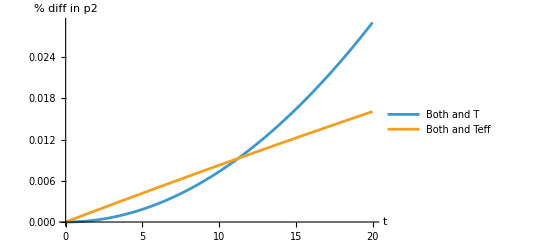

```mathematica
Plot[{{(sol[t][[1,1]]-sol0[t][[1,1]])/(sol[t][[1,1]])*100},{(sol[t][[1,1]]-sol0teff[t][[1,1]])/(-sol[t][[1,1]])*100}},{t,0,20},PlotRange->All,AxesLabel->{"t","% diff in p2"},PlotLegends->{"Both and T","Both and Teff"}]
```

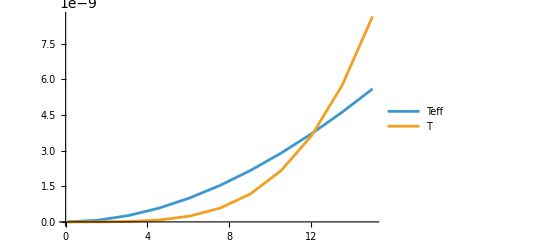

```mathematica
tmin=0.1;
tmax=15;

points=10;
ListLinePlot[{Table[{time,fTest[time,teff]},{time,tmin,tmax,(tmax-tmin)/points}],Table[{time,fTest[time,rT]},{time,tmin,tmax,(tmax-tmin)/points}]},PlotLegends->{"Teff","T"}]
```

#### Test and plots

α=0.01

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
nα=0.01;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
sol[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,10^-3,10^2];
sol0[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,0,10^-3,10^2];
(*sol0[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],teff,rTp,0,10^-3,10^2];*)

r𝒫ness=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,nα]],#1>#2&];
r𝒫eq=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,0]],#1>#2&];
```

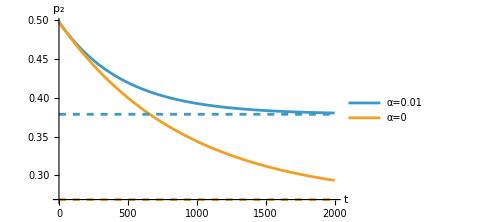
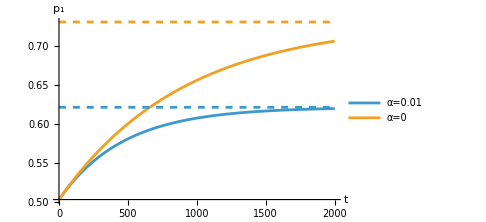

```mathematica
{Plot[{sol[t][[1,1]],sol0[t][[1,1]],r𝒫ness[[2]],r𝒫eq[[2]]},{t,0,2*10^3},PlotRange->Automatic,PlotLegends->{"α=0.01","α=0"},PlotStyle->{defaultPlotColors[[1]],defaultPlotColors[[2]],{defaultPlotColors[[1]],Dashed},{defaultPlotColors[[2]],Dashed}},AxesLabel->{"t","p_2"},ImageSize->Medium],

Plot[{sol[t][[2,2]],sol0[t][[2,2]],r𝒫ness[[1]],r𝒫eq[[1]]},{t,0,2*10^3},PlotRange->Automatic,PlotLegends->{"α=0.01","α=0"},PlotStyle->{defaultPlotColors[[1]],defaultPlotColors[[2]],{defaultPlotColors[[1]],Dashed},{defaultPlotColors[[2]],Dashed}},AxesLabel->{"t","p_1"},ImageSize->Medium]}
```

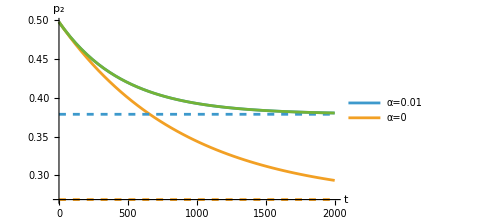

```mathematica
Plot[{sol[t][[1,1]],sol0[t][[1,1]],r𝒫ness[[2]],r𝒫eq[[2]],1/(Exp[(rϵ[[2]]-rϵ[[1]])/teff]+1)+(init[[1,1]]-1/(Exp[(rϵ[[2]]-rϵ[[1]])/teff]+1))*Exp[-(Γ[rϵ[[2]]-rϵ[[1]],rT,10^-3,10^2]+Γ[-(rϵ[[2]]-rϵ[[1]]),rT,10^-3,10^2]+nα*Γ[rϵ[[2]]-rϵ[[1]],rTp,10^-3,10^2]+nα*Γ[-(rϵ[[2]]-rϵ[[1]]),rTp,10^-3,10^2])*t]},{t,0,2*10^3},PlotRange->Automatic,PlotLegends->{"α=0.01","α=0"},PlotStyle->{defaultPlotColors[[1]],defaultPlotColors[[2]],{defaultPlotColors[[1]],Dashed},{defaultPlotColors[[2]],Dashed},{defaultPlotColors[[3]]}},AxesLabel->{"t","p_2"},ImageSize->Medium]
```

```mathematica
(init[[1,1]]-1/(Exp[(rϵ[[2]]-rϵ[[1]])/teff]+1))*-(Γ[rϵ[[2]]-rϵ[[1]],rT,10^-3,10^2]+Γ[-(rϵ[[2]]-rϵ[[1]]),rT,10^-3,10^2]+nα*Γ[rϵ[[2]]-rϵ[[1]],rTp,10^-3,10^2]+nα*Γ[-(rϵ[[2]]-rϵ[[1]]),rTp,10^-3,10^2])/10^-3
```

-0.348378

```mathematica
(init[[1,1]]*(Γ[rϵ[[2]]-rϵ[[1]],rT,10^-3,10^2]+nα*Γ[rϵ[[2]]-rϵ[[1]],rTp,10^-3,10^2])-(init[[2,2]]*(Γ[-(rϵ[[2]]-rϵ[[1]]),rT,10^-3,10^2]+nα*Γ[-(rϵ[[2]]-rϵ[[1]]),rTp,10^-3,10^2])))/10^-3
```

0.348378

```mathematica
Γ[rϵ[[2]]-rϵ[[1]],rTp,10^-3,10^2]*steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2][[1,1]]-Γ[-(rϵ[[2]]-rϵ[[1]]),rTp,10^-3,10^2]*steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2][[2,2]]
```

-1.38778×10^-17

```mathematica
(init[[1,1]]*Γ[rϵ[[2]]-rϵ[[1]],rT,10^-3,10^2]-init[[2,2]]*Γ[-(rϵ[[2]]-rϵ[[1]]),rT,10^-3,10^2])/10^-3
```

0.348378

```mathematica
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];

sol[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,10^-3,10^2];
sol0[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,0,10^-3,10^2];

sol0teff[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],teff,rTp,0,10^-3,10^2];


D[sol[t][[2,2]],t]/10^-3/.t->0.1
D[sol0[t][[2,2]],t]/10^-3/.t->0.1
D[sol0teff[t][[2,2]],t]/10^-3/.t->0.1
```

0.468008

0.468096

0.463376

```mathematica
sol[t][[2,2]]-sol0[t][[2,2]]/.t->0.1
sol[t][[2,2]]-sol0teff[t][[2,2]]/.t->0.1
```

-4.43118×10^-9

4.63375×10^-7

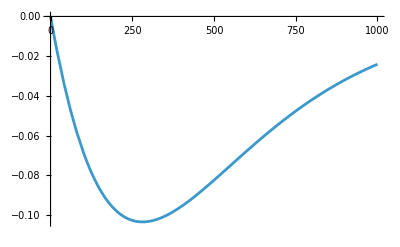

```mathematica
Plot[{(sol[t][[1,1]]-sol0teff[t][[1,1]])/(sol[t][[1,1]])*100},{t,0,1000},PlotRange->All]
```

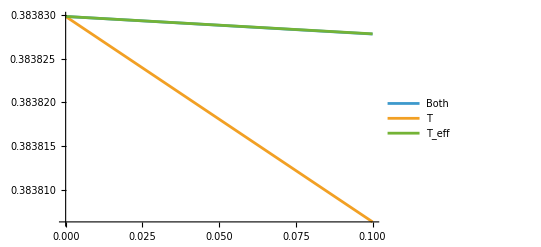

```mathematica
Plot[{sol[t][[1,1]],sol0[t][[1,1]],sol0teff[t][[1,1]]},{t,0,0.1},PlotLegends->{"Both","T","T_eff"},PlotRange->Automatic]
```

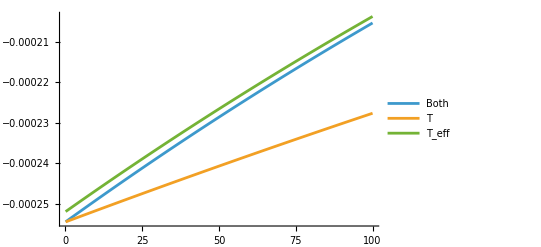

```mathematica
Plot[{D[sol[time][[1,1]],time]/.time->t,D[sol0[time][[1,1]],time]/.time->t,D[sol0teff[time][[1,1]],time]/.time->t},{t,0.1,100},PlotLegends->{"Both","T","T_eff"}]
```

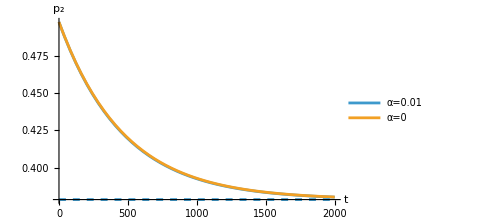
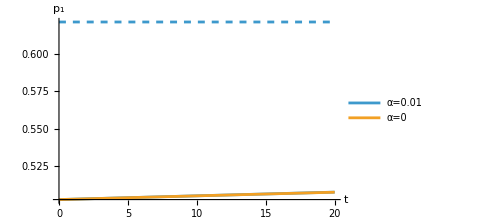

```mathematica
{Plot[{sol[t][[1,1]],sol0teff[t][[1,1]],r𝒫ness[[2]]},{t,0,2*10^3},PlotRange->Automatic,PlotLegends->{"α=0.01","α=0"},PlotStyle->{defaultPlotColors[[1]],defaultPlotColors[[2]],{defaultPlotColors[[1]],Dashed},{defaultPlotColors[[2]],Dashed}},AxesLabel->{"t","p_2"},ImageSize->Medium],

Plot[{sol[t][[2,2]],sol0teff[t][[2,2]],r𝒫ness[[1]]},{t,0,2*10^1},PlotRange->Automatic,PlotLegends->{"α=0.01","α=0"},PlotStyle->{defaultPlotColors[[1]],defaultPlotColors[[2]],{defaultPlotColors[[1]],Dashed},{defaultPlotColors[[2]],Dashed}},AxesLabel->{"t","p_1"},ImageSize->Medium]}
```

```mathematica
D[sol[t][[2,2]],t]/10^-3/.t->0
D[sol0[t][[2,2]],t]/10^-3/.t->0

D[sol[t][[1,1]],t]/10^-3/.t->0
D[sol0[t][[1,1]],t]/10^-3/.t->0
```

0.348378

0.344929

-0.348378

-0.344929

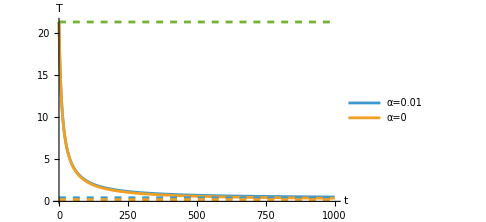
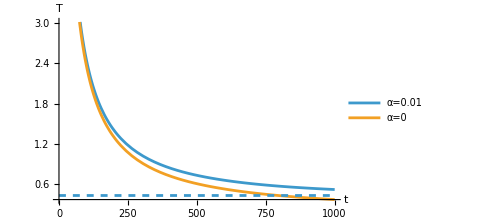

```mathematica
tmax=1000;
{Show[Plot[{-(rϵ[[2]]-rϵ[[1]])/Log[(sol[t][[1,1]])/(sol[t][[2,2]])],-(rϵ[[2]]-rϵ[[1]])/Log[(sol0[t][[1,1]])/(sol0[t][[2,2]])]},{t,0,tmax},PlotRange->All,PlotLegends->{"α=0.01","α=0"}],Plot[{teff,rT,rTp},{t,0,tmax},PlotRange->All,PlotStyle->Dashed],AxesLabel->{"t","T"},ImageSize->Medium],

Show[Plot[{-(rϵ[[2]]-rϵ[[1]])/Log[(sol[t][[1,1]])/(sol[t][[2,2]])],-(rϵ[[2]]-rϵ[[1]])/Log[(sol0[t][[1,1]])/(sol0[t][[2,2]])]},{t,0,tmax},PlotRange->Automatic,PlotLegends->{"α=0.01","α=0"}],Plot[{teff,rT,rTp},{t,0,tmax},PlotRange->All,PlotStyle->Dashed],AxesLabel->{"t","T"},ImageSize->Medium]}
```

```mathematica
{rT,rTp,teff}
```

{0.213228,21.3228,0.430783}

α=2 and random initial state

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
nα=2;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
init=randomPureDensityMatrix[2];
sol[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,10^-3,10^2];
sol0[t_]=evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,0,10^-3,10^2];
r𝒫ness=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,nα]],#1>#2&];
r𝒫eq=Sort[Diagonal[steadystate2[rϵ[[2]]-rϵ[[1]],rT,rTp,0]],#1>#2&];
```

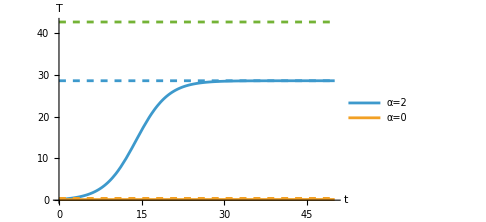
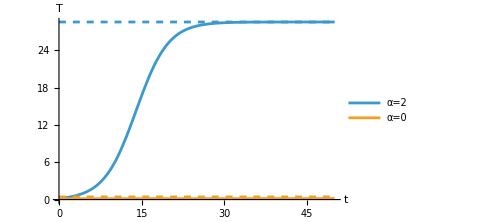

```mathematica
tmax=50;
{Show[Plot[{-(rϵ[[2]]-rϵ[[1]])/Log[(sol[t][[1,1]])/(sol[t][[2,2]])],-(rϵ[[2]]-rϵ[[1]])/Log[(sol0[t][[1,1]])/(sol0[t][[2,2]])]},{t,0,tmax},PlotRange->All,PlotLegends->{"α=2","α=0"}],Plot[{teff,rT,rTp},{t,0,tmax},PlotRange->All,PlotStyle->Dashed],AxesLabel->{"t","T"},ImageSize->Medium],

Show[Plot[{-(rϵ[[2]]-rϵ[[1]])/Log[(sol[t][[1,1]])/(sol[t][[2,2]])],-(rϵ[[2]]-rϵ[[1]])/Log[(sol0[t][[1,1]])/(sol0[t][[2,2]])]},{t,0,tmax},PlotRange->Automatic,PlotLegends->{"α=2","α=0"}],Plot[{teff,rT,rTp},{t,0,tmax},PlotRange->All,PlotStyle->Dashed],AxesLabel->{"t","T"},ImageSize->Medium]}
```

```mathematica
{rT,rTp,teff}
```

{0.143874,14.3874,9.64337}

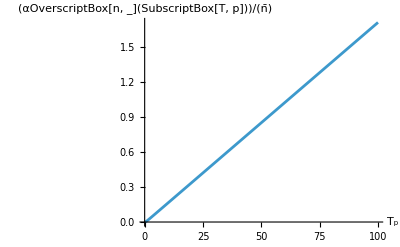

```mathematica
Plot[(0.01(ⅇ^(1/1)-1))/(ⅇ^(1/Tp)-1),{Tp,0,100},AxesLabel->{"T_p","(α OverscriptBox[n, _] (SubscriptBox[T, p]))/(n̄)"}]
```

#### Showing ℒ_Teff(ρ_T'(∞))=ℒ_T(ρ_T'(∞))

```mathematica
Ω={ω,-ω};
LTeff[ρ_]:=Sum[(Γ[Ω[[i]],T,γ,Λ]+α Γ[Ω[[i]],Tp,γ,Λ])(A[[i]].ρ.A[[i]]†-(1/2)comm[A[[i]]†.A[[i]],ρ,1]),{i,2}]
LT[ρ_]:=Sum[(Γ[Ω[[i]],T,γ,Λ])(A[[i]].ρ.A[[i]]†-(1/2)comm[A[[i]]†.A[[i]],ρ,1]),{i,2}]
LTp[ρ_]:=Sum[(α Γ[Ω[[i]],Tp,γ,Λ])(A[[i]].ρ.A[[i]]†-(1/2)comm[A[[i]]†.A[[i]],ρ,1]),{i,2}]
```

```mathematica
ρπTp=({{p[1,{ω,0},Tp], 0}, {0, p[2,{ω,0},Tp]}});


LTeff[ρπTp]//FullSimplify//MatrixForm
LTeff[ρπTp]==LT[ρπTp]//Simplify
```

((γ Λ^2 ω (-1+Coth[ω/(2 T)] Tanh[ω/(2 Tp)]))/(Λ^2+ω^2) | 0
0 | (γ Λ^2 ω (1-Coth[ω/(2 T)] Tanh[ω/(2 Tp)]))/(Λ^2+ω^2))

True

```mathematica
LTeff[LTeff[ρπTp]]//FullSimplify
LTeff[LTeff[ρπTp]]==LT[LT[ρπTp]]+LTp[LT[ρπTp]]//Simplify
```

{{(16 ⅇ^(ω/T) γ^2 Λ^4 ω^2 Csch[ω/Tp] (α Cosh[ω/(2 Tp)] Sinh[ω/(2 T)]+Cosh[ω/(2 T)] Sinh[ω/(2 Tp)]) Sinh[((-T+Tp) ω)/(2 T Tp)])/((-1+ⅇ^(ω/T))^2 (Λ^2+ω^2)^2),0},{0,-(16 ⅇ^(ω/T) γ^2 Λ^4 ω^2 Csch[ω/Tp] (α Cosh[ω/(2 Tp)] Sinh[ω/(2 T)]+Cosh[ω/(2 T)] Sinh[ω/(2 Tp)]) Sinh[((-T+Tp) ω)/(2 T Tp)])/((-1+ⅇ^(ω/T))^2 (Λ^2+ω^2)^2)}}

True

```mathematica
(*ρ0=({{ϱ0[1,1], 0}, {0, ϱ0[2,2]}});*)
ρ0=Table[ϱ[i,j],{i,2},{j,2}];
LTeff[ρ0]==LT[ρ0]+α*LTp[ρ0]//Simplify
```

{{(2 (-1+α) α γ Λ^2 ω (ⅇ^(ω/Tp) ϱ[1,1]-ϱ[2,2]))/((-1+ⅇ^(ω/Tp)) (Λ^2+ω^2)),((1+ⅇ^(ω/Tp)) (-1+α) α γ Λ^2 ω ϱ[1,2])/((-1+ⅇ^(ω/Tp)) (Λ^2+ω^2))},{((1+ⅇ^(ω/Tp)) (-1+α) α γ Λ^2 ω ϱ[2,1])/((-1+ⅇ^(ω/Tp)) (Λ^2+ω^2)),-(2 (-1+α) α γ Λ^2 ω (ⅇ^(ω/Tp) ϱ[1,1]-ϱ[2,2]))/((-1+ⅇ^(ω/Tp)) (Λ^2+ω^2))}}=={{0,0},{0,0}}

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];
```

```mathematica
p[1,{ω,0},Tp]+(γ Λ^2 ω (-1+Coth[ω/(2 T)] Tanh[ω/(2 Tp)]))/(Λ^2+ω^2)*t/.{ω->rϵ[[2]]-rϵ[[1]],T->rT,Tp->rTp,γ->10^-3,Λ->10^2,t->1}
(evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,0.01,10^-3,10^2]/.t->1)[[1,1]]
(evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,0,10^-3,10^2]/.t->1)[[1,1]]
(evolution2[init,rϵ[[2]]-rϵ[[1]],teff,rTp,0,10^-3,10^2]/.t->1)[[1,1]]
```

0.497073

0.497074

0.497073

0.497078

```mathematica
p[2,{ω,0},Tp]+(γ Λ^2 ω (1-Coth[ω/(2 T)] Tanh[ω/(2 Tp)]))/(Λ^2+ω^2)*t/.{ω->rϵ[[2]]-rϵ[[1]],T->rT,Tp->rTp,γ->10^-3,Λ->10^2,t->1}
(evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,0.01,10^-3,10^2]/.t->1)[[2,2]]
(evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,0,10^-3,10^2]/.t->1)[[2,2]]
(evolution2[init,rϵ[[2]]-rϵ[[1]],teff,rTp,0,10^-3,10^2]/.t->1)[[2,2]]
```

0.502927

0.502926

0.502927

0.502922

### Trying to match decay rates

```mathematica
ClearAll[teff]
Solve[{γ*Γ[ω,T,γ,Λ]+γ*α*Γ[ω,Tp,γ,Λ]==γp Γ[ω,teff,γ,Λ],γ*Γ[-ω,T,γ,Λ]+γ*α*Γ[-ω,Tp,γ,Λ]==γp Γ[-ω,teff,γ,Λ]},{teff,γp}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{teff→ω/Log[(-ⅇ^(ω/T)+ⅇ^(ω/T+ω/Tp)-ⅇ^(ω/Tp) α+ⅇ^(ω/T+ω/Tp) α)/(-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α)],γp→(1+α) γ}}

```mathematica
Solve[{Γ[ω,T,γ,Λ]+Γ[ω,Tp,γ*α,Λ]== Γ[ω,teff,γp,Λ],Γ[-ω,T,γ,Λ]+Γ[-ω,Tp,γ*α,Λ]== Γ[-ω,teff,γp,Λ]},{teff,γp}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{teff→ω/Log[(-ⅇ^(ω/T)+ⅇ^(ω/T+ω/Tp)-ⅇ^(ω/Tp) α+ⅇ^(ω/T+ω/Tp) α)/(-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α)],γp→(1+α) γ}}

```mathematica
Teff[ω,T,Tp,α,γ,Λ]//FullSimplify
```

-ω/Log[(1-ⅇ^(ω/Tp)+α-ⅇ^(ω/T) α)/(ⅇ^(ω/T)+ⅇ^(ω/Tp) α-ⅇ^((1/T+1/Tp) ω) (1+α))]

```mathematica
Log[(-ⅇ^(ω/T)+ⅇ^(ω/T+ω/Tp)-ⅇ^(ω/Tp) α+ⅇ^(ω/T+ω/Tp) α)/(-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α)]==Log[((1-ⅇ^(ω/Tp)+α-ⅇ^(ω/T) α)/(ⅇ^(ω/T)+ⅇ^(ω/Tp) α-ⅇ^((1/T+1/Tp) ω) (1+α)))^-1]//Simplify
```

True

```mathematica
?Γ
```

```mathematica
γ(1+1/(ⅇ^(ω/T)-1))/.ω->-ω//Simplify
```

γ/(1-ⅇ^(ω/T))

```mathematica
Solve[{γ ω(1+1/(ⅇ^(ω/T)-1))+α*γ*ω(1+1/(ⅇ^(ω/Tp)-1))==γp*ω(1+1/(ⅇ^(ω/teff2)-1)),γ*ω*1/(ⅇ^(ω/T)-1)+α*γ*ω*1/(ⅇ^(ω/Tp)-1)==γp*ω 1/(ⅇ^(ω/teff2)-1)},{teff2,γp}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{teff2→ω/Log[(-ⅇ^(ω/T)+ⅇ^(ω/T+ω/Tp)-ⅇ^(ω/Tp) α+ⅇ^(ω/T+ω/Tp) α)/(-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α)],γp→(1+α) γ}}

```mathematica
ω/Log[(-ⅇ^(ω/T)+ⅇ^(ω/T+ω/Tp)-ⅇ^(ω/Tp) α+ⅇ^(ω/T+ω/Tp) α)/(-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α)]==Teff[ω,T,Tp,α,γ,Λ]//Simplify
```

ω (1/Log[(1-ⅇ^(ω/Tp)+α-ⅇ^(ω/T) α)/(ⅇ^(ω/T)+ⅇ^(ω/Tp) α-ⅇ^((1/T+1/Tp) ω) (1+α))]+1/Log[-(ⅇ^(ω/T)+ⅇ^(ω/Tp) α-ⅇ^((1/T+1/Tp) ω) (1+α))/(-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α)])==0

```mathematica
(1-ⅇ^(ω/Tp)+α-ⅇ^(ω/T) α)/(ⅇ^(ω/T)+ⅇ^(ω/Tp) α-ⅇ^((1/T+1/Tp) ω) (1+α))*(ⅇ^(ω/T)+ⅇ^(ω/Tp) α-ⅇ^((1/T+1/Tp) ω) (1+α))/(-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α)//Simplify
```

-1

### Temperature estimation for a qubit

#### Definitions

```mathematica
dKL1PM[A_,B_]:=Sum[A[[i]]Log[A[[i]]/B[[i]]],{i,Dimensions[A][[1]]}]
dKL1PM::usage="dKL1PM[A,B] gives the Kullback-Liebler divergence between joint probability distributions A_ij and B_ij";
```

```mathematica
Pness1PM[time_]:=Diagonal[evolution2[init,rϵ[[2]]-rϵ[[1]],rT,rTp,nα]]/.t->time;
PModel1PM[time_,θ_]:=Diagonal[evolution2[init,rϵ[[2]]-rϵ[[1]],θ,rTp,0]]/.t->time;
f1PM[t_,θ_]:=dKL1PM[Pness1PM[t],PModel1PM[t,θ]];
```

```mathematica
dKL1PM[Pness1PM[1],PModel1PM[1,2]]//AbsoluteTiming
```

{0.0428925,6.03418×10^-10}

```mathematica
Pness1PMExact[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=Diagonal[ρQubitExact[t,ω,T,Tp,α,p1init,p2init,γ,Λ]]
PModel1PMExact[t_,θ_,ω_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=Diagonal[ρQubitExact[t,ω,θ,1,0,p1init,p2init,γ,Λ]]

dKL1PMExact[t_,θ_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=dKL1PM[Pness1PMExact[t,ω,T,Tp,α,p1init,p2init,γ,Λ],PModel1PMExact[t,θ,ω,p1init,p2init,γ,Λ]]
```

```mathematica
crossEntropy[p_,q_]:=-Sum[p[[i]]*Log[q[[i]]],{i,1,Dimensions[p][[1]]}]

(*MLE objective function (negative log-likelihood)*)
negLogLikelihood1PMExact[t_,θ_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=crossEntropy[Pness1PMExact[t,ω,T,Tp,α,p1init,p2init,γ,Λ],PModel1PMExact[t,θ,ω,p1init,p2init,γ,Λ]]

(*thetaEstMLEExact[t_]:=θ/. Last[NMinimize[{negLogLikelihoodExact[t,θ],10^-3*rT<θ<2*teff},θ]]*)
thetaEstMLE1PMExact[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=θ/. Last[FindMinimum[negLogLikelihood1PMExact[t,θ,ω,T,Tp,α,p1init,p2init,γ,Λ],{θ,teff},Method->"PrincipalAxis",WorkingPrecision->MachinePrecision,AccuracyGoal->6]]
(*thetaEstMLEExact[t_]:=θ/. Last[ FindMinimum[negLogLikelihoodExact[t,θ],{θ,rT,teff}]]*)

(*KL estimate (minimize KL divergence)*)
(*thetaEstKLExact[t_]:=θ/. Last[NMinimize[{klObjectiveExact[t,θ],10^-3*rT<θ<2*teff},θ]]*)
thetaEstKL1PMExact[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=θ/. Last[FindMinimum[dKL1PMExact[t,θ,ω,T,Tp,α,p1init,p2init,γ,Λ],{θ,teff},Method->"PrincipalAxis",WorkingPrecision->MachinePrecision,AccuracyGoal->6]]
(*thetaEstKLExact[t_]:=θ/. Last[FindMinimum[klObjectiveExact[t,θ],{θ,rT,teff}]]*)
```

```mathematica
thetaEstMLE1PMExact[10,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]
```

0.253725

```mathematica
mleGeneral1PM[meas_,model_,θguess_]:=Module[
{f,q},
(*q[θp_]:=model/.θ->θp;*)
q[θ_]:=model;

f[θ_]:=-Sum[meas[[i]] Log[q[θ][[i]]],{i,2}];


θ/. Last[FindMinimum[f[θ],{θ,θguess},WorkingPrecision->MachinePrecision,AccuracyGoal->6]]
(*θ/. NMinimize[{f[θ],θguess/10<θ<2*θguess},θ,AccuracyGoal->6][[2]]*)
]
mleGeneral1PM::usage="mleGeneral1PM returns the mle temperature estimate based on the measurement vector meas which contains counts of energy measurements in either of the d energies stored in ϵ";
```

```mathematica
mleGeneral1PM2[meas_,model_,θguess_]:=Module[
{f,q},

(*q[θp_]:=model/.θ->θp;*)
q[θ_]:=model;

f[θ_]:=-D[Sum[meas[[i]] Log[q[θ][[i]]],{i,2}],θ];


(*θ/.NSolve[Simplify@f[θ]==0,θ][[1]];*)

θ/.FindRoot[Simplify@f[θ],{θ,θguess},AccuracyGoal->5,WorkingPrecision->MachinePrecision][[1]]


]
mleGeneral1PM::usage="mleGeneral1PM returns the mle temperature estimate based on the measurement vector meas which contains counts of energy measurements in either of the d energies stored in ϵ";
```

Two point measurements

```mathematica
Pness2PM[time_]:={Diagonal[init[[1,1]]*evolution2[ρ11,rϵ[[2]]-rϵ[[1]],rT,rTp,nα]],Diagonal[init[[2,2]]*evolution2[ρ00,rϵ[[2]]-rϵ[[1]],rT,rTp,nα]]}/.t->time;
PModel2PM[time_,θ_]:={Diagonal[init[[1,1]]*evolution2[ρ11,rϵ[[2]]-rϵ[[1]],θ,rTp,0]],Diagonal[init[[2,2]]*evolution2[ρ00,rϵ[[2]]-rϵ[[1]],θ,rTp,0]]}/.t->time;
f2PM[t_,θ_]:=dKL[Pness2PM[t],PModel2PM[t,θ]];
```

```mathematica
f2PM[1,2]//AbsoluteTiming
```

{0.0837433,0.00173192}

```mathematica
?ρQubitExact
```

```mathematica
Pness2PMExact[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:={Diagonal[p2init*ρQubitExact[t,ω,T,Tp,α,0,1,γ,Λ]],Diagonal[p1init*ρQubitExact[t,ω,T,Tp,α,1,0,γ,Λ]]};

PModel2PMExact[t_,θ_,ω_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:={Diagonal[p2init*ρQubitExact[t,ω,θ,1,0,0,1,γ,Λ]],Diagonal[p1init*ρQubitExact[t,ω,θ,1,0,1,0,γ,Λ]]};

dKL2PMExact[t_,θ_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=dKL[Pness2PMExact[t,ω,T,Tp,α,p1init,p2init,γ,Λ],PModel2PMExact[t,θ,ω,p1init,p2init,γ,Λ]];
```

```mathematica
dKL2PMExact[1,2,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]//AbsoluteTiming
```

{0.0003993,0.00173192}

```mathematica
crossEntropy2PM[p_,q_]:=-Sum[p[[i,j]]*Log[q[[i,j]]],{i,1,Dimensions[p][[1]]},{j,1,Dimensions[p][[1]]}]


(*MLE objective function (negative log-likelihood)*)
negLogLikelihood2PMExact[t_,θ_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=crossEntropy2PM[Pness2PMExact[t,ω,T,Tp,α,p1init,p2init,γ,Λ],PModel2PMExact[t,θ,ω,p1init,p2init,γ,Λ]]

(*thetaEstMLEExact[t_]:=θ/. Last[NMinimize[{negLogLikelihoodExact[t,θ],10^-3*rT<θ<2*teff},θ]]*)
thetaEstMLE2PMExact[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=θ/. Last[ FindMinimum[negLogLikelihood2PMExact[t,θ,ω,T,Tp,α,p1init,p2init,γ,Λ],{θ,teff},Method->"PrincipalAxis"]]
(*thetaEstMLEExact[t_]:=θ/. Last[ FindMinimum[negLogLikelihoodExact[t,θ],{θ,rT,teff}]]*)

(*KL estimate (minimize KL divergence)*)
(*thetaEstKLExact[t_]:=θ/. Last[NMinimize[{klObjectiveExact[t,θ],10^-3*rT<θ<2*teff},θ]]*)
thetaEstKL2PMExact[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=θ/. Last[FindMinimum[dKL2PMExact[t,θ,ω,T,Tp,α,p1init,p2init,γ,Λ],{θ,teff},Method->"PrincipalAxis"]]
(*thetaEstKLExact[t_]:=θ/. Last[FindMinimum[klObjectiveExact[t,θ],{θ,rT,teff}]]*)
```

```mathematica
mleGeneral2PM[meas_,model_,θguess_]:=Module[
{f,q},

(*q[θp_]:=model/.θ->θp;*)
q[θ_]:=model;

f[θ_]:=-D[Sum[meas[[i]] Log[q[θ][[i]]],{i,4}],θ];


(*θ/.NSolve[Simplify@f[θ]==0,θ][[1]];*)

θ/.FindRoot[Simplify@f[θ],{θ,θguess},AccuracyGoal->3,WorkingPrecision->MachinePrecision][[1]]


]
mleGeneral1PM::usage="mleGeneral1PM returns the mle temperature estimate based on the measurement vector meas which contains counts of energy measurements in either of the d energies stored in ϵ";
```

#### One point measurements (1PM) MLE & min cross entropy & min KL

First let the model be a thermal state at temperature θ

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
nα=0.01;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];
```

```mathematica
tmin=0.1;
tmax=500;
points=10;

(*Sampled measurements for MLE*)
r𝒩=10^5;
measurementsρQubitExact1PM[t_]:=measurementsn[r𝒩,Sort[Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]],#1>#2&],2]



(*Min cross entropy*)
crossEntropy1PMEqModel[t_,θ_]:=crossEntropy[Chop@Pness1PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],Diagonal@ρSteadyQubitExact[rϵ[[2]]-rϵ[[1]],θ,1,0]];

θestcrossEntropyEqModel=ParallelTable[{t,θ/.Last@FindMinimum[crossEntropy1PMEqModel[t,θ],{θ,teff},Method->"PrincipalAxis"]},{t,tmin,tmax,(tmax-tmin)/points}];


(*Min dKL*)
dKL1PMEqModel[t_,θ_]:=dKL1PM[Chop@Pness1PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],Diagonal@ρSteadyQubitExact[rϵ[[2]]-rϵ[[1]],θ,1,0]];
θestdKLEqModel=ParallelTable[{t,θ/.Last@FindMinimum[dKL1PMEqModel[t,θ],{θ,teff},Method->"PrincipalAxis"]},{t,tmin,tmax,(tmax-tmin)/points}];
```

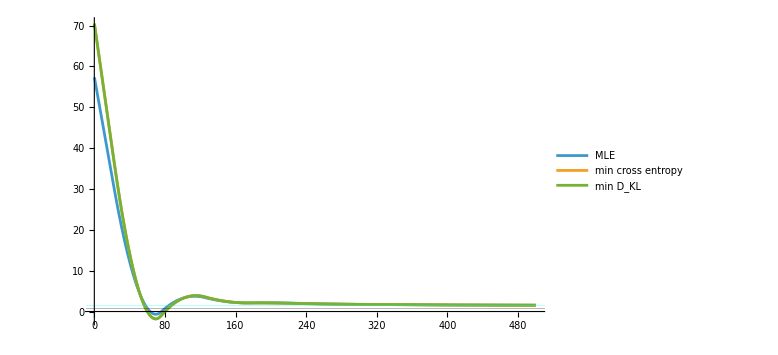

```mathematica
ListLinePlot[{ParallelTable[{t,mle[measurementsρQubitExact1PM[t],rϵ]},{t,tmin,tmax,(tmax-tmin)/points}],θestcrossEntropyEqModel,θestdKLEqModel},InterpolationOrder->2,PlotRange->All,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},PlotLegends->{"MLE","min cross entropy","min D_KL"},ImageSize->Large]
```

Try for a random initial condition

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
nα=0.01;
init=randomPureDensityMatrix[2];

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];
```

```mathematica
tmin=0.1;
tmax=1000/rT;
points=10;


(*Sampled measurements for MLE*)
r𝒩=10^5;
measurementsρQubitExact1PM[t_]:=measurementsn[r𝒩,Sort[Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]],#1>#2&],2]



(*Min cross entropy*)
crossEntropy1PMEqModel[t_,θ_]:=crossEntropy[Chop@Pness1PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],Diagonal@ρSteadyQubitExact[rϵ[[2]]-rϵ[[1]],θ,1,0]];

θestcrossEntropyEqModel=ParallelTable[{t,θ/.Last@FindMinimum[crossEntropy1PMEqModel[t,θ],{θ,teff},Method->"PrincipalAxis"]},{t,tmin,tmax,(tmax-tmin)/points}];


(*Min dKL*)
dKL1PMEqModel[t_,θ_]:=dKL1PM[Chop@Pness1PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],Diagonal@ρSteadyQubitExact[rϵ[[2]]-rϵ[[1]],θ,1,0]];
θestdKLEqModel=ParallelTable[{t,θ/.Last@FindMinimum[dKL1PMEqModel[t,θ],{θ,teff},Method->"PrincipalAxis"]},{t,tmin,tmax,(tmax-tmin)/points}];
```

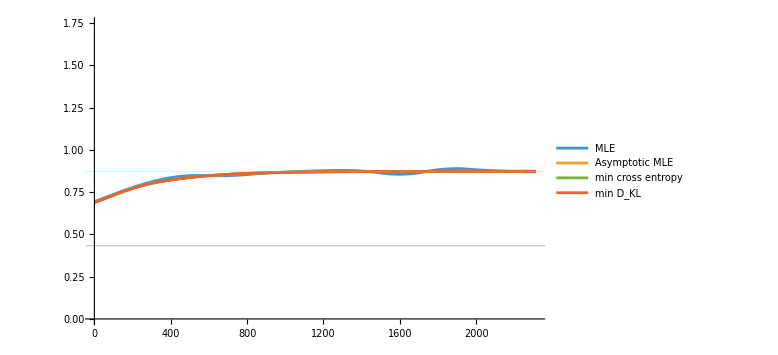

```mathematica
ListLinePlot[{ParallelTable[{t,mle[measurementsρQubitExact1PM[t],rϵ]},{t,tmin,tmax,(tmax-tmin)/points}],ParallelTable[{t,mle[Sort[Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]],#1>#2&],rϵ]},{t,tmin,tmax,(tmax-tmin)/points}],θestcrossEntropyEqModel,θestdKLEqModel},InterpolationOrder->2,PlotRange->{All,{0,2teff}},GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},PlotLegends->{"MLE","Asymptotic MLE","min cross entropy","min D_KL"},ImageSize->Large]
```

```mathematica
{rT,rTp,teff}
```

{0.143633,14.3633,0.290181}

Now the model is a qubit coupled to a single bath at temperature θ at time t

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
nα=0.01;

nγ=10^-3;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];
```

```mathematica
tmin=0.1;
tmax=1000;
points=10;


θestCrossEntropy=ParallelTable[{Exp[t],thetaEstMLE1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

θestKL=ParallelTable[{Exp[t],thetaEstKL1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];
```

```mathematica
points=20;

r𝒩=10^13;

(*meas[t_]:=1/r𝒩 Sort[measurementsn[r𝒩,Sort[Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]],#1>#2&],2],#2>#1&]*)

meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]]

(*meas[t_]:=Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]*)

times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

model1PM[t_]:=PModel1PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]]



θestMLE=ParallelTable[{Exp[t],mleGeneral1PM2[meas[Exp[t]],model1PM[Exp[t]],rT]},{t,times}];

θestCrossEntropy=ParallelTable[{Exp[t],thetaEstMLE1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];

θestKL=ParallelTable[{Exp[t],thetaEstKL1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

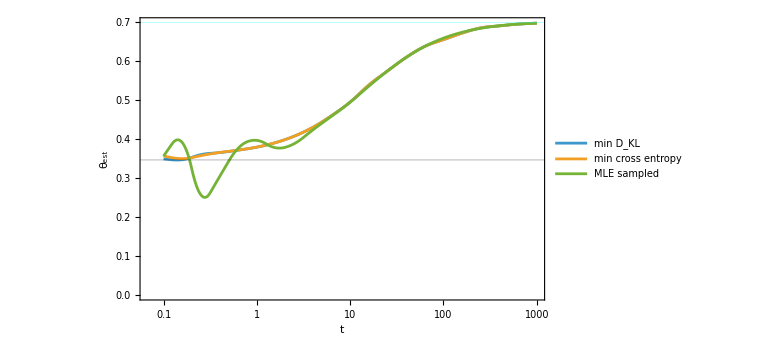

```mathematica
ListLogLinearPlot[{θestKL,θestCrossEntropy,θestMLE},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","MLE sampled"},ImageSize->Large,Joined->True]
```

```mathematica
{rT,rTp,teff}
```

{0.664816,66.4816,6.69225}

```mathematica
nTrials=50;


MLEestimatestest=ParallelTable[mleGeneral1PM2[meas[Exp[t]],model1PM[Exp[t]],rT],{nTrials},{t,times}];

(*MLEestimatestest=ParallelTable[Module[{meas},meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]];mleGeneral1PM2[meas[Exp[t]],model1PM[Exp[t]],rT]]],{nTrials},{t,times}];*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::stop: Further output of The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than `1` digits of working precision to meet these tolerances. will be suppressed during this calculation.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

```mathematica
times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

(*ListLinePlot[Transpose[{Exp[times],Mean/@Transpose@MLEestimatestest}],PlotRange->All]

ListLinePlot[Transpose[{Exp[times],Variance/@Transpose@MLEestimatestest}],PlotRange->Automatic]*)

dataWithErrors=Transpose[{Exp[times],Around@@@Transpose[{Mean[MLEestimatestest],StandardDeviation[MLEestimatestest]}]}];
```

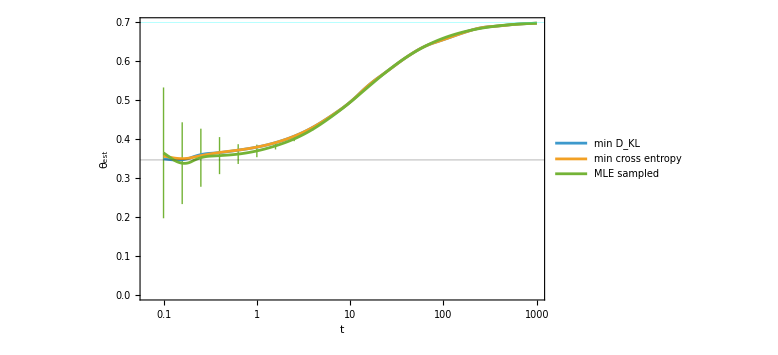

```mathematica
Show[ListLogLinearPlot[{θestKL,θestCrossEntropy,dataWithErrors},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","MLE sampled"},ImageSize->Large,Joined->True]]
```

Now calculate the mean and variance of ntrials MLE estimators

```mathematica
(*MeanMLEestimates[t_,𝒩_,ntrials_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=Module[{meas},
meas[tp_]:=nmeasurements2[𝒩,Diagonal[ρQubitExact[tp,ω,T,Tp,α,p1init,p2init]]];
Mean[ParallelTable[Quiet@mleGeneral1PM2[meas[t],PModel1PMExact[t,θ,ω,p1init,p2init],T],{ntrials}]]

]*)

MeanMLEestimates[t_,𝒩_,ntrials_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=
Mean[ParallelTable[Quiet@mleGeneral1PM2[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,ω,T,Tp,α,p1init,p2init]]],PModel1PMExact[t,θ,ω,p1init,p2init],T],{ntrials}]]

MeanMLEestimates::usage="MeanMLEestimates[t,𝒩,ntrials,ω,T,Tp,α,p1init,p2init,γ:10^-3,Λ:10^2] calculates the average MLE estimators for n trials";


(*VariancesMLEestimates[t_,𝒩_,ntrials_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=Module[{meas},
meas[tp_]:=nmeasurements2[𝒩,Diagonal[ρQubitExact[tp,ω,T,Tp,α,p1init,p2init]]];
Variance[ParallelTable[Quiet@mleGeneral1PM2[meas[t],PModel1PMExact[t,θ,ω,p1init,p2init],T],{ntrials}]]
]*)

VariancesMLEestimates[t_,𝒩_,ntrials_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=
Variance[ParallelTable[Quiet@mleGeneral1PM2[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,ω,T,Tp,α,p1init,p2init]]],PModel1PMExact[t,θ,ω,p1init,p2init],T],{ntrials}]]

VariancesMLEestimates::usage="VariancesMLEestimates[t,𝒩,ntrials,ω,T,Tp,α,p1init,p2init,γ:10^-3,Λ:10^2] calculates the variance MLE estimators for n trials";
```

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
nα=0.01;

nγ=10^-3;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];
```

```mathematica
nTrials=20;

𝒩list=Table[10^i,{i,6,12}];

tlist={5,20,1000};

MeansVsNandtTable=ParallelTable[{𝒩,Quiet@MeanMLEestimates[t,𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]},{t,tlist},{𝒩,𝒩list}];

(*MeansVsNandtTable=ParallelTable[{𝒩,Mean[Table[mleGeneral1PM2[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]],PModel1PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]],rT],{nTrials}]]},{t,tlist},{𝒩,𝒩list}];*)
```

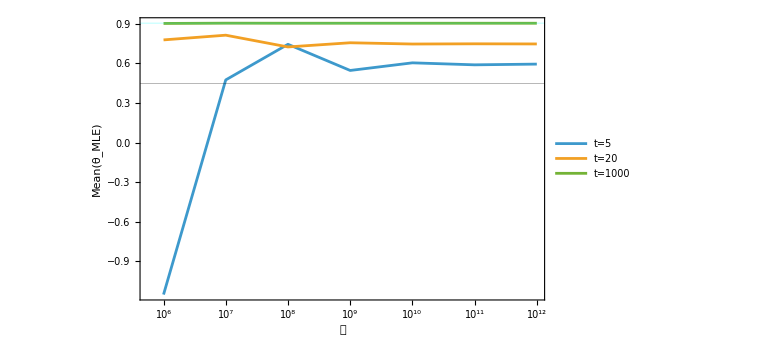

```mathematica
ListLogLinearPlot[MeansVsNandtTable,PlotRange->All,Joined->True,PlotLegends->Table[StringForm["t=``",t],{t,tlist}],GridLines->{{},{{rT,Directive[Thick,Black]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"𝒩","Mean(θ_MLE)"},ImageSize->Large]
```

```mathematica
{rT,teff}
```

{0.447669,0.904421}

Compare average variances to the CFI

```mathematica
CFIExact1PM[θ_,t_,ω_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=Total[(D[PModel1PMExact[t,θp,ω,p1init,p2init,γ,Λ],{θp,1}])^2/PModel1PMExact[t,θp,ω,p1init,p2init,γ,Λ]]/.θp->θ

(*CFIExact1PM2[θ_,t_,ω_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=-Total[PModel1PMExact[t,θp,ω,p1init,p2init,γ,Λ]*(D[Log@PModel1PMExact[t,θp,ω,p1init,p2init,γ,Λ],{θp,2}])]/.θp->θ*)
```

```mathematica
CFIExact1PM[0.1,10,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]]
```

1.82055×10^-8

```mathematica
times={5,20,100};

nTrials=20;

𝒩list=Table[10^i,{i,5,10}];

varsVsNandt=ParallelTable[{𝒩,Quiet@VariancesMLEestimates[t,𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]},{t,times},{𝒩,𝒩list}];

CFIsVsNandt=ParallelTable[{𝒩,1/(𝒩*CFIExact1PM[Quiet@MeanMLEestimates[t,𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ],t,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]])},{t,times},{𝒩,𝒩list}];
```

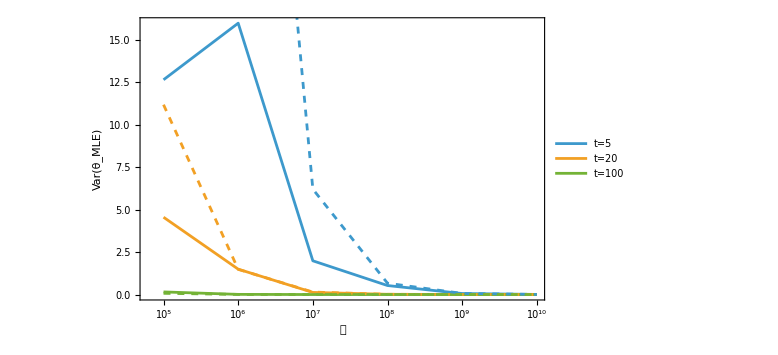

```mathematica
Show[ListLogLinearPlot[varsVsNandt,PlotRange->All,Frame->True,FrameLabel->{"𝒩","Var(θ_MLE)"},PlotLegends->Table[StringForm["t=``",t],{t,times}],Joined->True,ImageSize->Large],

ListLogLinearPlot[CFIsVsNandt,PlotRange->All,Joined->True,PlotStyle->Dashed]]
```

Now select a 𝒩 and mean estimates and errors for MLE

```mathematica
tmin=0.1;
tmax=1000;

points=10;
times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

r𝒩=10^10;
nTrials=50;

(*meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]]*)

(*MeanMLEestimatesList=ParallelTable[Mean[Table[mleGeneral1PM2[meas[Exp[t]],PModel1PMExact[Exp[t],θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]],rT],{nTrials}]],{t,times}];
ErrorsMLEestimatesList=ParallelTable[Quiet[Sqrt[Variance[Table[mleGeneral1PM2[meas[Exp[t]],PModel1PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]],rT],{nTrials}]]]],{t,times}];*)

MeanMLEestimatesList=ParallelTable[Quiet@MeanMLEestimates[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ],{t,times}];
ErrorsMLEestimatesList=ParallelTable[Sqrt[Quiet@VariancesMLEestimates[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]],{t,times}];

MeanMLEWithErrors=Transpose[{Exp[times],Around@@@Transpose[{MeanMLEestimatesList,ErrorsMLEestimatesList}]}];
```

```mathematica
θestCrossEntropy=ParallelTable[{Exp[t],thetaEstMLE1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];

θestKL=ParallelTable[{Exp[t],thetaEstKL1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];
```

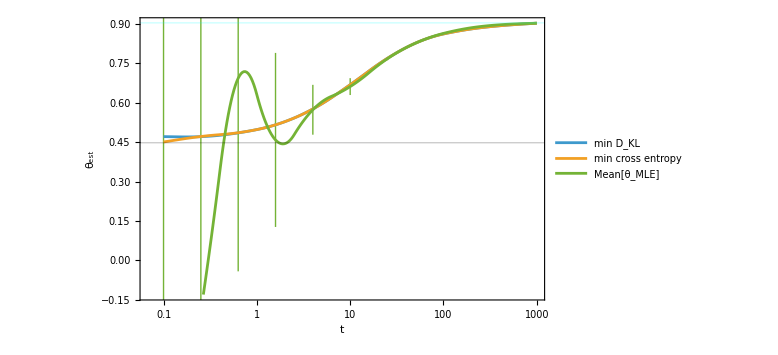

```mathematica
Show[ListLogLinearPlot[{θestKL,θestCrossEntropy,MeanMLEWithErrors},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","Mean[θ_MLE]",PlotLabel->StringForm["𝒩=``",r𝒩]},ImageSize->Large,Joined->True]]
```

```mathematica
points=10;
times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

r𝒩=10^14;
nTrials=50;

MeanMLEestimatesList=ParallelTable[Quiet@MeanMLEestimates[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ],{t,times}];
ErrorsMLEestimatesList=ParallelTable[Quiet[Sqrt[VariancesMLEestimates[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],{t,times}];

MeanMLEWithErrors=Transpose[{Exp[times],Around@@@Transpose[{MeanMLEestimatesList,ErrorsMLEestimatesList}]}];
```

```mathematica
θestCrossEntropy=ParallelTable[{Exp[t],thetaEstMLE1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];

θestKL=ParallelTable[{Exp[t],thetaEstKL1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];
```

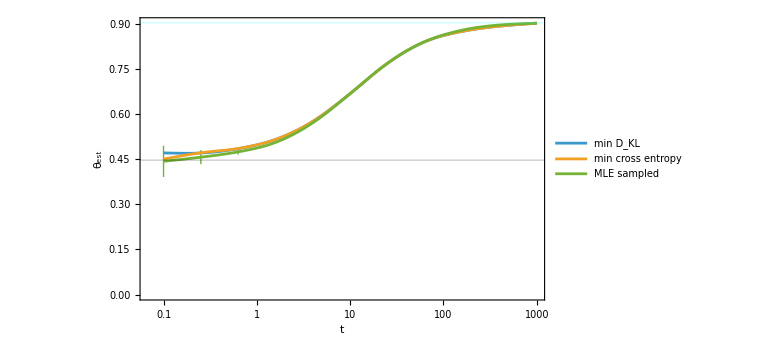

```mathematica
Show[ListLogLinearPlot[{θestKL,θestCrossEntropy,MeanMLEWithErrors},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","MLE sampled"},ImageSize->Large,Joined->True]]
```

#### Two point measurements (2PM) MLE & min cross entropy & min KL

Now the model is a state coupled to a single bath at temperature θ

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
(*init=randomPureDensityMatrix[2];*)
nα=0.01;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];

tmin=0.1;
tmax=1000/rT;
points=10;
(*θestEq=ParallelTable[{t,θ/.NMinimize[{Chop[dKL1PMExact[t,θ,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]],rT/2<θ<rTp},θ][[2]]},{t,tmin,tmax,(tmax-tmin)/points}];*)
θestEqTPM=ParallelTable[{t,θ/.Last@FindMinimum[dKL2PMExact[t,θ,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],{θ,teff},Method->"PrincipalAxis"]},{t,tmin,tmax,(tmax-tmin)/points}];

θestMLETPM=ParallelTable[{t,thetaEstMLE2PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,tmin,tmax,(tmax-tmin)/points}];

θestKLTPM=ParallelTable[{t,thetaEstKL2PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,tmin,tmax,(tmax-tmin)/points}];
```

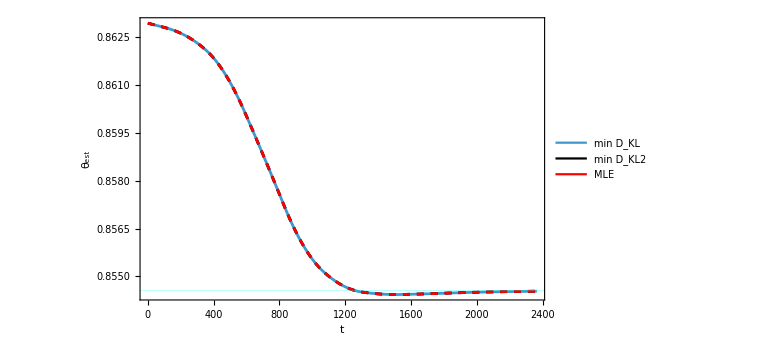

```mathematica
colours={defaultPlotColors[[1]],Black,Red};

Legended[Show[ListLinePlot[θestEqTPM,InterpolationOrder->2,PlotRange->All,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotStyle->defaultPlotColors[[1]]],

ListPlot[θestMLETPM,PlotRange->All,Joined->True,InterpolationOrder->2,PlotStyle->{Black,Dashed}],
ListPlot[θestKLTPM,PlotRange->All,Joined->True,InterpolationOrder->2,PlotStyle->{Red,Dashed}],ImageSize->Large],LineLegend[colours,{"min D_KL","min D_KL2","MLE"}]]
```

```mathematica
{rT,rTp,teff}
```

{0.588202,58.8202,1.18834}

```mathematica
(θ/.Last@FindMinimum[dKL2PMExact[1,θ,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],{θ,teff},Method->"PrincipalAxis"])-θ/.Last@FindMinimum[dKL2PMExact[2000,θ,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],{θ,teff},Method->"PrincipalAxis"]
```

0.0116428

```mathematica
θ/.Last@FindMinimum[dKL2PMExact[1,θ,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],{θ,teff},Method->"PrincipalAxis"]
θestdKL2PMshortime[rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]
rTp*nα
```

3.26701

3.26701

2.9501

```mathematica
θ/.Last@FindMinimum[dKL2PMExact[2000,θ,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],{θ,teff},Method->"PrincipalAxis"]
Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα]
```

3.23469

3.23469

```mathematica
points=20;

r𝒩=10^10;

(*meas[t_]:=1/r𝒩 Sort[measurementsn[r𝒩,Sort[Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]],#1>#2&],2],#2>#1&]*)

meas2PM[t_]:=1/r𝒩 nmeasurements2[r𝒩,Flatten[Pness2PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]]

(*meas[t_]:=Flatten[Pness2PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]*)

times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

model2PM[t_]:=Flatten[PModel2PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]]]


(*θestMLE=ParallelTable[{Exp[t],mleGeneral1PM2[meas[Exp[t]],model1PM[Exp[t]],teff]},{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];*)

θestMLE=ParallelTable[{Exp[t],mleGeneral2PM[meas2PM[Exp[t]],model2PM[Exp[t]],rT]},{t,times}];

θestCrossEntropy=ParallelTable[{Exp[t],thetaEstMLE2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];

θestKL=ParallelTable[{Exp[t],thetaEstKL2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];
```

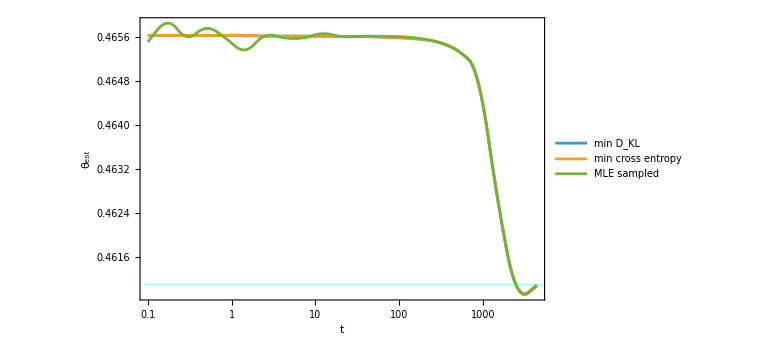

```mathematica
ListLogLinearPlot[{θestKL,θestCrossEntropy,θestMLE},InterpolationOrder->2,PlotRange->All,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","MLE sampled"},ImageSize->Large,Joined->True]
```

α = 0.1

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
nα=0.1;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];

tmin=0.1;
tmax=10000;
points=10;

times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];


θestEqTPM=ParallelTable[{Exp[t],θ/.Last@FindMinimum[dKL2PMExact[Exp[t],θ,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],{θ,teff},Method->"PrincipalAxis"]},{t,times}];

θestCrossEntropyTPM=ParallelTable[{Exp[t],thetaEstMLE2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];

θestKLTPM=ParallelTable[{Exp[t],thetaEstKL2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];
```

```mathematica
r𝒩=10^7;

meas2PM[t_]:=1/r𝒩 nmeasurements2[r𝒩,Flatten[Pness2PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]]



model2PM[t_]:=Flatten[PModel2PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]]]



θestMLETPM=ParallelTable[{Exp[t],mleGeneral2PM[meas2PM[Exp[t]],model2PM[Exp[t]],rT]},{t,times}];
```

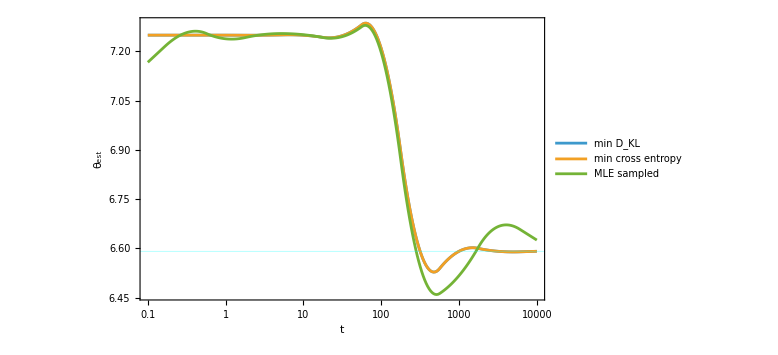

```mathematica
ListLogLinearPlot[{θestKLTPM,θestCrossEntropyTPM,θestMLETPM},InterpolationOrder->2,PlotRange->All,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","MLE sampled"},ImageSize->Large,Joined->True]
```

```mathematica
{rT,rTp,teff}
```

{0.654744,65.4744,6.59087}

```mathematica
(θ/.Last@FindMinimum[dKL2PMExact[10,θ,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],{θ,teff},Method->"PrincipalAxis"])-θ/.Last@FindMinimum[dKL2PMExact[1000,θ,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],{θ,teff},Method->"PrincipalAxis"]
```

0.658189

```mathematica
θestdKL2PMshortimeGap2[rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]
```

0.65946

Now calculate the mean and variance of ntrials MLE estimators

```mathematica
MeanMLEestimates2PM[t_,𝒩_,ntrials_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=
Mean[ParallelTable[Quiet@mleGeneral2PM[nmeasurements2[𝒩,Flatten[Pness2PMExact[t,ω,T,Tp,α,p1init,p2init]]],Flatten[PModel2PMExact[t,θ,ω,p1init,p2init]],T],{ntrials}]]

MeanMLEestimates2PM::usage="MeanMLEestimates2PM[t,𝒩,ntrials,ω,T,Tp,α,p1init,p2init,γ:10^-3,Λ:10^2] calculates the average MLE estimators for n trials for 2PM.";


VariancesMLEestimates2PM[t_,𝒩_,ntrials_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=
Variance[ParallelTable[Quiet@mleGeneral2PM[nmeasurements2[𝒩,Flatten[Pness2PMExact[t,ω,T,Tp,α,p1init,p2init]]],Flatten[PModel2PMExact[t,θ,ω,p1init,p2init]],T],{ntrials}]]

VariancesMLEestimates2PM::usage="VariancesMLEestimates2PM[t,𝒩,ntrials,ω,T,Tp,α,p1init,p2init,γ:10^-3,Λ:10^2] calculates the variance MLE estimators for n trials for 2PM.";
```

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
nα=0.01;

nγ=10^-3;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];
```

```mathematica
nTrials=20;

𝒩list=Table[10^i,{i,6,12}];

tlist={5,20,1000};

MeansVsNandtTable2PM=ParallelTable[{𝒩,Quiet@MeanMLEestimates2PM[t,𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]},{t,tlist},{𝒩,𝒩list}];

(*MeansVsNandtTable=ParallelTable[{𝒩,Mean[Table[mleGeneral1PM2[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]],PModel1PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]],rT],{nTrials}]]},{t,tlist},{𝒩,𝒩list}];*)
```

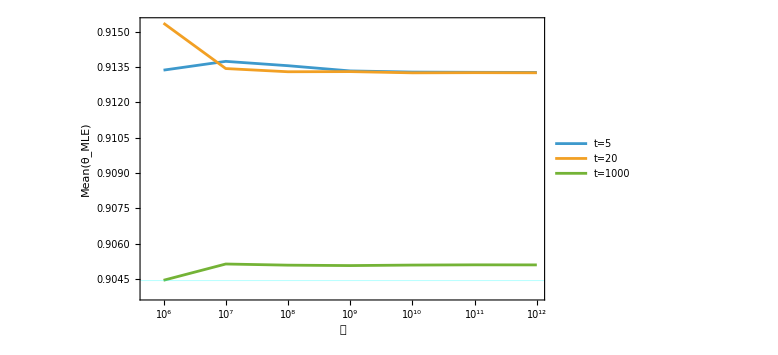

```mathematica
ListLogLinearPlot[MeansVsNandtTable2PM,PlotRange->All,Joined->True,PlotLegends->Table[StringForm["t=``",t],{t,tlist}],GridLines->{{},{{rT,Directive[Thick,Black]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"𝒩","Mean(θ_MLE)"},ImageSize->Large]
```

```mathematica
{rT,teff}
```

{0.447669,0.904421}

Compare average variances to the CFI

```mathematica
CFIExact2PM[θ_,t_,ω_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=Total@Flatten[(D[PModel2PMExact[t,θp,ω,p1init,p2init,γ,Λ],{θp,1}])^2/PModel2PMExact[t,θp,ω,p1init,p2init,γ,Λ]]/.θp->θ

(*CFIExact1PM2[θ_,t_,ω_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=-Total[PModel1PMExact[t,θp,ω,p1init,p2init,γ,Λ]*(D[Log@PModel1PMExact[t,θp,ω,p1init,p2init,γ,Λ],{θp,2}])]/.θp->θ*)
```

```mathematica
CFIExact2PM[0.1,10,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]]
```

0.106786

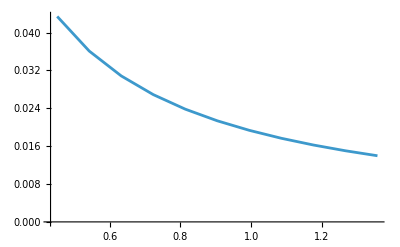

```mathematica
ListLinePlot[Table[{θ,CFIExact2PM[θ,10,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]]},{θ,0.5*teff,1.5*teff,teff/10}]]
```

```mathematica
times={5,20,100};

nTrials=20;

𝒩list=Table[10^i,{i,5,10}];

varsVsNandt2PM=ParallelTable[{𝒩,Quiet@VariancesMLEestimates2PM[t,𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]},{t,times},{𝒩,𝒩list}];

CFIsVsNandt2PM=ParallelTable[{𝒩,1/(𝒩*CFIExact2PM[Quiet@MeanMLEestimates2PM[t,𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ],t,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]])},{t,times},{𝒩,𝒩list}];
```

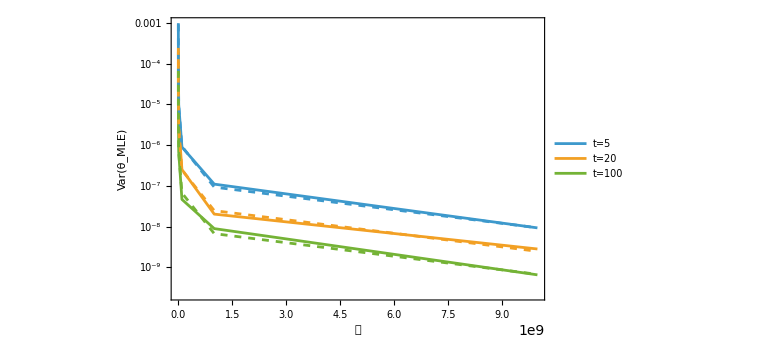

```mathematica
Show[ListLogPlot[varsVsNandt2PM,PlotRange->All,Frame->True,FrameLabel->{"𝒩","Var(θ_MLE)"},PlotLegends->Table[StringForm["t=``",t],{t,times}],Joined->True,ImageSize->Large],

ListLogPlot[CFIsVsNandt2PM,PlotRange->All,Joined->True,PlotStyle->Dashed]]
```

Now select a 𝒩 and mean estimates and errors for MLE

```mathematica
tmin=0.1;
tmax=10000;

points=10;
times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

r𝒩=10^8;
nTrials=50;

(*meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]]*)

(*MeanMLEestimatesList=ParallelTable[Mean[Table[mleGeneral1PM2[meas[Exp[t]],PModel1PMExact[Exp[t],θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]],rT],{nTrials}]],{t,times}];
ErrorsMLEestimatesList=ParallelTable[Quiet[Sqrt[Variance[Table[mleGeneral1PM2[meas[Exp[t]],PModel1PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]],rT],{nTrials}]]]],{t,times}];*)

MeanMLEestimatesList2PM=ParallelTable[Quiet@MeanMLEestimates2PM[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ],{t,times}];
ErrorsMLEestimatesList2PM=ParallelTable[Sqrt[Quiet@VariancesMLEestimates2PM[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]],{t,times}];

MeanMLEWithErrors2PM=Transpose[{Exp[times],Around@@@Transpose[{MeanMLEestimatesList2PM,ErrorsMLEestimatesList2PM}]}];
```

```mathematica
θestCrossEntropy2PM=ParallelTable[{Exp[t],thetaEstMLE2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];

θestKL2PM=ParallelTable[{Exp[t],thetaEstKL2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];
```

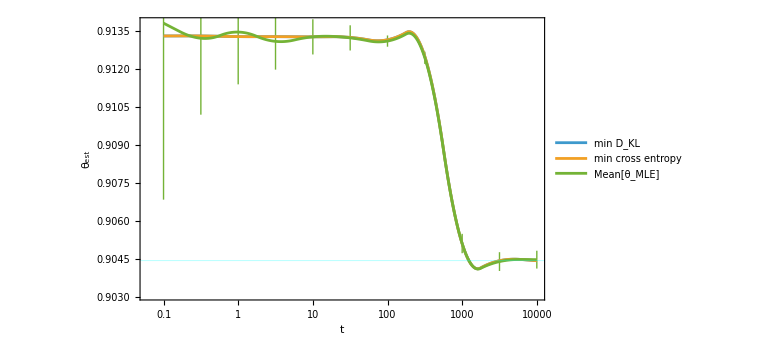

```mathematica
Show[ListLogLinearPlot[{θestKL2PM,θestCrossEntropy2PM,MeanMLEWithErrors2PM},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","Mean[θ_MLE]",PlotLabel->StringForm["𝒩=``",r𝒩]},ImageSize->Large,Joined->True]]
```

#### 1PM Bayesian

```mathematica
likelihood1PM[θp_,meas_,model_]:=(model[[1]])^meas[[1]]*(model[[2]])^meas[[2]]/.θ->θp
(*likelihood1PM2[θp_,meas_,model_]:=Exp[Sum[meas[[i]] Log[model[[i]]],{i,2}]]/.θ->θp*)
likelihood1PM2[θp_,meas_,model_]:=Exp[-crossEntropy[meas,model]]/.θ->θp

LogLikelihood1PM[θp_,meas_,model_]:=-crossEntropy[meas,model]/.θ->θp
```

First choose a log uniform prior

```mathematica
priorLogUniform[θ_,θmin_,θmax_]:=1/(Log[θmax/θmin]θ)
```

```mathematica
(*prior[θ_]:=PDF[UniformDistribution[{θmin,θmax}],θ]*)
```

Plot log likelihood

```mathematica
θmin=rT;
θmax=teff;


r𝒩=10^10;
rt=20;

meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]]

meastest=meas[rt];
```

-6.9311×10^9

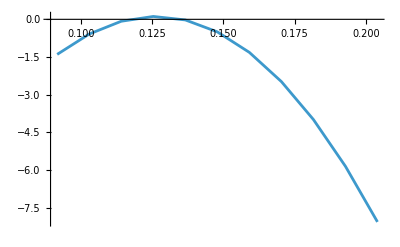

```mathematica
funcmax=First@NMaximize[{LogLikelihood1PM[θ,meastest,model1PM[rt]]+Log[priorLogUniform[θ,θmin,θmax]],θmin<θ<θmax},θ,WorkingPrecision->MachinePrecision,PrecisionGoal->8]

ListLinePlot@Table[{θ,LogLikelihood1PM[θ,meastest,model1PM[rt]]+Log[priorLogUniform[θ,θmin,θmax]]-funcmax},{θ,θmin,θmax,(θmax-θmin)/10}]
```

```mathematica
posterior1PMDiscrete[meas_,model_,θmin_,θmax_,θpoints_:200]:=Module[{grid,logPostVals,shifted,unnormalizedPosterior},
grid=Subdivide[θmin,θmax,θpoints];
logPostVals=LogLikelihood1PM[#,meas,model]+Log[priorLogUniform[#,θmin,θmax]]&/@grid;
shifted=logPostVals-Max[logPostVals];
unnormalizedPosterior=Exp[shifted];


unnormalizedPosterior/Total[unnormalizedPosterior]

]
posterior1PMDiscrete::usage="posterior1PMDiscrete[meas,model,θmin,θmax,θpoints:200] calculates the posterior distribution P(θ|measurements) on a discrete grid in θ.";
```

Plot posterior

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
nα=0.01;

nγ=10^-3;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];

θmin=rT;

θmax=1.1*teff;
θpoints=200;
```

```mathematica
r𝒩=10^12;

meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]]

model1PM[t_]:=PModel1PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]],nγ]
```

General::munfl: Exp[-1410.35] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1372.34] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1334.81] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

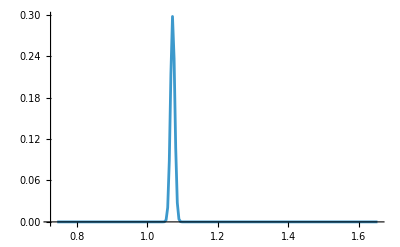

```mathematica
θgrid=Subdivide[θmin,θmax,θpoints];


rt=5;


ListLinePlot[Partition[Riffle[θgrid,posterior1PMDiscrete[meas[rt],model1PM[rt],θmin,θmax,θpoints]],2],PlotRange->All]
```

```mathematica
Total@posterior1PMDiscrete[meas[rt],model1PM[rt],θmin,θmax,θpoints]
```

General::munfl: Exp[-51352.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-50445.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-49546.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.

General::munfl: Exp[-715.09] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-726.356] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-737.71] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

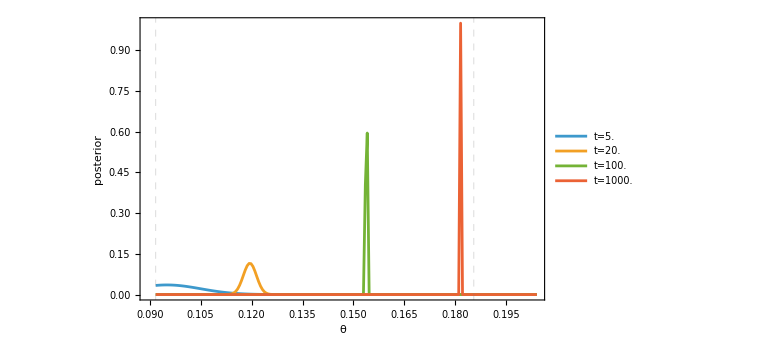

```mathematica
posteriorData[t_]:=Partition[Riffle[θgrid,posterior1PMDiscrete[meas[t],model1PM[t],θmin,θmax,θpoints]],2]

ttable={5,20,100,1000};

ListLinePlot[Table[posteriorData[t],{t,ttable}],PlotRange->All,PlotLegends->Table[StringForm["t=``",t],{t,N@ttable}],Frame->True,FrameLabel->{"θ", "posterior"},ImageSize->Large,GridLines->{{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}},None}]
```

```mathematica
{rT,rTp,teff}
```

{0.0917874,9.17874,0.185437}

Calculate mean and variance of posterior

```mathematica
posteriorMean[meas_,model_,θmin_,θmax_,θpoints_:200]:=Module[{grid,logPostVals,shifted,unnormalizedPosterior},
grid=Subdivide[θmin,θmax,θpoints];
Total[grid Chop@posterior1PMDiscrete[meas,model,θmin,θmax,θpoints]]

]
posteriorMean::usage="posteriorMean[meas,model,θmin,θmax,θpoints:200] calculates the mean of the posterior distribution P(θ|measurements) on a discrete grid in θ.";

posteriorVariance[meas_,model_,θmin_,θmax_,θpoints_:200]:=Module[{grid,logPostVals,shifted,unnormalizedPosterior},
grid=Subdivide[θmin,θmax,θpoints];
Total[(grid-posteriorMean[meas,model,θmin,θmax,θpoints])^2 posterior1PMDiscrete[meas,model,θmin,θmax,θpoints]]

]
posteriorVariance::usage="posteriorVariance[meas,model,θmin,θmax,θpoints:200] calculates the variance of the posterior distribution P(θ|measurements) on a discrete grid in θ.";
```

General::munfl: Exp[-721.617] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-736.732] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-752.005] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

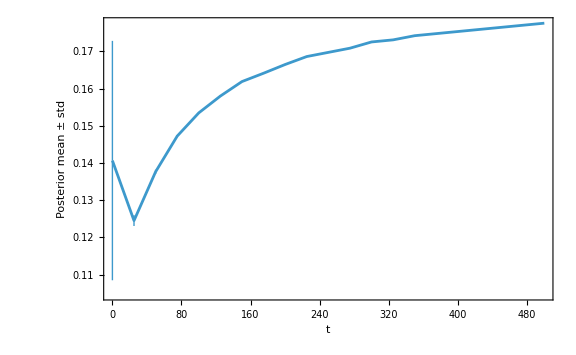

```mathematica
r𝒩=10^12;
tmin=0.1;
tmax=500;
tpoints=20;

meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]]



θgrid=Subdivide[θmin,θmax,θpoints];


times=Subdivide[tmin,tmax,tpoints];
(*
{ListLinePlot[Table[{t,posteriorMean[meas[t],model1PM[t],θmin,θmax,θpoints]},{t,times}],PlotRange->All,Frame->True,FrameLabel->{"t", "Mean"},ImageSize->Medium,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}],ListLinePlot[Table[{t,posteriorVariance[meas[t],model1PM[t],θmin,θmax,θpoints]},{t,times}],PlotRange->All,Frame->True,FrameLabel->{"t", "Variance"},ImageSize->Medium,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}]}*)


meansWithError=Table[{t,Around[posteriorMean[meas[t],model1PM[t],θmin,θmax,θpoints],Sqrt[posteriorVariance[meas[t],model1PM[t],θmin,θmax,θpoints]]]},{t,times}];

ListLinePlot[meansWithError,Frame->True,FrameLabel->{"t","Posterior mean ± std"},ImageSize->Large]
```

```mathematica
{rT,rTp,teff}
```

{0.0917874,9.17874,0.185437}

Now plot the all estimators together

```mathematica
θmin=rT/2;
θmax=teff;
θpoints=200;

tmin=0.1;
tmax=1000;
points=20;

r𝒩=10^12;

times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];
meansWithError2=Table[{Exp[t],Around[posteriorMean[meas[Exp[t]],model1PM[Exp[t]],θmin,θmax,θpoints],Sqrt[posteriorVariance[meas[t],model1PM[t],θmin,θmax,θpoints]]]},{t,times}];


meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]]

θestMLE=ParallelTable[{Exp[t],mleGeneral1PM2[meas[Exp[t]],model1PM[Exp[t]],rT]},{t,times}];

θestCrossEntropy=ParallelTable[{Exp[t],thetaEstMLE1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]},{t,times}];

θestKL=ParallelTable[{Exp[t],thetaEstKL1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]},{t,times}];
```

General::munfl: Exp[-1486.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1464.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1442.37] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

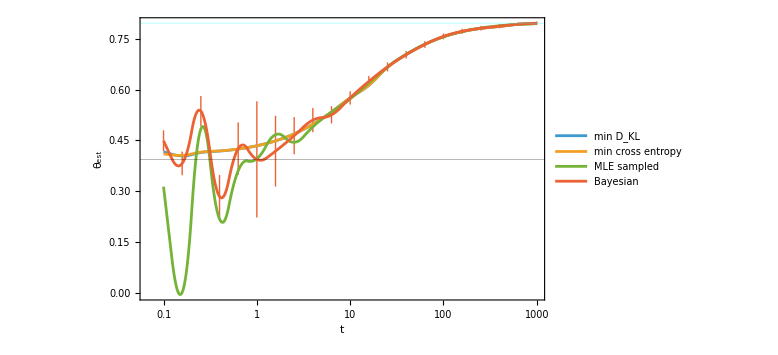

```mathematica
ListLogLinearPlot[{θestKL,θestCrossEntropy,θestMLE,meansWithError2},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","MLE sampled","Bayesian"},ImageSize->Large,Joined->True]
```

Now look at the average of ntrials estimates

```mathematica
AvgMeanPosteriorEstimates[t_,𝒩_,ntrials_,θmin_,θmax_,θpoints_:200]:=
Mean[ParallelTable[posteriorMean[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],model1PM[t],θmin,θmax,θpoints],{ntrials}]]



AvgVariancesPosteriorEstimates[t_,𝒩_,ntrials_,θmin_,θmax_,θpoints_:200]:=Mean[ParallelTable[posteriorVariance[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],model1PM[t],θmin,θmax,θpoints],{ntrials}]]
```

```mathematica
points=10;

nTrials=50;

𝒩list=Table[10^i,{i,6,12}];

tlist={0.1,20,1000};

MeansVsNandtTable=ParallelTable[{𝒩,Quiet@AvgMeanPosteriorEstimates[t,𝒩,nTrials,θmin,θmax,θpoints]},{t,tlist},{𝒩,𝒩list}];
```

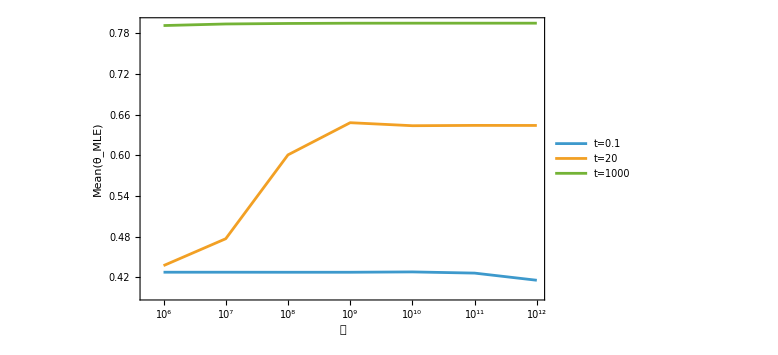

```mathematica
ListLogLinearPlot[MeansVsNandtTable,PlotRange->All,Joined->True,PlotLegends->Table[StringForm["t=``",t],{t,tlist}],GridLines->{{{rT,Directive[Thick,Black]},{teff,Directive[Thick,Cyan]}},{}},Frame->True,FrameLabel->{"𝒩","Mean(θ_MLE)"},ImageSize->Large]
```

```mathematica
{rT,teff}
```

{0.393584,0.795154}

```mathematica
times={20,100,1000};

nTrials=50;

𝒩list=Table[10^i,{i,6,12}];

meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]]

model1PM[t_]:=PModel1PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]],nγ]


varsVsNandt=ParallelTable[{𝒩,Quiet@AvgVariancesPosteriorEstimates[t,𝒩,nTrials,θmin,θmax,θpoints]},{t,times},{𝒩,𝒩list}];
(*varsVsNandt=ParallelTable[{𝒩,Quiet@posteriorVariance[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],model1PM[t],θmin,θmax,θpoints]},{t,times},{𝒩,𝒩list}];*)

CFIsVsNandt=ParallelTable[{𝒩,1/(𝒩*CFIExact1PM[Quiet@AvgMeanPosteriorEstimates[t,𝒩,nTrials,θmin,θmax,θpoints],t,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]])},{t,times},{𝒩,𝒩list}];
(*CFIsVsNandt=ParallelTable[{𝒩,1/(𝒩*CFIExact1PM[posteriorMean[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],model1PM[t],θmin,θmax,θpoints],t,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]])},{t,times},{𝒩,𝒩list}];*)
```

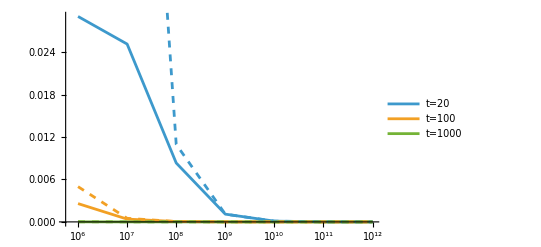

```mathematica
Show[ListLogLinearPlot[varsVsNandt,PlotRange->All,PlotLegends->Table[StringForm["t=``",t],{t,times}],Joined->True],

ListLogLinearPlot[CFIsVsNandt,PlotRange->All,Joined->True,PlotStyle->Dashed]]
```

Now select a 𝒩 and mean estimates and errors for MLE

```mathematica
points=10;
times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

r𝒩=10^12;
nTrials=50;

AvgMeanPosteriorEstimatesList=ParallelTable[Quiet@AvgMeanPosteriorEstimates[Exp[t],𝒩,nTrials,θmin,θmax,θpoints],{t,times}];
ErrorsPosteriorEstimatesList=ParallelTable[Quiet[Sqrt[AvgVariancesPosteriorEstimates[Exp[t],𝒩,nTrials,θmin,θmax,θpoints]]],{t,times}];
(*ErrorsPosteriorEstimatesList=ParallelTable[Quiet[Sqrt[posteriorVariance[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],model1PM[t],θmin,θmax,θpoints]]],{t,times}]*)

AvgMeanPosteriorEstimatesWithErrors=Transpose[{Exp[times],Around@@@Transpose[{AvgMeanPosteriorEstimatesList,ErrorsPosteriorEstimatesList}]}];

MeanPosteriorEstimatesWithErrors=Table[{Exp[t],Around[posteriorMean[meas[Exp[t]],model1PM[Exp[t]],θmin,θmax,θpoints],Sqrt[posteriorVariance[meas[t],model1PM[t],θmin,θmax,θpoints]]]},{t,times}];
```

General::munfl: Exp[-1624.69] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1600.43] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1576.14] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
MeanMLEestimatesList=ParallelTable[Quiet@MeanMLEestimates[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ],{t,times}];
ErrorsMLEestimatesList=ParallelTable[Quiet[Sqrt[VariancesMLEestimates[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],{t,times}];

MeanMLEWithErrors=Transpose[{Exp[times],Around@@@Transpose[{MeanMLEestimatesList,ErrorsMLEestimatesList}]}];

θestCrossEntropy=ParallelTable[{Exp[t],thetaEstMLE1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];

θestKL=ParallelTable[{Exp[t],thetaEstKL1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {θ} = {0.}.

ListLogLinearPlot::ioproc: {{-2.30259,θ},{-1.38155,0.103266},{-0.460517,0.107619},{0.460517,0.108684},{1.38155,0.113091},{2.30259,0.122416},{3.22362,0.139423},{4.14465,0.15911},{5.06569,0.18331},{5.98672,0.196493},{6.90776,0.202543}} may contain non-machine-precision numbers, complex numbers or invalid entries.

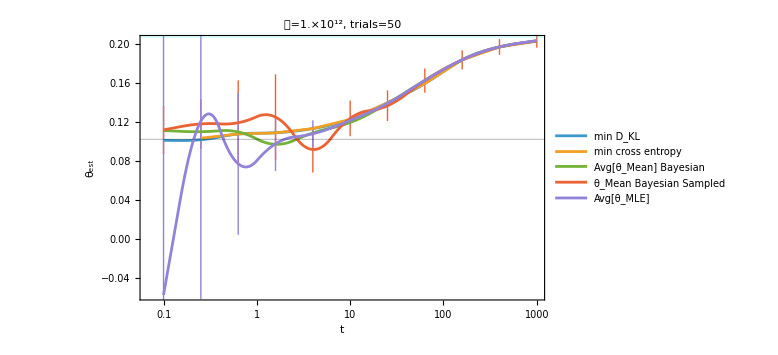

```mathematica
Show[ListLogLinearPlot[{θestKL,θestCrossEntropy,AvgMeanPosteriorEstimatesWithErrors,MeanPosteriorEstimatesWithErrors,MeanMLEWithErrors},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","Avg[θ_Mean] Bayesian","θ_Mean Bayesian Sampled","Avg[θ_MLE]"},PlotLabel->StringForm["𝒩=``, trials=``",ScientificForm[r𝒩//N],nTrials],ImageSize->Large,Joined->True]]
```

Now lets try different estimators

```mathematica
maxPosteriorEstimator1PM[t_]:=Module[{posteriorData,grid},
grid=Subdivide[θmin,θmax,θpoints];
posteriorData=Partition[Riffle[grid,posterior1PMDiscrete[meas[t],model1PM[t],θmin,θmax,θpoints]],2];

posteriorData[[Position[posteriorData,Max[posteriorData[[All,2]]]][[1,1]],1]]
]
```

```mathematica
maxPosteriorEstimator1PM[20]
```

General::munfl: Exp[-82513.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-81620.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-80723.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.645563

General::munfl: Exp[-1702.54] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1677.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1652.82] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

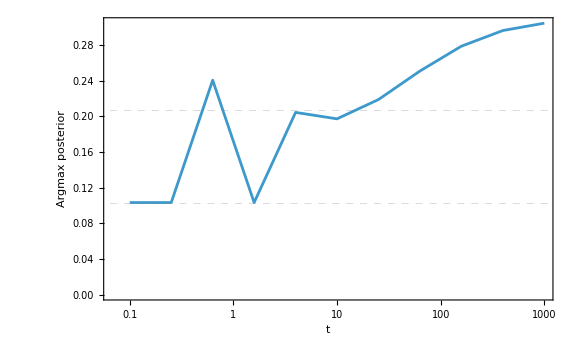

```mathematica
times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

ListLogLinearPlot[Table[{Exp[t],maxPosteriorEstimator1PM[Exp[t]]},{t,times}],PlotRange->All,Frame->True,Joined->True,FrameLabel->{"t", "Argmax posterior"},ImageSize->Large,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}]
```

```mathematica
logMeanEstimator1PM[t_,θmin_,θmax_,θpoints_:200]:=Module[{θgrid,logTgrid},

θgrid=Subdivide[θmin,θmax,θpoints];
logTgrid=(Log[#]&/@θgrid);
Exp[Total[logTgrid*Chop[posterior1PMDiscrete[meas[t],model1PM[t],θmin,θmax,θpoints]]]]

]

logMeanVariance1PM[t_,θmin_,θmax_,θpoints_:200]:=Module[{θgrid,logTgrid,logT2grid},

θgrid=Subdivide[θmin,θmax,θpoints];
logTgrid=(Log[#]&/@θgrid);
logT2grid=(Log[#])^2&/@θgrid;


logMeanEstimator1PM[t,θmin,θmax,θpoints]*Sqrt[Total[logT2grid*Chop[posterior1PMDiscrete[meas[t],model1PM[t],θmin,θmax,θpoints]]]-(Total[logTgrid*Chop[posterior1PMDiscrete[meas[t],model1PM[t],θmin,θmax,θpoints]]])^2]


]
```

General::munfl: Exp[-957.05] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-941.899] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-926.733] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

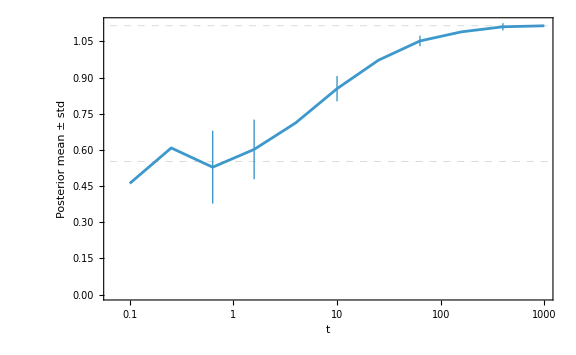

```mathematica
r𝒩=10^12;

meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]]

model1PM[t_]:=PModel1PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]],nγ]


(*{ListLogLinearPlot[Table[{Exp[t],logMeanEstimator1PM[Exp[t],θmin,θmax,θpoints]},{t,times}],Joined->True,PlotRange->All,Frame->True,FrameLabel->{"t", "Mean"},ImageSize->Large,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}],ListLogLinearPlot[Table[{Exp[t],logMeanVariance1PM[Exp[t],θmin,θmax,θpoints]},{t,times}],Joined->True,PlotRange->All,Frame->True,FrameLabel->{"t", "Variance"},ImageSize->Large,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}]}*)


logMeansWithError=Table[{Exp[t],Around[logMeanEstimator1PM[Exp[t],θmin,θmax,θpoints],logMeanVariance1PM[t,θmin,θmax,θpoints]]},{t,times}];

ListLogLinearPlot[logMeansWithError,Joined->True,Frame->True,FrameLabel->{"t","Posterior mean ± std"},ImageSize->Large,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}]
```

```mathematica
AvgLogMeanPosteriorEstimates[t_,ntrials_,θmin_,θmax_,θpoints_:200]:=Mean[ParallelTable[logMeanEstimator1PM[t,θmin,θmax,θpoints],{ntrials}]]



AvgLogVariancesPosteriorEstimates[t_,ntrials_,θmin_,θmax_,θpoints_:200]:=Mean[ParallelTable[logMeanVariance1PM[t,θmin,θmax,θpoints],{ntrials}]]
```

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
nα=0.01;

nγ=10^-3;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];

θmin=rT/2;
θmax=teff;
θpoints=200;

tmin=0.1;
tmax=1000;
points=10;
times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

r𝒩=10^10;
nTrials=20;

meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]]

model1PM[t_]:=PModel1PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]],nγ]
```

```mathematica
(*Avg[Subscript[θ, Log mean]]*)
AvgLogMeanPosteriorEstimatesList=ParallelTable[Quiet@AvgLogMeanPosteriorEstimates[Exp[t],nTrials,θmin,θmax,θpoints],{t,times}];
ErrorsLogPosteriorEstimatesList=ParallelTable[Quiet@AvgLogVariancesPosteriorEstimates[Exp[t],nTrials,θmin,θmax,θpoints],{t,times}];
(*ErrorsPosteriorEstimatesList=ParallelTable[Quiet[Sqrt[posteriorVariance[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],model1PM[t],θmin,θmax,θpoints]]],{t,times}]*)

AvgLogMeanPosteriorEstimatesWithErrors=Transpose[{Exp[times],Around@@@Transpose[{AvgLogMeanPosteriorEstimatesList,ErrorsLogPosteriorEstimatesList}]}];
```

```mathematica
(*Avg[Subscript[θ, Mean]]*)
AvgMeanPosteriorEstimatesList=ParallelTable[Quiet@AvgMeanPosteriorEstimates[Exp[t],r𝒩,nTrials,θmin,θmax,θpoints],{t,times}];
ErrorsPosteriorEstimatesList=ParallelTable[Quiet[Sqrt[AvgVariancesPosteriorEstimates[Exp[t],r𝒩,nTrials,θmin,θmax,θpoints]]],{t,times}];
(*ErrorsPosteriorEstimatesList=ParallelTable[Quiet[Sqrt[posteriorVariance[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],model1PM[t],θmin,θmax,θpoints]]],{t,times}]*)

AvgMeanPosteriorEstimatesWithErrors=Transpose[{Exp[times],Around@@@Transpose[{AvgMeanPosteriorEstimatesList,ErrorsPosteriorEstimatesList}]}];
```

```mathematica
(*Avg[Subscript[θ, MLE]]*)
MeanMLEestimatesList=ParallelTable[Quiet@MeanMLEestimates[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ],{t,times}];
ErrorsMLEestimatesList=ParallelTable[Quiet[Sqrt[VariancesMLEestimates[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],{t,times}];

MeanMLEWithErrors=Transpose[{Exp[times],Around@@@Transpose[{MeanMLEestimatesList,ErrorsMLEestimatesList}]}];
```

```mathematica
θestCrossEntropy=ParallelTable[{Exp[t],thetaEstMLE1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];

θestKL=ParallelTable[{Exp[t],thetaEstKL1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];
```

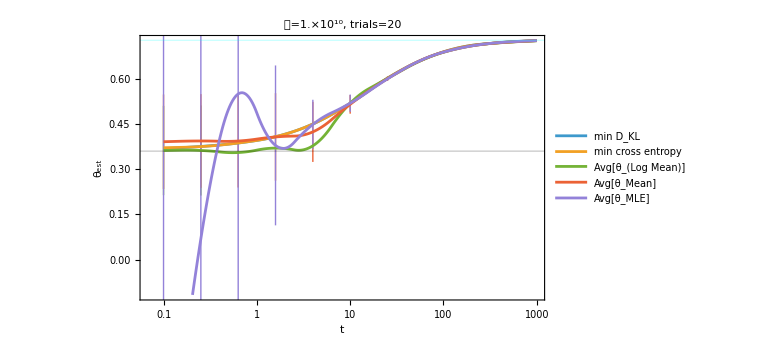

```mathematica
Show[ListLogLinearPlot[{θestKL,θestCrossEntropy,AvgLogMeanPosteriorEstimatesWithErrors,AvgMeanPosteriorEstimatesWithErrors,MeanMLEWithErrors},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","Avg[θ_(Log Mean)]","Avg[θ_Mean]","Avg[θ_MLE]"},PlotLabel->StringForm["𝒩=``, trials=``",ScientificForm[r𝒩//N],nTrials],ImageSize->Large,Joined->True]]
```

Now try using CFI prior

```mathematica
CFIExact1PM[θ_,t_,ω_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=Total[(D[PModel1PMExact[t,θp,ω,p1init,p2init,γ,Λ],{θp,1}])^2/PModel1PMExact[t,θp,ω,p1init,p2init,γ,Λ]]/.θp->θ

(*CFIExact1PM2[θ_,t_,ω_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=-Total[PModel1PMExact[t,θp,ω,p1init,p2init,γ,Λ]*(D[Log@PModel1PMExact[t,θp,ω,p1init,p2init,γ,Λ],{θp,2}])]/.θp->θ*)
```

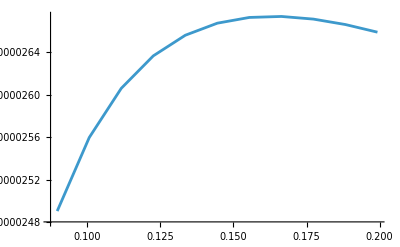

```mathematica
ListLinePlot[Table[{θ,CFIExact1PM[θ,100,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]]},{θ,θmin,θmax,(θmax-θmin)/10}],PlotRange->All]
```

```mathematica
priorCFI[θ_,t_,ω_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=Module[{numerator},
numerator[θp_]:=Sqrt[CFIExact1PM[θp,t,ω,p1init,p2init,γ,Λ]];

numerator[θ]/NIntegrate[numerator[θp],{θp,θmin,θmax}]
]
```

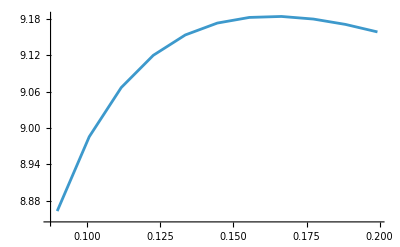

```mathematica
ListLinePlot[Table[{θ,priorCFI[θ,100,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]]},{θ,θmin,θmax,(θmax-θmin)/10}],PlotRange->All]
```

```mathematica
posterior1PMDiscreteCFIPrior[t_,meas_,model_,θmin_,θmax_,θpoints_:200]:=Module[{grid,logPostVals,shifted,unnormalizedPosterior},
grid=Subdivide[θmin,θmax,θpoints];
logPostVals=LogLikelihood1PM[#,meas,model]+Log[priorCFI[#,t,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]]]&/@grid;
shifted=logPostVals-Max[logPostVals];
unnormalizedPosterior=Exp[shifted];


unnormalizedPosterior/Total[unnormalizedPosterior]

]
```

General::munfl: Exp[-716.139] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-737.423] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-759.021] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

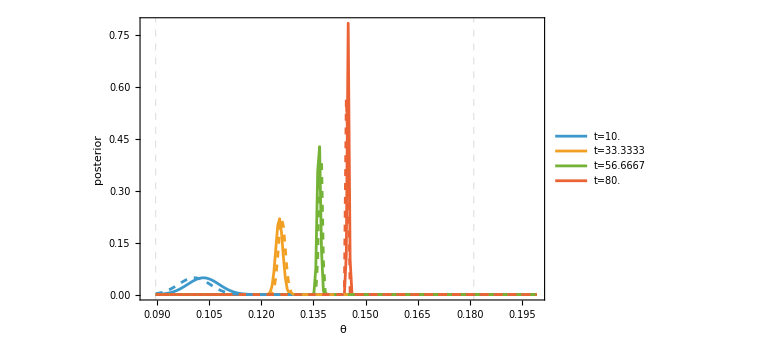

```mathematica
ttable=Subdivide[10,80,3];



posteriorData[t_]:=Partition[Riffle[θgrid,posterior1PMDiscrete[meas[t],model1PM[t],θmin,θmax,θpoints]],2]


posteriorDataCFIPrior[t_]:=Partition[Riffle[θgrid,posterior1PMDiscreteCFIPrior[t,meas[t],model1PM[t],θmin,θmax,θpoints]],2]


Show[ListLinePlot[Table[posteriorDataCFIPrior[t],{t,ttable}],PlotRange->All,PlotLegends->Table[StringForm["t=``",t],{t,N@ttable}],Frame->True,FrameLabel->{"θ", "posterior"},ImageSize->Large,GridLines->{{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}},None}],

ListLinePlot[Table[posteriorData[t],{t,ttable}],PlotRange->All,PlotStyle->Dashed]]
```

```mathematica
posteriorMeanCFIPrior[t_]:=Total[θgrid Chop@posterior1PMDiscreteCFIPrior[t,meas[t],model1PM[t],θmin,θmax,θpoints]]

posteriorVarianceCFIPrior[t_]:=Total[(θgrid-posteriorMeanCFIPrior[t])^2 posterior1PMDiscreteCFIPrior[t,meas[t],model1PM[t],θmin,θmax,θpoints]]
```

General::munfl: Exp[-23751.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-23471.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-23191.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

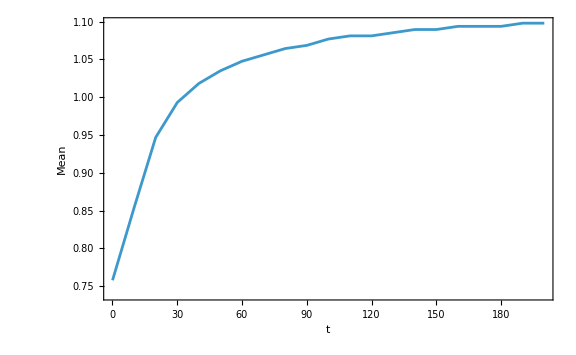
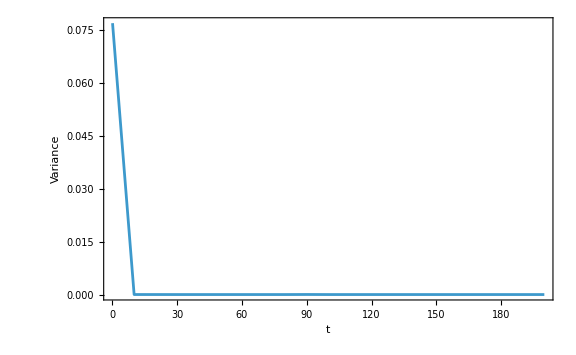

```mathematica
r𝒩=10^12;
tmin=0.1;
tmax=200;
tpoints=20;

meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]]



θgrid=Subdivide[θmin,θmax,θpoints];


times=Subdivide[tmin,tmax,tpoints];

{ListLinePlot[Table[{t,posteriorMeanCFIPrior[t]},{t,times}],PlotRange->All,Frame->True,FrameLabel->{"t", "Mean"},ImageSize->Large,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}],ListLinePlot[Table[{t,posteriorVarianceCFIPrior[t]},{t,times}],PlotRange->All,Frame->True,FrameLabel->{"t", "Variance"},ImageSize->Large,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}]}
```

```mathematica
{rT,rTp,teff}
```

{0.305499,30.5499,0.617197}

```mathematica
meansWithError=Table[{t,Around[posteriorMean[t],Sqrt[posteriorVariance[t]]]},{t,times}];

meansWithErrorCFIPrior=Table[{t,Around[posteriorMeanCFIPrior[t],Sqrt[posteriorVarianceCFIPrior[t]]]},{t,times}];
```

General::munfl: Exp[-969.684] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-947.501] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-925.551] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-992.512] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-970.067] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-947.854] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

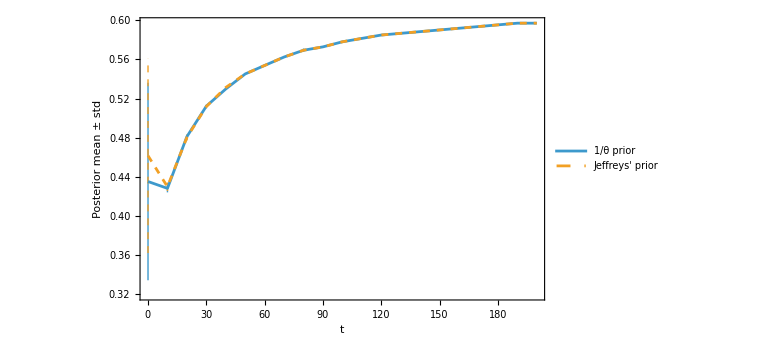

```mathematica
ListLinePlot[{meansWithError,meansWithErrorCFIPrior},Frame->True,FrameLabel->{"t","Posterior mean ± std"},ImageSize->Large,PlotLegends->{"1/θ prior","Jeffreys' prior"},PlotStyle->{{},Dashed}]
```

```mathematica
tmin=0.1;
tmax=1000;
points=20;

r𝒩=10^12;

times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];



θestMLE=ParallelTable[{Exp[t],mleGeneral1PM2[meas[Exp[t]],model1PM[Exp[t]],rT]},{t,times}];

θestCrossEntropy=ParallelTable[{Exp[t],thetaEstMLE1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]},{t,times}];

θestKL=ParallelTable[{Exp[t],thetaEstKL1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]},{t,times}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {θ} = {0.}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {θ} = {0.}.

ListLogLinearPlot::ioproc: {{-2.30259,θ},{-1.84207,θ},{-1.38155,0.0905769},{-0.921034,0.0940052},{-0.460517,0.0905624},{0.,0.0941079},{0.460517,0.0951381},{0.921034,0.0963932},{1.38155,0.0984388},{1.84207,0.101455},{2.30259,0.105835},{2.7631,0.111879},{3.22362,0.119743},{3.68414,0.128927},{4.14465,0.139559},{4.60517,0.149603},{5.06569,0.158547},{5.5262,0.165749},{5.98672,0.171994},{6.44724,0.175493},{6.90776,0.177655}} may contain non-machine-precision numbers, complex numbers or invalid entries.

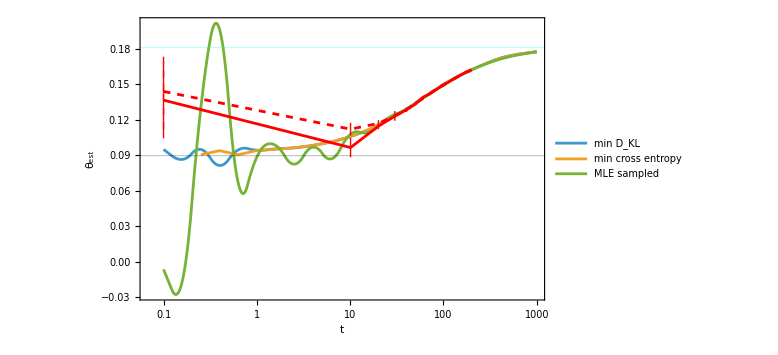

```mathematica
Show[ListLogLinearPlot[{θestKL,θestCrossEntropy,θestMLE},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","MLE sampled"},ImageSize->Large,Joined->True],

ListLogLinearPlot[{meansWithError,meansWithErrorCFIPrior},Joined->True,PlotLegends->"Bayesian",Frame->True,PlotStyle->{Red,{Red,Dashed}}]]
```

#### 1PM Bayesian shot-by-shot (doesn’t work for large 𝒩)

```mathematica
posterior1PMDiscrete[meas_,model_,θmin_,θmax_,θpoints_:200]:=Module[{grid,logPostVals,shifted,unnormalizedPosterior},
grid=Subdivide[θmin,θmax,θpoints];
logPostVals=LogLikelihood1PM[#,meas,model]+Log[priorLogUniform[#,θmin,θmax]]&/@grid;
shifted=logPostVals-Max[logPostVals];
unnormalizedPosterior=Exp[shifted];


unnormalizedPosterior/Total[unnormalizedPosterior]

]
```

```mathematica
singleShots[𝒩_,probs_]:=RandomVariate[BernoulliDistribution[probs[[2]]],𝒩]

singleShots1PM[t_,𝒩_]:=singleShots[𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]]

posterior1PMShotByShot[measList_,model_,θmin_,θmax_,θpoints_:200]:=Module[{grid,posterior,probs},
grid=Subdivide[θmin,θmax,θpoints];

posterior=prior[#]&/@grid;
posterior=posterior/Total[posterior];


probs=PModel1PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]]&/@grid;

Do[
posterior=posterior*Table[If[outcome==0,probs[[i,1]],probs[[i,2]]],{i,Length[grid]}];
posterior=posterior/Total[posterior];,{outcome,measList}];

posterior
]
```

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
nα=0.01;

nγ=10^-3;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];

θmin=rT;
θmax=1.1*teff;
θpoints=50;

r𝒩=10^2;
```

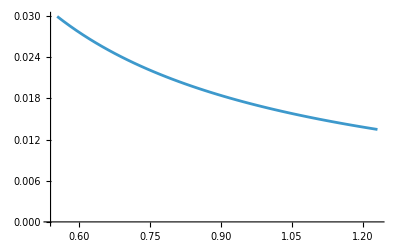

```mathematica
θgrid=Subdivide[θmin,θmax,θpoints];


rt=2000;


ListLinePlot[Partition[Riffle[θgrid,posterior1PMShotByShot[singleShots1PM[rt,r𝒩],model1PM[rt],θmin,θmax,θpoints]],2],PlotRange->All]
```

```mathematica
Total@posterior1PMDiscrete[meas[rt],model1PM[rt],θmin,θmax,θpoints]
```

1.

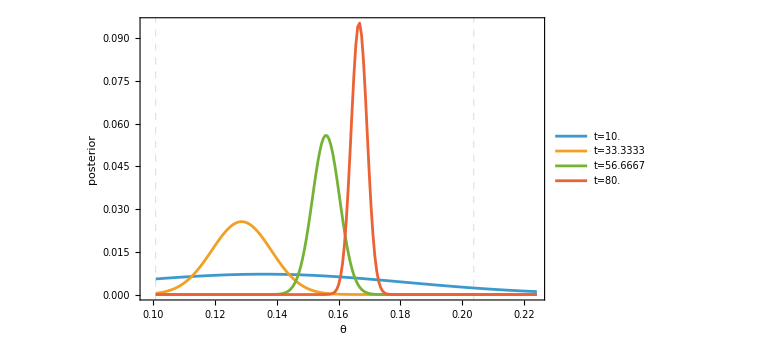

```mathematica
posteriorData[t_]:=Partition[Riffle[θgrid,posterior1PMDiscrete[meas[t],model1PM[t],θmin,θmax,θpoints]],2]

ttable=Subdivide[10,80,3];

ListLinePlot[Table[posteriorData[t],{t,ttable}],PlotRange->All,PlotLegends->Table[StringForm["t=``",t],{t,N@ttable}],Frame->True,FrameLabel->{"θ", "posterior"},ImageSize->Large,GridLines->{{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}},None}]
```

```mathematica
{rT,rTp,teff}
```

{0.100861,10.0861,0.203768}

General::munfl: Exp[-714.83] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-731.848] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-749.068] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

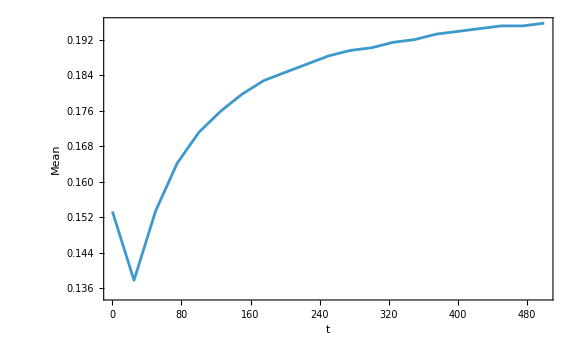
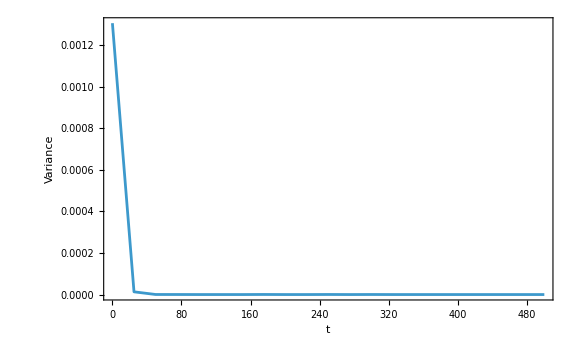

```mathematica
r𝒩=10^12;
tmin=0.1;
tmax=500;
tpoints=20;

meas[t_]:=nmeasurements2[r𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]]



θgrid=Subdivide[θmin,θmax,θpoints];

posteriorMean[t_]:=Total[θgrid Chop@posterior1PMDiscrete[meas[t],model1PM[t],θmin,θmax,θpoints]]

posteriorVariance[t_]:=Total[(θgrid-posteriorMean[t])^2 posterior1PMDiscrete[meas[t],model1PM[t],θmin,θmax,θpoints]]

times=Subdivide[tmin,tmax,tpoints];

{ListLinePlot[Table[{t,posteriorMean[t]},{t,times}],PlotRange->All,Frame->True,FrameLabel->{"t", "Mean"},ImageSize->Large,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}],ListLinePlot[Table[{t,posteriorVariance[t]},{t,times}],PlotRange->All,Frame->True,FrameLabel->{"t", "Variance"},ImageSize->Large,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}]}
```

```mathematica
{rT,rTp,teff}
```

{0.100861,10.0861,0.203768}

General::munfl: Exp[-712.264] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-729.248] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-746.434] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

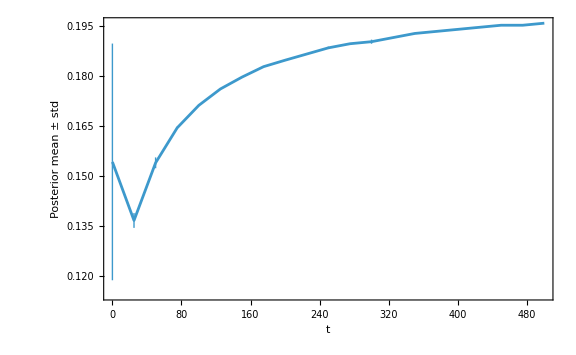

```mathematica
meansWithError=Table[{t,Around[posteriorMean[t],Sqrt[posteriorVariance[t]]]},{t,times}];

ListLinePlot[meansWithError,Frame->True,FrameLabel->{"t","Posterior mean ± std"},ImageSize->Large]
```

```mathematica
tmin=0.1;
tmax=1000;
points=20;

r𝒩=10^15;

times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

meansWithError2=Table[{Exp[t],Around[posteriorMean[Exp[t]],Sqrt[posteriorVariance[Exp[t]]]]},{t,times}];



θestMLE=ParallelTable[{Exp[t],mleGeneral1PM2[meas[Exp[t]],model1PM[Exp[t]],rT]},{t,times}];

θestCrossEntropy=ParallelTable[{Exp[t],thetaEstMLE1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]},{t,times}];

θestKL=ParallelTable[{Exp[t],thetaEstKL1PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]},{t,times}];
```

General::munfl: Exp[-711.875] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-719.875] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.125] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {θ} = {0.}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {θ} = {0.}.

ListLogLinearPlot::ioproc: {{-2.30259,θ},{-1.84207,θ},{-1.38155,0.0905769},{-0.921034,0.0940052},{-0.460517,0.0905624},{0.,0.0941079},{0.460517,0.0951381},{0.921034,0.0963932},{1.38155,0.0984388},{1.84207,0.101455},{2.30259,0.105835},{2.7631,0.111879},{3.22362,0.119743},{3.68414,0.128927},{4.14465,0.139559},{4.60517,0.149603},{5.06569,0.158547},{5.5262,0.165749},{5.98672,0.171994},{6.44724,0.175493},{6.90776,0.177655}} may contain non-machine-precision numbers, complex numbers or invalid entries.

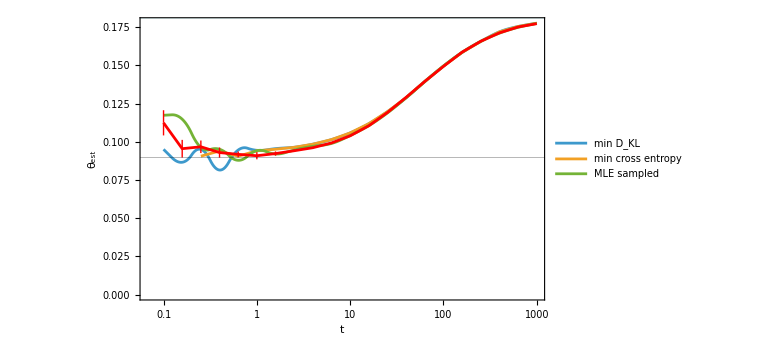

```mathematica
Show[ListLogLinearPlot[{θestKL,θestCrossEntropy,θestMLE},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","MLE sampled"},ImageSize->Large,Joined->True],

ListLogLinearPlot[meansWithError2,Joined->True,PlotStyle->Red,PlotLegends->"Bayesian",Frame->True]]
```

#### 2PM Bayesian

```mathematica
likelihood2PM[θp_,meas_,model_]:=Exp[Sum[meas[[i]] Log[model[[i]]],{i,4}]]/.θ->θp

LogLikelihood2PM[θp_,meas_,model_]:=Sum[meas[[i]] Log[model[[i]]],{i,4}]/.θ->θp


LogLikelihood2PM2[θp_,meas_,model_]:=-crossEntropy2PM[meas,model]/.θ->θp
```

```mathematica
meas2PMtest[t_]:=Flatten@nmeasurements2PM[r𝒩,Pness2PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]


model2PMtest[t_]:=Flatten@PModel2PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]],nγ]



meas2PMtest2[t_]:=nmeasurements2PM[r𝒩,Pness2PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]

model2PMtest2[t_]:=PModel2PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]],nγ]

rt=50;
rθ=0.1;

LogLikelihood2PM[rθ,meas2PMtest[rt],model2PMtest[rt]]//AbsoluteTiming

LogLikelihood2PM2[rθ,meas2PMtest2[rt],model2PMtest2[rt]]//AbsoluteTiming
```

{0.0011667,-8.9417×10^11}

{0.000894,-8.94169×10^11}

```mathematica
posterior2PMDiscrete[meas_,model_,θmin_,θmax_,θpoints_:200]:=Module[{grid,logPostVals,shifted,unnormalizedPosterior},
grid=Subdivide[θmin,θmax,θpoints];
logPostVals=LogLikelihood2PM2[#,meas,model]+Log[priorLogUniform[#,θmin,θmax]]&/@grid;
shifted=logPostVals-Max[logPostVals];
unnormalizedPosterior=Exp[shifted];


unnormalizedPosterior/Total[unnormalizedPosterior]

]
```

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];
nα=0.01;

nγ=10^-3;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];

θmin=0.5*teff;
θmax=1.5*teff;
θpoints=200;
```

```mathematica
r𝒩=10^8;

meas2PM[t_]:=nmeasurements2PM[r𝒩,Pness2PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]

model2PM[t_]:=PModel2PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]],nγ]
```

General::munfl: Exp[-2.7486×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.64383×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.54296×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

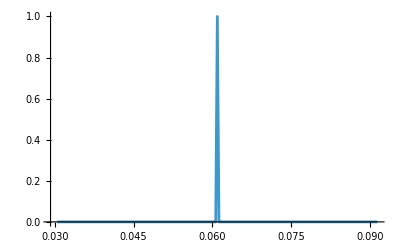

```mathematica
θgrid=Subdivide[θmin,θmax,θpoints];


rt=100000;


ListLinePlot[Partition[Riffle[θgrid,posterior2PMDiscrete[meas2PM[rt],model2PM[rt],θmin,θmax,θpoints]],2],PlotRange->All]
```

```mathematica
{rT,teff}
```

{0.102229,0.206531}

```mathematica
Total@posterior2PMDiscrete[meas2PM[rt],model2PM[rt],θmin,θmax,θpoints]
```

General::munfl: Exp[-2.74579×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.64107×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.54026×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.

General::munfl: Exp[-1.50045×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.44217×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.38573×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

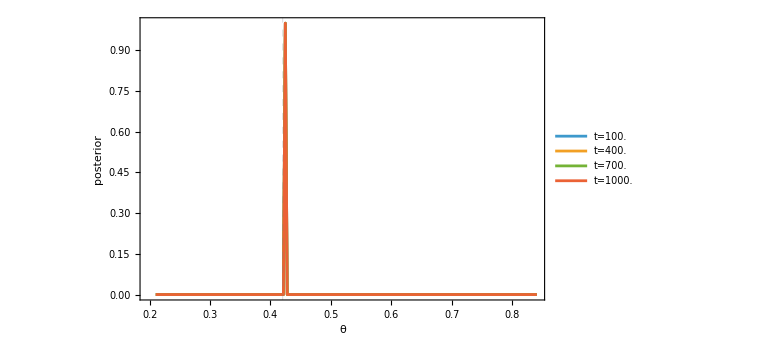

```mathematica
posterior2PMData[t_]:=Partition[Riffle[θgrid,posterior2PMDiscrete[meas2PM[t],model2PM[t],θmin,θmax,θpoints]],2]

ttable=Subdivide[100,1000,3];

ListLinePlot[Table[posterior2PMData[t],{t,ttable}],PlotRange->All,PlotLegends->Table[StringForm["t=``",t],{t,N@ttable}],Frame->True,FrameLabel->{"θ", "posterior"},ImageSize->Large,GridLines->{{{teff,Directive[Thick,Dashed]}},None}]
```

```mathematica
{rT,rTp,teff}
```

{0.208091,20.8091,0.420404}

```mathematica
(*posteriorMean2PM[t_]:=Total[θgrid Chop@posterior2PMDiscrete[meas2PM[t],model2PM[t],θmin,θmax,θpoints]]

posteriorVariance2PM[t_]:=Total[(θgrid-posteriorMean2PM[t])^2 posterior2PMDiscrete[meas2PM[t],model2PM[t],θmin,θmax,θpoints]]*)

posteriorMean2PM[meas_,model_,θmin_,θmax_,θpoints_:200]:=Module[{grid,logPostVals,shifted,unnormalizedPosterior},
grid=Subdivide[θmin,θmax,θpoints];
Total[grid Chop@posterior2PMDiscrete[meas,model,θmin,θmax,θpoints]]

]
posteriorMean2PM::usage="posteriorMean2PM[meas,model,θmin,θmax,θpoints:200] calculates the mean of the posterior distribution P(θ|measurements) on a discrete grid in θ.";

posteriorVariance2PM[meas_,model_,θmin_,θmax_,θpoints_:200]:=Module[{grid,logPostVals,shifted,unnormalizedPosterior},
grid=Subdivide[θmin,θmax,θpoints];
Total[(grid-posteriorMean2PM[meas,model,θmin,θmax,θpoints])^2 posterior2PMDiscrete[meas,model,θmin,θmax,θpoints]]

]
posteriorVariance2PM::usage="posteriorVariance2PM[meas,model,θmin,θmax,θpoints:200] calculates the variance of the posterior distribution P(θ|measurements) on a discrete grid in θ.";
```

```mathematica
r𝒩=10^10;
tmin=1;
tmax=10000;
tpoints=20;



θgrid=Subdivide[θmin,θmax,θpoints];

r𝒩=10^8;

meas2PM[t_]:=nmeasurements2PM[r𝒩,Pness2PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]

model2PM[t_]:=PModel2PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]],nγ]


times=Subdivide[tmin,tmax,tpoints];

(*{ListLinePlot[Table[{t,posteriorMean2PM[meas2PM[t],model2PM[t],θmin,θmax,θpoints]},{t,times}],PlotRange->All,Frame->True,FrameLabel->{"t", "Mean"},ImageSize->Large,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}],ListLinePlot[Table[{t,posteriorVariance2PM[meas2PM[t],model2PM[t],θmin,θmax,θpoints]},{t,times}],PlotRange->All,Frame->True,FrameLabel->{"t", "Variance"},ImageSize->Large]}*)

meansWithError2PM=Table[{t,Around[posteriorMean2PM[meas2PM[t],model2PM[t],θmin,θmax,θpoints],Sqrt[posteriorVariance2PM[meas2PM[t],model2PM[t],θmin,θmax,θpoints]]]},{t,times}];
```

General::munfl: Exp[-2581.99] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2516.77] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2452.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

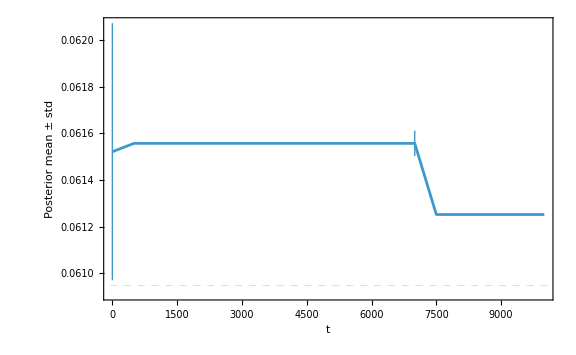

```mathematica
ListLinePlot[meansWithError2PM,Frame->True,FrameLabel->{"t","Posterior mean ± std"},ImageSize->Large,GridLines->{None,{{teff,Directive[Thick,Dashed]}}}]
```

```mathematica
{rT,rTp,teff}
```

{0.284965,28.4965,0.575712}

```mathematica
tmin=1;
tmax=50000;
points=20;

r𝒩=10^10;

times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

meansWithError2=Table[{Exp[t],Around[posteriorMean2PM[meas2PM[Exp[t]],model2PM[Exp[t]],θmin,θmax,θpoints],Sqrt[posteriorVariance2PM[meas2PM[Exp[t]],model2PM[Exp[t]],θmin,θmax,θpoints]]]},{t,times}];


(*θestMLE=ParallelTable[{Exp[t],mleGeneral2PM[Flatten@meas2PM[Exp[t]],Flatten@model2PM[Exp[t]],rT]},{t,times}];*)
θestCrossEntropy=ParallelTable[{Exp[t],thetaEstMLE2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];

θestKL=ParallelTable[{Exp[t],thetaEstKL2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];
```

General::munfl: Exp[-247981.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-241602.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-235354.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

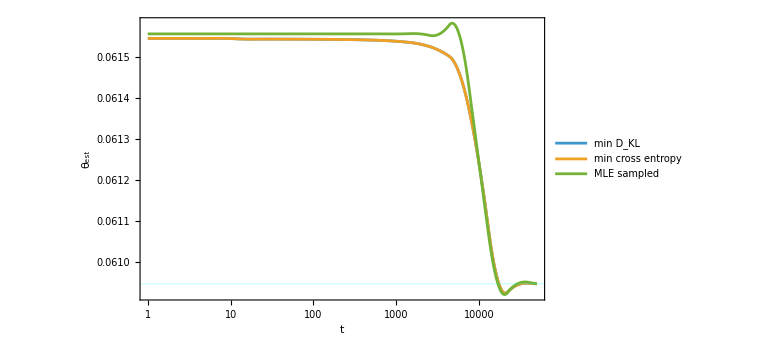

```mathematica
ListLogLinearPlot[{θestKL,θestCrossEntropy,meansWithError2},InterpolationOrder->2,PlotRange->All,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","MLE sampled","Avg posterior"},ImageSize->Large,Joined->True]
```

Now look at estimator averaged over n trial runs

```mathematica
AvgMeanPosteriorEstimates2PM[t_,ntrials_,θmin_,θmax_,θpoints_:200]:=Mean[Table[posteriorMean2PM[meas2PM[t],model2PM[t],θmin,θmax,θpoints],{ntrials}]]



AvgVariancesPosteriorEstimates2PM[t_,ntrials_,θmin_,θmax_,θpoints_:200]:=Mean[ParallelTable[posteriorVariance2PM[meas2PM[t],model2PM[t],θmin,θmax,θpoints],{ntrials}]]
```

```mathematica
tmin=0.1;
tmax=10000;
points=10;

θmin=0.5*teff;
θmax=1.5*teff;
θpoints=200;

times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

r𝒩=10^8;
nTrials=20;



meas2PM[t_]:=nmeasurements2PM[r𝒩,Pness2PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]

model2PM[t_]:=PModel2PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]],nγ]
```

```mathematica
(*Avg[Subscript[θ, Mean]]*)
AvgMeanPosteriorEstimates2PMList=ParallelTable[Quiet@AvgMeanPosteriorEstimates2PM[Exp[t],nTrials,θmin,θmax,θpoints],{t,times}];
ErrorsPosteriorEstimates2PMList=ParallelTable[Quiet[Sqrt[AvgVariancesPosteriorEstimates2PM[Exp[t],nTrials,θmin,θmax,θpoints]]],{t,times}];
(*ErrorsPosteriorEstimatesList=ParallelTable[Quiet[Sqrt[posteriorVariance[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],model1PM[t],θmin,θmax,θpoints]]],{t,times}]*)

AvgMeanPosteriorEstimatesWithErrors2PM=Transpose[{Exp[times],Around@@@Transpose[{AvgMeanPosteriorEstimates2PMList,ErrorsPosteriorEstimates2PMList}]}];
```

```mathematica
(*Avg[Subscript[θ, MLE]]*)
MeanMLEestimatesList2PM=ParallelTable[Quiet@MeanMLEestimates2PM[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ],{t,times}];
ErrorsMLEestimatesList2PM=ParallelTable[Quiet[Sqrt[VariancesMLEestimates2PM[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],{t,times}];

MeanMLEWithErrors2PM=Transpose[{Exp[times],Around@@@Transpose[{MeanMLEestimatesList2PM,ErrorsMLEestimatesList2PM}]}];

θestCrossEntropy2PM=ParallelTable[{Exp[t],thetaEstMLE2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];

θestKL2PM=ParallelTable[{Exp[t],thetaEstKL2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];
```

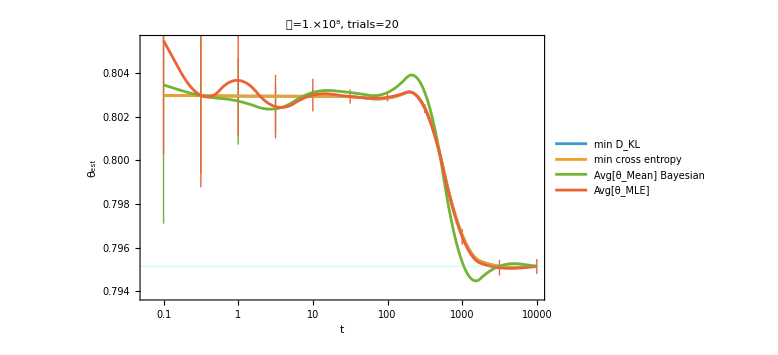

```mathematica
Show[ListLogLinearPlot[{θestKL2PM,θestCrossEntropy2PM,AvgMeanPosteriorEstimatesWithErrors2PM,MeanMLEWithErrors2PM},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","Avg[θ_Mean] Bayesian","Avg[θ_MLE]"},PlotLabel->StringForm["𝒩=``, trials=``",ScientificForm[r𝒩//N],nTrials],ImageSize->Large,Joined->True]]
```

Now lets try different estimates

```mathematica
maxPosteriorEstimator2PM[t_,θmin_,θmax_,θpoints_]:=Module[{posteriorData,θgrid},
θgrid=Subdivide[θmin,θmax,θpoints];
posteriorData=Partition[Riffle[θgrid,posterior2PMDiscrete[meas2PM[t],model2PM[t],θmin,θmax,θpoints]],2];

posteriorData[[Position[posteriorData,Max[posteriorData[[All,2]]]][[1,1]],1]]
]
```

```mathematica
logMeanEstimator2PM[t_,θmin_,θmax_,θpoints_:200]:=Module[{θgrid,logTgrid},

θgrid=Subdivide[θmin,θmax,θpoints];
logTgrid=(Log[#]&/@θgrid);
Exp[Total[logTgrid*Chop[posterior2PMDiscrete[meas2PM[t],model2PM[t],θmin,θmax,θpoints]]]]

]

logMeanVariance2PM[t_,θmin_,θmax_,θpoints_:200]:=Module[{θgrid,logTgrid,logT2grid},

θgrid=Subdivide[θmin,θmax,θpoints];
logTgrid=(Log[#]&/@θgrid);
logT2grid=(Log[#])^2&/@θgrid;


logMeanEstimator2PM[t,θmin,θmax,θpoints]*Sqrt[Total[logT2grid*Chop[posterior2PMDiscrete[meas2PM[t],model2PM[t],θmin,θmax,θpoints]]]-(Total[logTgrid*Chop[posterior2PMDiscrete[meas2PM[t],model2PM[t],θmin,θmax,θpoints]]])^2]


]
```

General::munfl: Exp[-438244.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-427000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-415988.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

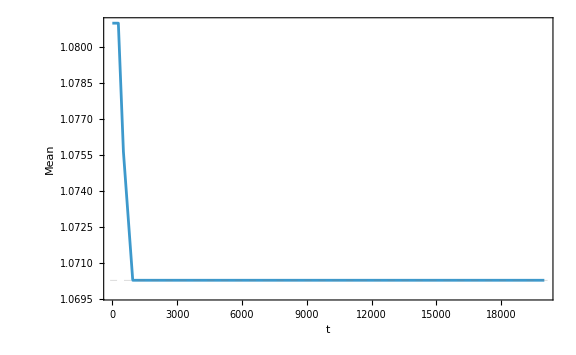
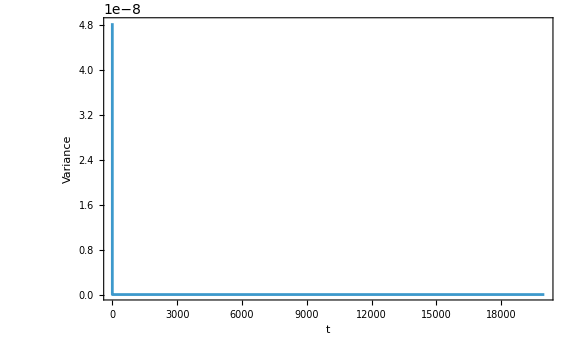

```mathematica
{ListLinePlot[Table[{Exp[t],logMeanEstimator2PM[Exp[t],θmin,θmax,θpoints]},{t,times}],PlotRange->All,Frame->True,FrameLabel->{"t", "Mean"},ImageSize->Large,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}],ListLinePlot[Table[{Exp[t],logMeanVariance2PM[Exp[t],θmin,θmax,θpoints]},{t,times}],PlotRange->All,Frame->True,FrameLabel->{"t", "Variance"},ImageSize->Large,GridLines->{None,{{rT,Directive[Thick,Dashed]},{teff,Directive[Thick,Dashed]}}}]}
```

```mathematica
{rT,rTp,teff}
```

{0.529766,52.9766,1.07028}

General::munfl: Exp[-437082.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-425852.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-414855.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

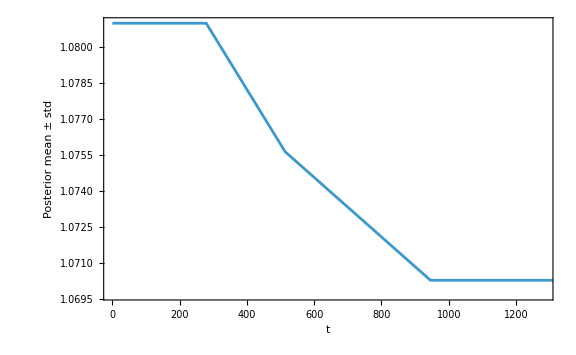

```mathematica
logMeansWithError2PM=Table[{Exp[t],Around[logMeanEstimator2PM[Exp[t],θmin,θmax,θpoints],logMeanVariance2PM[Exp[t],θmin,θmax,θpoints]]},{t,times}];

ListLinePlot[logMeansWithError2PM,Frame->True,FrameLabel->{"t","Posterior mean ± std"},ImageSize->Large]
```

```mathematica
AvgLogMeanPosteriorEstimates2PM[t_,ntrials_,θmin_,θmax_,θpoints_:200]:=Mean[ParallelTable[logMeanEstimator2PM[t,θmin,θmax,θpoints],{ntrials}]]



AvgLogVariancesPosteriorEstimates2PM[t_,ntrials_,θmin_,θmax_,θpoints_:200]:=Mean[ParallelTable[logMeanVariance2PM[t,θmin,θmax,θpoints],{ntrials}]]
```

```mathematica
(*Avg[Subscript[θ, Mean]]*)
AvgLogMeanPosteriorEstimates2PMList=ParallelTable[Quiet@AvgLogMeanPosteriorEstimates2PM[Exp[t],nTrials,θmin,θmax,θpoints],{t,times}];
ErrorsLogPosteriorEstimates2PMList=ParallelTable[Quiet[Sqrt[AvgLogVariancesPosteriorEstimates2PM[Exp[t],nTrials,θmin,θmax,θpoints]]],{t,times}];
(*ErrorsPosteriorEstimatesList=ParallelTable[Quiet[Sqrt[posteriorVariance[nmeasurements2[𝒩,Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],model1PM[t],θmin,θmax,θpoints]]],{t,times}]*)

AvgLogMeanPosteriorEstimatesWithErrors2PM=Transpose[{Exp[times],Around@@@Transpose[{AvgLogMeanPosteriorEstimates2PMList,ErrorsLogPosteriorEstimates2PMList}]}];
```

```mathematica
ErrorsLogPosteriorEstimates2PMList
```

{0.155407+0.0678463 ⅈ,0.153873+0.0485172 ⅈ,0.13748+0.0370397 ⅈ,0.0925561+0.0251629 ⅈ,0.0116515+0.00460301 ⅈ,0.0000175264+5.22667×10^-6 ⅈ,0.,0.,0.050388+0.0502978 ⅈ,0.,0.}

```mathematica
(*Avg[Subscript[θ, MLE]]*)
MeanMLEestimatesList2PM=ParallelTable[Quiet@MeanMLEestimates2PM[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ],{t,times}];
ErrorsMLEestimatesList2PM=ParallelTable[Quiet[Sqrt[VariancesMLEestimates2PM[Exp[t],r𝒩,nTrials,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]],nγ]]],{t,times}];

MeanMLEWithErrors2PM=Transpose[{Exp[times],Around@@@Transpose[{MeanMLEestimatesList2PM,ErrorsMLEestimatesList2PM}]}];

θestCrossEntropy2PM=ParallelTable[{Exp[t],thetaEstMLE2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];

θestKL2PM=ParallelTable[{Exp[t],thetaEstKL2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];
```

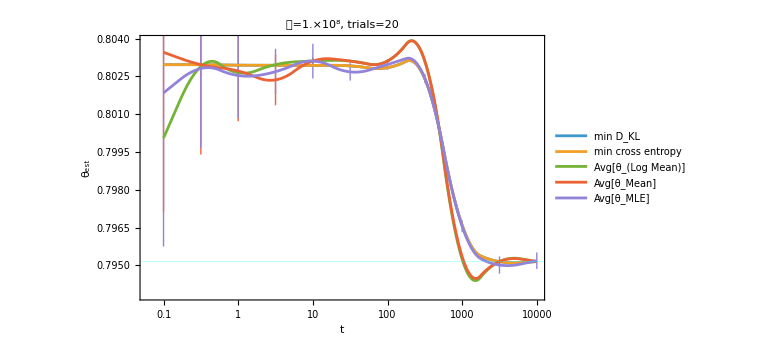

```mathematica
Show[ListLogLinearPlot[{θestKL2PM,θestCrossEntropy2PM,AvgLogMeanPosteriorEstimatesWithErrors2PM,AvgMeanPosteriorEstimatesWithErrors2PM,MeanMLEWithErrors2PM},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","Avg[θ_(Log Mean)]","Avg[θ_Mean]","Avg[θ_MLE]"},PlotLabel->StringForm["𝒩=``, trials=``",ScientificForm[r𝒩//N],nTrials],ImageSize->Large,Joined->True]]
```

### 2PM: short time analytic θ estimates

#### Analytic calculations

```mathematica
Normal@Series[dKL1PMExact[t,θ,ω,T,Tp,α,p1init,p2init,γ,Λ],{t,0,1}]//Simplify
```

0

To first order in time the 1PM has 0 KL divergence

```mathematica
?dKL2PMExact
```

```mathematica
dKL2Pshorttime=Normal@Series[dKL2PMExact[t,θ,ω,T,Tp,α,p1init,p2init,γ,Λ],{t,0,1}]//Simplify;
```

```mathematica
dKL2Pshorttime
```

1/((-1+ⅇ^(ω/T)) (-1+ⅇ^(ω/Tp)) (Λ^2+ω^2))2 t γ Λ^2 ω ((p2init (-ⅇ^(ω/T)+ⅇ^(ω/θ)+ⅇ^((1/Tp+1/θ) ω) (-1+α)-ⅇ^(ω/Tp) α-ⅇ^((1/T+1/Tp+1/θ) ω) α+ⅇ^((1/T+1/Tp) ω) (1+α)))/(-1+ⅇ^(ω/θ))+(p1init (ⅇ^((1/T+1/Tp) ω)-ⅇ^((1/Tp+1/θ) ω)+ⅇ^(ω/T) (-1+α)-α-ⅇ^((1/T+1/θ) ω) α+ⅇ^(ω/θ) (1+α)))/(-1+ⅇ^(ω/θ))+p1init (-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α) Log[((-1+ⅇ^(ω/θ)) (-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α))/((-1+ⅇ^(ω/T)) (-1+ⅇ^(ω/Tp)))]-p2init (ⅇ^(ω/T)+ⅇ^(ω/Tp) α-ⅇ^((1/T+1/Tp) ω) (1+α)) Log[-(ⅇ^(-ω/θ) (-1+ⅇ^(ω/θ)) (ⅇ^(ω/T)+ⅇ^(ω/Tp) α-ⅇ^((1/T+1/Tp) ω) (1+α)))/((-1+ⅇ^(ω/T)) (-1+ⅇ^(ω/Tp)))])

```mathematica
θ/.Last@Solve[D[dKL2Pshorttime,θ]==0,θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ω/Log[1/(2 p1init (-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α))(-ⅇ^(ω/T) p1init+ⅇ^(ω/T+ω/Tp) p1init+p2init-ⅇ^(ω/Tp) p2init-p1init α+ⅇ^(ω/T) p1init α+ⅇ^(ω/Tp) p2init α-ⅇ^(ω/T+ω/Tp) p2init α+√(4 p1init p2init (-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α) (-ⅇ^(ω/T)+ⅇ^(ω/T+ω/Tp)-ⅇ^(ω/Tp) α+ⅇ^(ω/T+ω/Tp) α)+(ⅇ^(ω/T) p1init-ⅇ^(ω/T+ω/Tp) p1init-p2init+ⅇ^(ω/Tp) p2init+p1init α-ⅇ^(ω/T) p1init α-ⅇ^(ω/Tp) p2init α+ⅇ^(ω/T+ω/Tp) p2init α)^2))]

```mathematica
θestdKL2PMshortime[ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=
ω/Log[1/(2 p1init (-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α))(-ⅇ^(ω/T) p1init+ⅇ^(ω/T+ω/Tp) p1init+p2init-ⅇ^(ω/Tp) p2init-p1init α+ⅇ^(ω/T) p1init α+ⅇ^(ω/Tp) p2init α-ⅇ^(ω/T+ω/Tp) p2init α+√(4 p1init p2init (-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α) (-ⅇ^(ω/T)+ⅇ^(ω/T+ω/Tp)-ⅇ^(ω/Tp) α+ⅇ^(ω/T+ω/Tp) α)+(ⅇ^(ω/T) p1init-ⅇ^(ω/T+ω/Tp) p1init-p2init+ⅇ^(ω/Tp) p2init+p1init α-ⅇ^(ω/T) p1init α-ⅇ^(ω/Tp) p2init α+ⅇ^(ω/T+ω/Tp) p2init α)^2))]
```

```mathematica
Collect[Normal@Series[θestdKL2PMshortime[ω,T,Tp,α,p1init,1-p1init,γ,Λ],{Tp,Infinity,0},Assumptions->{ⅇ^(ω/T)>1,α>0}],α,FullSimplify]
```

α (Tp+ω/2-p1init ω)+1/2 ω Coth[ω/(2 T)]

```mathematica
θestdKL2PMshortimeLargeTp[ω_,T_,Tp_,α_,p1init_]:=α (Tp+ω/2-p1init ω)+1/2 ω Coth[ω/(2 T)]
```

Now look at Teff

```mathematica
Teff[ω,T,Tp,α,γ,Λ]
```

-ω/Log[(-(2 (1+1/(-1+ⅇ^(-ω/T))) γ Λ^2 ω)/(Λ^2+ω^2)-(2 (1+1/(-1+ⅇ^(-ω/Tp))) α γ Λ^2 ω)/(Λ^2+ω^2))/((2 (1+1/(-1+ⅇ^(ω/T))) γ Λ^2 ω)/(Λ^2+ω^2)+(2 (1+1/(-1+ⅇ^(ω/Tp))) α γ Λ^2 ω)/(Λ^2+ω^2))]

```mathematica
Series[Teff[ω,T,Tp,α,γ,Λ],{Tp,Infinity,0}]
```

(α Tp)/(1+α)+((1+ⅇ^(ω/T)) ω)/(2 (-1+ⅇ^(ω/T)) (1+α))+O[1/Tp]^1

```mathematica
FullSimplify[Normal@Series[Teff[ω,T,Tp,α,γ,Λ],{Tp,Infinity,0},Assumptions->{ⅇ^(ω/T)>1,α>0}]]
```

(2 Tp α+ω Coth[ω/(2 T)])/(2+2 α)

Now find the θ which minimises the 2PM KL divergence with the model containing a different γ

```mathematica
{{dKL2PMExact2[t_,θ_,ω_,T_,Tp_,α_,γp_,p1init_,p2init_,γ_:1/1000,Λ_:100]:=dKL[Pness2PMExact[t,ω,T,Tp,α,p1init,p2init,γ,Λ],PModel2PMExact[t,θ,ω,p1init,p2init,γp,Λ]];}, {}}
```

{{Null},{Null}}

```mathematica
dKL2Pshorttime2=Normal@Series[dKL2PMExact2[t,θ,ω,T,Tp,α,γp,p1init,p2init,γ,Λ],{t,0,1}]//Simplify;
```

```mathematica
θ/.Last@Solve[D[dKL2Pshorttime2,θ]==0,θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ω/Log[1/(2 p1init (-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α) γ)(-p1init γ+ⅇ^(ω/Tp) p1init γ+ⅇ^(ω/T) p2init γ-ⅇ^(ω/T+ω/Tp) p2init γ-p1init α γ+ⅇ^(ω/T) p1init α γ+ⅇ^(ω/Tp) p2init α γ-ⅇ^(ω/T+ω/Tp) p2init α γ+p1init γp-ⅇ^(ω/T) p1init γp-ⅇ^(ω/Tp) p1init γp+ⅇ^(ω/T+ω/Tp) p1init γp+p2init γp-ⅇ^(ω/T) p2init γp-ⅇ^(ω/Tp) p2init γp+ⅇ^(ω/T+ω/Tp) p2init γp+√(4 p1init p2init (-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α) (-ⅇ^(ω/T)+ⅇ^(ω/T+ω/Tp)-ⅇ^(ω/Tp) α+ⅇ^(ω/T+ω/Tp) α) γ^2+(p1init γ-ⅇ^(ω/Tp) p1init γ-ⅇ^(ω/T) p2init γ+ⅇ^(ω/T+ω/Tp) p2init γ+p1init α γ-ⅇ^(ω/T) p1init α γ-ⅇ^(ω/Tp) p2init α γ+ⅇ^(ω/T+ω/Tp) p2init α γ-p1init γp+ⅇ^(ω/T) p1init γp+ⅇ^(ω/Tp) p1init γp-ⅇ^(ω/T+ω/Tp) p1init γp-p2init γp+ⅇ^(ω/T) p2init γp+ⅇ^(ω/Tp) p2init γp-ⅇ^(ω/T+ω/Tp) p2init γp)^2))]

```mathematica
θestdKL2PMshortime2[ω_,T_,Tp_,α_,γp_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=
ω/Log[1/(2 p1init (-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α) γ)(-p1init γ+ⅇ^(ω/Tp) p1init γ+ⅇ^(ω/T) p2init γ-ⅇ^(ω/T+ω/Tp) p2init γ-p1init α γ+ⅇ^(ω/T) p1init α γ+ⅇ^(ω/Tp) p2init α γ-ⅇ^(ω/T+ω/Tp) p2init α γ+p1init γp-ⅇ^(ω/T) p1init γp-ⅇ^(ω/Tp) p1init γp+ⅇ^(ω/T+ω/Tp) p1init γp+p2init γp-ⅇ^(ω/T) p2init γp-ⅇ^(ω/Tp) p2init γp+ⅇ^(ω/T+ω/Tp) p2init γp+√(4 p1init p2init (-1+ⅇ^(ω/Tp)-α+ⅇ^(ω/T) α) (-ⅇ^(ω/T)+ⅇ^(ω/T+ω/Tp)-ⅇ^(ω/Tp) α+ⅇ^(ω/T+ω/Tp) α) γ^2+(p1init γ-ⅇ^(ω/Tp) p1init γ-ⅇ^(ω/T) p2init γ+ⅇ^(ω/T+ω/Tp) p2init γ+p1init α γ-ⅇ^(ω/T) p1init α γ-ⅇ^(ω/Tp) p2init α γ+ⅇ^(ω/T+ω/Tp) p2init α γ-p1init γp+ⅇ^(ω/T) p1init γp+ⅇ^(ω/Tp) p1init γp-ⅇ^(ω/T+ω/Tp) p1init γp-p2init γp+ⅇ^(ω/T) p2init γp+ⅇ^(ω/Tp) p2init γp-ⅇ^(ω/T+ω/Tp) p2init γp)^2))]
```

```mathematica
Collect[Normal@Series[θestdKL2PMshortime2[ω,T,Tp,α,γp,p1init,1-p1init,γ,Λ],{Tp,Infinity,0},Assumptions->{ⅇ^(ω/T)>1,α>0,γ>0}],α,FullSimplify]
```

-ω/2+p1init ω+((1+1/(-1+ⅇ^(ω/T))-p1init) γ ω)/γp+(α γ (2 Tp+ω-2 p1init ω))/(2 γp)

```mathematica
θestdKL2PMshortime2LargeTp[ω_,T_,Tp_,α_,γr_,p1init_]:=-ω/2+p1init ω+(1+1/(-1+ⅇ^(ω/T))-p1init) γr ω+α γr (Tp+ω/2-p1init ω)
```

```mathematica
Collect[-ω/2+p1init ω+((1+1/(-1+ⅇ^(ω/T))-p1init) γ ω)/γp+(α γ (2 Tp+ω-2 p1init ω))/(2 γp)/.γp->γ,α,FullSimplify]
```

α (Tp+ω/2-p1init ω)+1/2 ω Coth[ω/(2 T)]

```mathematica
Collect[θestdKL2PMshortime2[ω,T,Tp,α,γr,p1init],p1init,FullSimplify]
```

Tp α γr-p1init (-1+γr+α γr) ω+1/2 (-1+(2+2/(-1+ⅇ^(ω/T))+α) γr) ω

Check that this gives the same as before when γ/γ’=γr=1

```mathematica
θestdKL2PMshortime2[ω,T,Tp,α,1,p1init]==θestdKL2PMshortime[ω,T,Tp,α,p1init]//FullSimplify
```

True

Now find the γ’ which minimises the 2PM KL divergence with the model

```mathematica
γp/.Last@Solve[D[dKL2Pshorttime2,γp]==0,γp]
```

((-1+ⅇ^(ω/θ)) (-p1init+ⅇ^(ω/Tp) p1init-ⅇ^(ω/T) p2init+ⅇ^((1/T+1/Tp) ω) p2init-p1init α+ⅇ^(ω/T) p1init α+ⅇ^((1/T+1/Tp) ω) p2init α-ⅇ^(ω/Tp) p2init α) γ)/(p1init-ⅇ^(ω/T) p1init-ⅇ^(ω/Tp) p1init+ⅇ^(ω/T+ω/Tp) p1init-ⅇ^((1/T+1/θ) ω) p2init-ⅇ^((1/Tp+1/θ) ω) p2init+ⅇ^((1/T+1/Tp+1/θ) ω) p2init+ⅇ^(ω/θ) p2init)

```mathematica
Collect[Normal@Series[((-1+ⅇ^(ω/θ)) (-p1init+ⅇ^(ω/Tp) p1init-ⅇ^(ω/T) p2init+ⅇ^((1/T+1/Tp) ω) p2init-p1init α+ⅇ^(ω/T) p1init α+ⅇ^((1/T+1/Tp) ω) p2init α-ⅇ^(ω/Tp) p2init α) γ)/(p1init-ⅇ^(ω/T) p1init-ⅇ^(ω/Tp) p1init+ⅇ^(ω/T+ω/Tp) p1init-ⅇ^((1/T+1/θ) ω) p2init-ⅇ^((1/Tp+1/θ) ω) p2init+ⅇ^((1/T+1/Tp+1/θ) ω) p2init+ⅇ^(ω/θ) p2init)/.p2init->1-p1init,{Tp,Infinity,0},Assumptions->{ⅇ^(ω/T)>1,α>0,γ>0}],α,FullSimplify]
```

((-1+ⅇ^(ω/θ)) (ⅇ^(ω/T) (-1+p1init)-p1init) γ)/((-1+ⅇ^(ω/T)) (ⅇ^(ω/θ) (-1+p1init)-p1init))-((-1+ⅇ^(ω/θ)) α γ (2 Tp+ω-2 p1init ω))/(2 ⅇ^(ω/θ) (-1+p1init) ω-2 p1init ω)

Now find the γ’ which minimises the 2PM KL divergence with the model

```mathematica
Solve[{Simplify@D[dKL2Pshorttime2,θ]==0&&Simplify@D[dKL2Pshorttime2,γp]==0},{θ,γp}]
```

$Aborted

```mathematica
dKL[PModel2PMExact[t,teff,ω,p1init,p2init,γ,Λ],PModel2PMExact[t,θ,ω,p1init,p2init,γp,Λ]];
```

```mathematica
Normal@Series[,{t,0,1}]//Simplify
```

1/((-1+ⅇ^(ω/teff)) (-1+ⅇ^(ω/θ)) (Λ^2+ω^2))2 t Λ^2 ω (p1init γ-ⅇ^(ω/θ) p1init γ+ⅇ^(ω/teff) p2init γ-ⅇ^((1/teff+1/θ) ω) p2init γ-p1init γp+ⅇ^(ω/teff) p1init γp+ⅇ^((1/teff+1/θ) ω) p2init γp-ⅇ^(ω/θ) p2init γp+(-1+ⅇ^(ω/θ)) p1init γ Log[((-1+ⅇ^(ω/θ)) γ)/((-1+ⅇ^(ω/teff)) γp)]+ⅇ^(ω/teff) (-1+ⅇ^(ω/θ)) p2init γ Log[(ⅇ^((1/teff-1/θ) ω) (-1+ⅇ^(ω/θ)) γ)/((-1+ⅇ^(ω/teff)) γp)])

```mathematica
/.{θ->teff,γp->γ}
```

0

```mathematica
D[,{θ,1},{γp,1}]//Simplify
```

(2 ⅇ^(ω/θ) (p1init+p2init) t Λ^2 ω^2)/((-1+ⅇ^(ω/θ))^2 θ^2 (Λ^2+ω^2))

```mathematica
Solve[{Simplify@D[,θ]==0&&Simplify@D[,γp]==0},{θ,γp}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→teff,γp→γ}}

#### Numerical checks

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
(*init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];*)
(*init=randomPureDensityMatrix[2];*)
nα=0.1;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];

rt=0.1;

nruns=20;
```

Short time divergence

```mathematica
Mean@Table[With[{init=randomPureDensityMatrix[2]},
thetaEstKL2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]],{nruns}]
```

4.75833

Compare with analytical formulae

```mathematica
Mean@Table[With[{init=randomPureDensityMatrix[2]},
Re@θestdKL2PMshortime[rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]]]],{nruns}]
```

4.75845

```mathematica
Mean@Table[With[{init=randomPureDensityMatrix[2]},
Re@θestdKL2PMshortime2[rϵ[[2]]-rϵ[[1]],rT,rTp,nα,1.1,init[[2,2]]]],{nruns}]
```

5.23726

#### Estimating parameters

```mathematica
rϵ=RandomReal[{},2]//Sort;
{rT,rTp}={(rϵ[[2]]-rϵ[[1]]),100(rϵ[[2]]-rϵ[[1]])}//Sort;
(*init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];*)
(*init=randomPureDensityMatrix[2];*)
nα=0.1;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα];

rt=0.1;

nruns=20;
```

```mathematica
Mean@Table[With[{init=randomPureDensityMatrix[2]},
thetaEstKL2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]],{nruns}]
```

4.75107

```mathematica
θestdKL2PMshortime2[rϵ[[2]]-rϵ[[1]],rT,Tp,α,γr,p1init]
```

-0.214648+0.429297 p1init+0.429297 (1.58198-p1init) γr+(0.214648-0.429297 p1init+Tp) α γr

```mathematica
Table[With[{init=randomPureDensityMatrix[2]},
thetaEstKL2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]==θestdKL2PMshortime2[rϵ[[2]]-rϵ[[1]],rT,Tp,α,γr,init[[2,2]]]],{3}]
```

{4.75401==(-0.00715589+0. ⅈ)+(0.471645+0. ⅈ) γr+((0.00715589+0. ⅈ)+Tp) α γr,4.73947==(0.142411+0. ⅈ)+(0.322079+0. ⅈ) γr+((-0.142411+0. ⅈ)+Tp) α γr,4.74268==(0.108589+0. ⅈ)+(0.3559+0. ⅈ) γr+((-0.108589+0. ⅈ)+Tp) α γr}

```mathematica
Solve[Table[With[{init=randomPureDensityMatrix[2]},
thetaEstKL2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]==θestdKL2PMshortime2[rϵ[[2]]-rϵ[[1]],rT,Tp,α,γr,init[[2,2]]]],{3}],{Tp,α,γr}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Tp→0.464489,α→-1.,γr→-4.84204×10^12}}

```mathematica
Solve[Table[With[{init=randomPureDensityMatrix[2]},
thetaEstKL2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]==θestdKL2PMshortime2[rϵ[[2]]-rϵ[[1]],rT,Tp,nα,1,init[[2,2]]]],{1}],{Tp}]
rTp
```

{{Tp→42.8881+0. ⅈ}}

42.9297

```mathematica
Solve[Table[With[{init=randomPureDensityMatrix[2]},
thetaEstKL2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]==θestdKL2PMshortime2[rϵ[[2]]-rϵ[[1]],rT,rTp,α,1,init[[2,2]]]],{1}],{α}]
nα
```

{{α→0.0999047+0. ⅈ}}

0.1

```mathematica
Solve[Table[With[{init=randomPureDensityMatrix[2]},
thetaEstKL2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]==θestdKL2PMshortime2[rϵ[[2]]-rϵ[[1]],rT,rTp,nα,γr,init[[2,2]]]],{1}],{γr}]
```

{{γr→0.999161+0. ⅈ}}

```mathematica
Solve[Table[With[{init=randomPureDensityMatrix[2]},
thetaEstKL2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]==θestdKL2PMshortime2[rϵ[[2]]-rϵ[[1]],rT,Tp,α,1,init[[2,2]]]],{2}],{Tp,α}]

Solve[Table[With[{init=randomPureDensityMatrix[2]},
thetaEstKL2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]==θestdKL2PMshortime2[rϵ[[2]]-rϵ[[1]],rT,Tp,nα,γr,init[[2,2]]]],{2}],{Tp,γr}]

Solve[Table[With[{init=randomPureDensityMatrix[2]},
thetaEstKL2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]==θestdKL2PMshortime2[rϵ[[2]]-rϵ[[1]],rT,rTp,α,γr,init[[2,2]]]],{2}],{α,γr}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Tp→43.7997,α→0.0979175}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Tp→42.7909,γr→1.00208}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→0.10011,γr→0.998238}}

```mathematica
Solve[Table[With[{init=randomPureDensityMatrix[2],rϵ=RandomReal[{},2]//Sort},
thetaEstKL2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]==θestdKL2PMshortime2[rϵ[[2]]-rϵ[[1]],rT,Tp,α,γr,init[[2,2]]]],{3}],{Tp,α,γr}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Tp→4.05914,α→0.311844,γr→0.886417}}

```mathematica
rt=0.1;
nα=0.1;
rTp=300;


(*SeedRandom[1234];*)

(*number of simulated runs*)
nRuns=20;

(*Build dataset:each element is {{p1,gap},thetaExact}*)
data=Table[Module[{init,rε,gap,p1,theta},init=randomPureDensityMatrix[2];
rε=Sort@RandomReal[{0,2},2];
gap=rε[[2]]-rε[[1]];
p1=init[[2,2]];
(*compute the "exact" measured theta for this run*)theta=thetaEstKL2PMExact[rt,gap,rT,rTp,nα,p1,1-p1];
{{p1,gap},theta}],{nRuns}];

(*define a numeric model function for a single datapoint*)modelFunction[Tp_?NumericQ,alpha_?NumericQ,GammaR_?NumericQ,p1_?NumericQ,gap_?NumericQ]:=Module[{nb},nb=1/(Exp[gap/rT]-1);
-(gap/2)+gap*p1+gap*(1+nb-p1)*GammaR+(gap/2-gap*p1+Tp)*alpha*GammaR];

(*loss=sum of squared residuals over the dataset*)
loss[Tp_?NumericQ,alpha_?NumericQ,GammaR_?NumericQ]:=Total[(#[[2]]-modelFunction[Tp,alpha,GammaR,#[[1,1]],#[[1,2]]])^2&/@Re@data];

(*minimize with positivity bounds (change initial guesses as appropriate)*)
sol=FindMinimum[{loss[Tp,alpha,GammaR],Tp>0,alpha>0,GammaR>0},{{Tp,rTp},{alpha,nα},{GammaR,1}} (*robust global search;try others if slow*)]

NMinimize[{loss[Tp,alpha,GammaR],Tp>0,alpha>0,GammaR>0},{Tp,alpha,GammaR},Method->"DifferentialEvolution"  (*robust global search;try others if slow*)]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{0.0000972398,{Tp→298.011,alpha→0.101144,GammaR→0.995252}}

{0.000737753,{Tp→194.454,alpha→0.159107,GammaR→0.96989}}

### 2PM: Min D_KLover γ and θ model for qubit

#### Definitions

```mathematica
(*MLE objective function (negative log-likelihood)*)
negLogLikelihood1PMExactθandγ[t_,θ_,γmod_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=crossEntropy[Pness1PMExact[t,ω,T,Tp,α,p1init,p2init,γ,Λ],PModel1PMExact[t,θ,ω,p1init,p2init,γmod,Λ]]


(*thetaEstMLEExact[t_]:=θ/. Last[NMinimize[{negLogLikelihoodExact[t,θ],10^-3*rT<θ<2*teff},θ]]*)
θandγEstMLE1PMExact[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:={θ,γ}/. Last[FindMinimum[negLogLikelihood1PMExactθandγ[t,θ,γmod,ω,T,Tp,α,p1init,p2init,γ,Λ],{{θ,teff},{γmod,α}},Method->"PrincipalAxis",WorkingPrecision->MachinePrecision,AccuracyGoal->6]]
(*thetaEstMLEExact[t_]:=θ/. Last[ FindMinimum[negLogLikelihoodExact[t,θ],{θ,rT,teff}]]*)


dKL1PMExactθandγ[t_,θ_,γmod_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=dKL1PM[Pness1PMExact[t,ω,T,Tp,α,p1init,p2init,γ,Λ],PModel1PMExact[t,θ,ω,p1init,p2init,γmod,Λ]]

(*KL estimate (minimize KL divergence)*)
(*thetaEstKLExact[t_]:=θ/. Last[NMinimize[{klObjectiveExact[t,θ],10^-3*rT<θ<2*teff},θ]]*)
θandγEstKL1PMExact[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:={θ,γ}/. Last[FindMinimum[dKL1PMExactθandγ[t,θ,γmod,ω,T,Tp,α,p1init,p2init,γ,Λ],{{θ,teff},{γmod,α}},Method->"PrincipalAxis",WorkingPrecision->MachinePrecision,AccuracyGoal->6]]
(*thetaEstKLExact[t_]:=θ/. Last[FindMinimum[klObjectiveExact[t,θ],{θ,rT,teff}]]*)
```

```mathematica
θandγEstMLE1PMExact[100,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]
θandγEstKL1PMExact[100,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]
```

{2.34976,1/1000}

{2.34976,1/1000}

```mathematica
(*MLE objective function (negative log-likelihood)*)
negLogLikelihood2PMExactθandγ[t_,θ_,γmod_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=crossEntropy2PM[Pness2PMExact[t,ω,T,Tp,α,p1init,p2init,γ,Λ],PModel2PMExact[t,θ,ω,p1init,p2init,γmod,Λ]]

(*thetaEstMLEExact[t_]:=θ/. Last[NMinimize[{negLogLikelihoodExact[t,θ],10^-3*rT<θ<2*teff},θ]]*)
θandγEstMLE2PMExact[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:={θ,γ}/.Last[FindMinimum[{negLogLikelihood2PMExactθandγ[t,θ,γmod,ω,T,Tp,α,p1init,p2init,γ,Λ],θ>0,10^-5<γmod<10^-1},{{θ,teff},{γmod,γ}},WorkingPrecision->MachinePrecision,AccuracyGoal->6]]

(*θandγEstMLE2PMExact2[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=ArgMin[{negLogLikelihood2PMExactθandγ[t,θ,γmod,ω,T,Tp,α,p1init,p2init,γ,Λ],0<θ,10^-5<γmod<10^-1},{θ,γmod},WorkingPrecision->MachinePrecision]*)




dKL2PMExactθandγ[t_,θ_,γmod_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=dKL[Pness2PMExact[t,ω,T,Tp,α,p1init,p2init,γ,Λ],PModel2PMExact[t,θ,ω,p1init,p2init,γmod,Λ]];


(*KL estimate (minimize KL divergence)*)
(*thetaEstKLExact[t_]:=θ/. Last[NMinimize[{klObjectiveExact[t,θ],10^-3*rT<θ<2*teff},θ]]*)
θandγEstKL2PMExact[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:={θ,γ}/. Last[FindMinimum[{dKL2PMExactθandγ[t,θ,γmod,ω,T,Tp,α,p1init,p2init,γ,Λ],θ>0,10^-5<γmod<10^-1},{{θ,teff},{γmod,γ}},WorkingPrecision->MachinePrecision,AccuracyGoal->6]]

(*θandγEstKL2PMExact2[t_,ω_,T_,Tp_,α_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=ArgMin[{dKL2PMExactθandγ[t,θ,γmod,ω,T,Tp,α,p1init,p2init,γ,Λ],0<θ,10^-5<γmod<10^-1},{θ,γmod}]*)


(*thetaEstKLExact[t_]:=θ/. Last[FindMinimum[klObjectiveExact[t,θ],{θ,rT,teff}]]*)
```

#### Plots

```mathematica
nt=10000;

γmin=10^-4;
γmax=10^-2;
out=ParallelTable[{γ,θ,negLogLikelihood2PMExactθandγ[nt,θ,γ,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{γ,γmin,γmax,(γmax-γmin)/10},{θ,0.5teff,1.5teff,(1.5teff-0.5teff)/10}];

ListPlot3D[Partition[Flatten[out],3],AxesLabel->{"γ", "θ", logℒ},PlotRange->All]

FindArgMin[{negLogLikelihood2PMExactθandγ[nt,θ,γmod,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],0<θ,0<γmod<0.1},{{θ,teff},{γmod,nα}}]
Last[FindMinimum[{negLogLikelihood2PMExactθandγ[nt,θ,γmod,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],1>γmod>0},{{θ,teff},{γmod,nα}},AccuracyGoal->6]]
```

-Graphics3D-

{0.875713,0.0276298}

{θ→0.875711,γmod→0.140906}

```mathematica
Last[FindMinimum[{negLogLikelihood2PMExactθandγ[10000,θ,γmod,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],10^-5<γmod<10^-1},{{θ,teff},{γmod,10^-3}},AccuracyGoal->6]]
```

{θ→0.875711,γmod→0.0089069}

```mathematica
teff
```

0.875711

```mathematica
r𝒩=10^8;
MLEsamples=10;

(*meas[t_]:=1/r𝒩 Sort[measurementsn[r𝒩,Sort[Diagonal[ρQubitExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]],#1>#2&],2],#2>#1&]*)

meas2PM[t_]:=1/r𝒩 nmeasurements2[r𝒩,Flatten[Pness2PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]]

(*meas[t_]:=Flatten[Pness2PMExact[t,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]]*)

times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

model2PM[t_]:=Flatten[PModel2PMExact[t,θ,rϵ[[2]]-rϵ[[1]],init[[2,2]],init[[1,1]]]]


(*θestMLE=ParallelTable[{Exp[t],mleGeneral1PM2[meas[Exp[t]],model1PM[Exp[t]],teff]},{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];*)

(*θestMLE=ParallelTable[{Exp[t],Mean[Table[mleGeneral2PM[meas2PM[Exp[t]],model2PM[Exp[t]],rT],{MLEsamples}]]},{t,times}];*)

θestCrossEntropy=ParallelTable[{Exp[t],thetaEstMLE2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];

θestKL=ParallelTable[{Exp[t],thetaEstKL2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{t,times}];
```

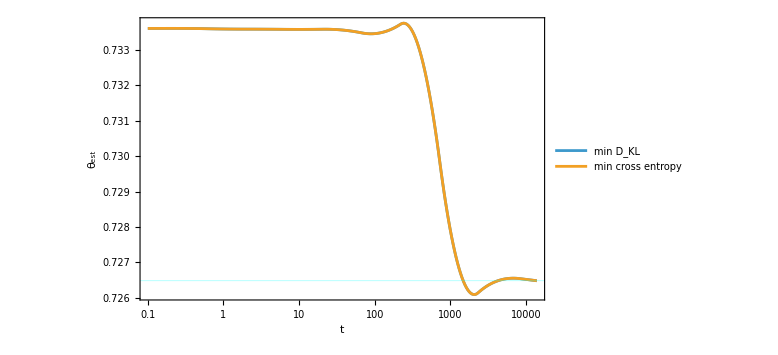

```mathematica
ListLogLinearPlot[{θestKL,θestCrossEntropy},InterpolationOrder->2,PlotRange->All,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}},Frame->True,FrameLabel->{"t","θ_est"},PlotLegends->{"min D_KL","min cross entropy","MLE sampled"},ImageSize->Large,Joined->True]
```

```mathematica
tmin=10;
times=Table[t,{t,Log@tmin,Log@tmax,(Log@tmax-Log@tmin)/points}];

θandγestMLE2PM=ParallelTable[θandγEstMLE2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],{t,times}];

θandγestKL2PM=ParallelTable[θandγEstKL2PMExact[Exp[t],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]],{t,times}];
```

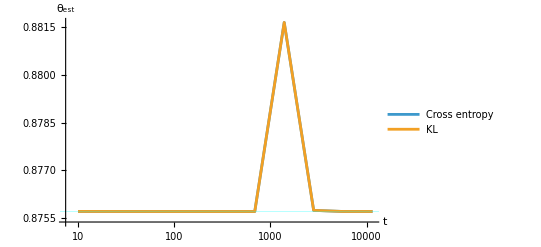

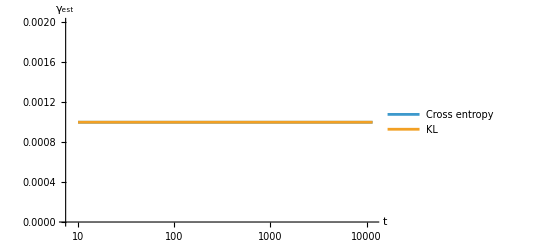

```mathematica
ListLogLinearPlot[{Partition[Riffle[Exp[times],θandγestMLE2PM[[All,1]]],2],Partition[Riffle[Exp[times],θandγestKL2PM[[All,1]]],2]},PlotRange->All,AxesLabel->{"t","θ_est"},Joined->True,GridLines->{None,{{teff,Directive[Thick,Cyan]}}},PlotLegends->{"Cross entropy","KL"}]

ListLogLinearPlot[{Partition[Riffle[Exp[times],θandγestMLE2PM[[All,2]]],2],Partition[Riffle[Exp[times],θandγestKL2PM[[All,2]]],2]},PlotRange->All,AxesLabel->{"t","γ_est"},Joined->True,PlotLegends->{"Cross entropy","KL"}]
```

```mathematica
negLogLikelihood2PMExactθandγ[1391,0.88164,0.001,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]
negLogLikelihood2PMExactθandγ[1391,0.8757,0.001,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]
```

1.35693

1.35693

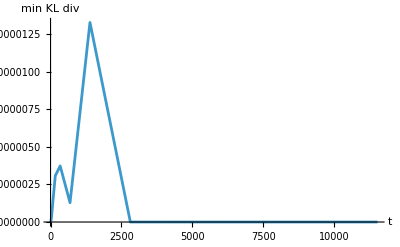

```mathematica
ListLinePlot[ParallelTable[{Exp[times][[i]],dKL1PMExactθandγ[Exp[times][[i]],θandγestMLE2PM[[All,1]][[i]],θandγestMLE2PM[[All,2]][[i]],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{i,Length[times]}],PlotRange->All,AxesLabel->{"t","min KL div"}]
(*
ListLinePlot[ParallelTable[{Exp[times][[i]],dKL1PMExactθandγ[Exp[times][[i]],θandγestKL2PM[[All,1]][[i]],θandγestKL2PM[[All,2]][[i]],rϵ[[2]]-rϵ[[1]],rT,rTp,nα,init[[2,2]],init[[1,1]]]},{i,Length[times]}],PlotRange->All,AxesLabel->{"t","min KL div"}]*)
```

### 2PM: Finding effective γ and T

#### Definitions

```mathematica
?ρQubitExact
```

```mathematica
(*PConditional2PMExact[t_,ω_,T_,Tp_,α_,γ_:10^-3,Λ_:10^2]:={Diagonal[ρQubitExact[t,ω,T,Tp,α,0,1,γ,Λ]],Diagonal[ρQubitExact[t,ω,T,Tp,α,1,0,γ,Λ]]};*)

PConditional2PMExact[t_,ω_,T_,Tp_,α_,γ_,Λ_:10^2]:={{p2Qubit[t,ω,T,Tp,α,0,1,γ,Λ],p1Qubit[t,ω,T,Tp,α,0,1,γ,Λ]},{p2Qubit[t,ω,T,Tp,α,1,0,γ,Λ],p1Qubit[t,ω,T,Tp,α,1,0,γ,Λ]}}



(*PConditionalModel2PMExact[t_,θ_,ω_,γ_:10^-3,Λ_:10^2]:={Diagonal[ρQubitExact[t,ω,θ,1,0,0,1,γ,Λ]],Diagonal[ρQubitExact[t,ω,θ,1,0,1,0,γ,Λ]]};*)

PConditionalModel2PMExact[t_,θ_,ω_,γ_,Λ_:10^2]:={{p2Qubit[t,ω,θ,Tp,0,0,1,γ,Λ],p1Qubit[t,ω,θ,Tp,0,0,1,γ,Λ]},{p2Qubit[t,ω,θ,Tp,0,1,0,γ,Λ],p1Qubit[t,ω,θ,Tp,0,1,0,γ,Λ]}};
```

```mathematica
nBose[ω_,θ_]:=1/(Exp[ω/θ]-1)
```

```mathematica
{{-Γm,Γp},{Γm,-Γp}}//MatrixForm
```

(-Γm | Γp
Γm | -Γp)

```mathematica
Eigensystem[t{{-Γm,Γp},{Γm,-Γp}}]
```

{{0,t (-Γm-Γp)},{{Γp/Γm,1},{-1,1}}}

```mathematica
PConditional2PMAnalytic=MatrixExp[t{{-Γm,Γp},{Γm,-Γp}}]//Simplify
```

{{(ⅇ^(-t (Γm+Γp)) Γm+Γp)/(Γm+Γp),(Γp-ⅇ^(-t (Γm+Γp)) Γp)/(Γm+Γp)},{(Γm-ⅇ^(-t (Γm+Γp)) Γm)/(Γm+Γp),(Γm+ⅇ^(-t (Γm+Γp)) Γp)/(Γm+Γp)}}

```mathematica
PConditional2PMAnalytic//MatrixForm
```

((ⅇ^(-t (Γm+Γp)) Γm+Γp)/(Γm+Γp) | (Γp-ⅇ^(-t (Γm+Γp)) Γp)/(Γm+Γp)
(Γm-ⅇ^(-t (Γm+Γp)) Γm)/(Γm+Γp) | (Γm+ⅇ^(-t (Γm+Γp)) Γp)/(Γm+Γp))

```mathematica
PConditional2PMAnalytic//Eigenvalues
```

{ⅇ^(-t (Γm+Γp)),1}

```mathematica
Normal@Asymptotic[PConditional2PMAnalytic,t->Infinity]//MatrixForm
```

(Γp/(Γm+Γp) | Γp/(Γm+Γp)
Γm/(Γm+Γp) | Γm/(Γm+Γp))

```mathematica
Solve[{(Γp-ⅇ^(-t (Γm+Γp)) Γp)/(Γm+Γp)==p21,(Γm-ⅇ^(-t (Γm+Γp)) Γm)/(Γm+Γp)==p12},{Γp,Γm}]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Γp→(p21 Log[-1/(-1+p12+p21)])/(p12 t+p21 t),Γm→(p12 Log[-1/(-1+p12+p21)])/(p12 t+p21 t)}}

```mathematica
Reduce[{(Γp-ⅇ^(-t (Γm+Γp)) Γp)/(Γm+Γp)==p21,(Γm-ⅇ^(-t (Γm+Γp)) Γm)/(Γm+Γp)==p12},{Γp,Γm},PositiveReals]
```

0<p12<1&&0<p21<1-p12&&t>0&&Γp==(p21 Log[-1/(-1+p12+p21)])/(p12 t+p21 t)&&Γm==(-t Γp+Log[-1/(-1+p12+p21)])/t

```mathematica
(p21 Log[-1/(-1+p12+p21)])/(p12 t+p21 t)/((p12 Log[-1/(-1+p12+p21)])/(p12 t+p21 t))//Simplify (*exp(-ω/θ)*)
(p12 Log[-1/(-1+p12+p21)])/(p12 t+p21 t)-(p21 Log[-1/(-1+p12+p21)])/(p12 t+p21 t)//Simplify (*J = Γm-Γp*)
```

p21/p12

((p12-p21) Log[-1/(-1+p12+p21)])/((p12+p21) t)

Check these formulae

```mathematica
(Γp-ⅇ^(-t (Γm+Γp)) Γp)/(Γm+Γp)/((Γm-ⅇ^(-t (Γm+Γp)) Γm)/(Γm+Γp))//Simplify
```

Γp/Γm

```mathematica
(((Γm-ⅇ^(-t (Γm+Γp)) Γm)/(Γm+Γp)-(Γp-ⅇ^(-t (Γm+Γp)) Γp)/(Γm+Γp)) Log[-1/(-1+(Γm-ⅇ^(-t (Γm+Γp)) Γm)/(Γm+Γp)+(Γp-ⅇ^(-t (Γm+Γp)) Γp)/(Γm+Γp))])/(((Γm-ⅇ^(-t (Γm+Γp)) Γm)/(Γm+Γp)+(Γp-ⅇ^(-t (Γm+Γp)) Γp)/(Γm+Γp)) t)//Simplify
```

((Γm-Γp) Log[ⅇ^(t (Γm+Γp))])/(t (Γm+Γp))

```mathematica
rt=1;
PConditional2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,nγ,nΛ][[1,2]]
1-PConditional2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,nγ,nΛ][[2,1]]
```

0.846631

0.929974

```mathematica
FindEffectiveModelFromJointDist[jointDistData_,t_,ω_,p1init_,p2init_,Λ_:10^2]:=Module[{jointDistModel},

jointDistModel=PModel2PMExact[t,θ,ω,Re@p1init,Re@p2init,γ,Λ];

(*First@NSolveValues[{jointDistData[[1,1]]==jointDistModel[[1,1]]&&jointDistData[[2,2]]==jointDistModel[[2,2]]&&θ>0&&γ>0},{θ,γ}]*)

{θ,γ}/.FindRoot[{jointDistData[[1,1]]==jointDistModel[[1,1]]&&jointDistData[[2,2]]==jointDistModel[[2,2]]},{{θ,1},{γ,0.5}}]

]


FindEffectiveModelFromConditionalDist[conditionalDistData_,t_,ω_,Λ_:10^4]:=Module[{Πdata,θeff,Γeff,γeff},


Πdata=MatrixLog[conditionalDistData]/t;

θeff=-ω/Log[Πdata[[2,1]]/Πdata[[1,2]]];

Γeff=Πdata[[2,1]]*(Exp[ω/θeff]-1);

(*γeff=Γeff/(2J[ω,1,Λ]);*) (*Only works if J is proportional to γ*)

γeff=γ/.First@NSolve[Γeff==2J[ω,γ,Λ],γ];

{θeff,γeff}

]

FindEffectiveModelFromConditionalDist2[conditionalDistData_,t_,ω_,Λ_:10^4]:=Module[{Πdata,θeff,Γeff,γeff},

(*Πdata=MatrixLog[conditionalDistData+10^-12 IdentityMatrix[2]]/t;*)

θeff=-ω/Log[conditionalDistData[[2,1]]/conditionalDistData[[1,2]]];

Γeff=((conditionalDistData[[1,2]]-conditionalDistData[[2,1]]) Log[-1/(-1+conditionalDistData[[1,2]]+conditionalDistData[[2,1]])])/((conditionalDistData[[1,2]]+conditionalDistData[[2,1]]) t);

(*γeff=Γeff/(2J[ω,1,Λ]);*) (*Only works if J is proportional to γ*)

γeff=γ/.First@NSolve[Γeff==2J[ω,γ,Λ],γ];

{θeff,γeff}

]

FindEffectiveModelFromConditionalDist3[conditionalDistData_,t_,ω_,Λ_:10^4]:=Module[{conditionalDistModel},

conditionalDistModel=PConditionalModel2PMExact[t,θ,ω,γ,Λ];

(*First@NSolveValues[{conditionalDistData[[1,1]]==conditionalDistModel[[1,1]]&&conditionalDistData[[2,2]]==conditionalDistModel[[2,2]]&&θ>0&&γ>0},{θ,γ}]*)

{θ,γ}/.FindRoot[{conditionalDistData[[1,1]]==conditionalDistModel[[1,1]]&&conditionalDistData[[2,2]]==conditionalDistModel[[2,2]]},{{θ,10},{γ,0.2}}]

]
```

#### Calculations and Plots (including sampling)

```mathematica
{rT,rTp}={1,100};

rϵ=RandomReal[{rTp},2]//Sort;
(*rϵ={1,150};*)


nα=0.01;
nγ=0.1;
nΛ=10^4;

teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα]

rt=0.1;
```

12.6858

```mathematica
rt=10;

ConditionalDistData=PConditional2PMExact[rt,rϵ[[2]]-rϵ[[1]],rT,rTp,nα,nγ,nΛ];

{θefftest,γefftest}=FindEffectiveModelFromConditionalDist[ConditionalDistData,rt,rϵ[[2]]-rϵ[[1]]]

{θefftest,γefftest}=FindEffectiveModelFromConditionalDist2[ConditionalDistData,rt,rϵ[[2]]-rϵ[[1]]]
```

{3.30906,0.101}

{3.30906,0.101}

```mathematica
Πeff=({{-2J[rϵ[[2]]-rϵ[[1]],γefftest,nΛ](1+nBose[rϵ[[2]]-rϵ[[1]],θefftest]), 2J[rϵ[[2]]-rϵ[[1]],γefftest,nΛ](1+nBose[rϵ[[2]]-rϵ[[1]],θefftest])}, {2J[rϵ[[2]]-rϵ[[1]],γefftest,nΛ](nBose[rϵ[[2]]-rϵ[[1]],θefftest]), -2J[rϵ[[2]]-rϵ[[1]],γefftest,nΛ](nBose[rϵ[[2]]-rϵ[[1]],θefftest])}});

MatrixExp[rt*Πeff]//MatrixForm

ConditionalDistData//MatrixForm

PConditionalModel2PMExact[rt,θefftest,rϵ[[2]]-rϵ[[1]],γefftest]//MatrixForm
```

(0.0671356 | 0.932864
0.0671356 | 0.932864)

(0.0671356 | 0.932864
0.0671356 | 0.932864)

(0.0671356 | 0.932864
0.0671356 | 0.932864)

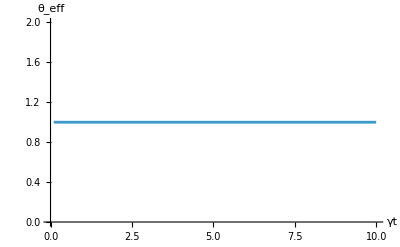
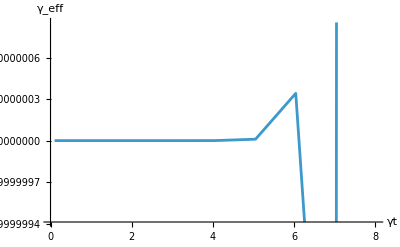

```mathematica
rω=1;

{rT,rTp}={1,100};
nγ=0.1;
nα=0.01;
nΛ=10^4;

tmin=0.1;
tmax=10;
tpoints=10;
tlist=Table[t,{t,tmin,tmax,(tmax-tmin)/tpoints}];

(*tvsγeffTable=Table[{t,Last@FindEffectiveModelFromConditionalDist[PConditional2PMExact[t,rω,rT,rTp,nα,nγ,nΛ],t,rω]},{t,tlist}];*)

tvsγeffTable=Table[{t,Last@FindEffectiveModelFromConditionalDist2[PConditionalModel2PMExact[t/nγ,rT,rω,nγ,nΛ],t/nγ,rω]},{t,tlist}];

θeffvsγeffTable=Table[{t,First@FindEffectiveModelFromConditionalDist2[PConditionalModel2PMExact[t/nγ,rT,rω,nγ,nΛ],t/nγ,rω]},{t,tlist}];

{ListLinePlot[θeffvsγeffTable,AxesLabel->{"γt","θ_eff"}],ListLinePlot[tvsγeffTable,AxesLabel->{"γt","γ_eff"}]}
```

```mathematica
ωmin=rT/10;
ωmax=rTp;
ωpoints=10;
ωlist=Table[ω,{ω,ωmin,ωmax,(ωmax-ωmin)/ωpoints}];

tandωvsγeffTable=Quiet@Table[{t,ω,Last@FindEffectiveModelFromConditionalDist2[PConditional2PMExact[t,ω,rT,rTp,nα,nγ,nΛ],t,ω]},{t,tlist},{ω,ωlist}];
```

```mathematica
ListPlot3D[Flatten[tandωvsγeffTable,1],AxesLabel->{"t", "ω", "γ_eff"}]
```

-Graphics3D-

Sampling of conditional distribution

```mathematica
init=randomPureDensityMatrix[2];

(*init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];*)

meas2PM[t_,ω_,𝒩_]:=1/𝒩 nmeasurements2PM[𝒩,Flatten[Pness2PMExact[t,ω,rT,rTp,nα,Re@init[[2,2]],Re@init[[1,1]],nγ]]]
meas2PMConditional[t_,ω_,𝒩_]:=1/𝒩 nmeasurements2PM[𝒩,Flatten[Pness2PMExact[t,ω,rT,rTp,nα,Re@init[[2,2]],Re@init[[1,1]],nγ]]]/{Re@init[[1,1]],Re@init[[2,2]]}
```

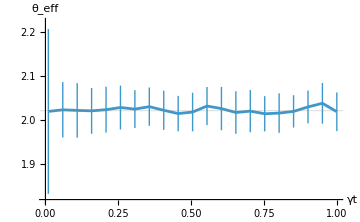
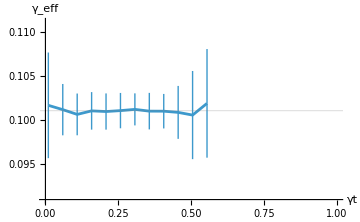

```mathematica
rω=1;

{rT,rTp}={1,100};
nγ=0.1;
nα=0.01;
nΛ=10^4;

tmin=0.01;
tmax=1;
tpoints=20;
tlist=Table[t,{t,tmin,tmax,(tmax-tmin)/tpoints}];

r𝒩=10^5;

nsamples=50;

times=Table[t,{t,tlist}];


MeanθeffvsγeffTable=ParallelTable[Mean[Table[First@FindEffectiveModelFromConditionalDist2[meas2PMConditional[t/nγ,rω,r𝒩],t/nγ,rω],{nsamples}]],{t,tlist}];
ErrorsθeffvsγeffTable=ParallelTable[Sqrt@Variance[Table[First@FindEffectiveModelFromConditionalDist2[meas2PMConditional[t/nγ,rω,r𝒩],t/nγ,rω],{nsamples}]],{t,tlist}];

MeanθeffWithErrorsTable=Transpose[{times,Around@@@Transpose[{MeanθeffvsγeffTable,ErrorsθeffvsγeffTable}]}];

MeanγeffTable=ParallelTable[Mean[Table[Last@FindEffectiveModelFromConditionalDist2[meas2PMConditional[t/nγ,rω,r𝒩],t/nγ,rω],{nsamples}]],{t,tlist}];

ErrorsγeffTable=ParallelTable[Sqrt@Variance[Table[Last@FindEffectiveModelFromConditionalDist2[meas2PMConditional[t/nγ,rω,r𝒩],t/nγ,rω],{nsamples}]],{t,tlist}];

MeanγeffWithErrorsTable=Transpose[{times,Around@@@Transpose[{MeanγeffTable,ErrorsγeffTable}]}];

{ListLinePlot[MeanθeffWithErrorsTable,AxesLabel->{"γt","θ_eff"},ImageSize->Medium,GridLines->{{},{{Teff[rω,rT,rTp,nα],Thick}}},PlotRange->{{0,tmax},{0.9Teff[rω,rT,rTp,nα],1.1*Teff[rω,rT,rTp,nα]}}],ListLinePlot[MeanγeffWithErrorsTable,ImageSize->Medium,AxesLabel->{"γt","γ_eff"},GridLines->{{},{{nγ(1+nα),Thick}}},PlotRange->{{0,tmax},{0.9nγ(1+nα),1.1*nγ(1+nα)}}]}
```

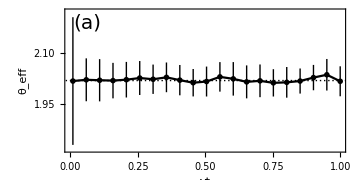
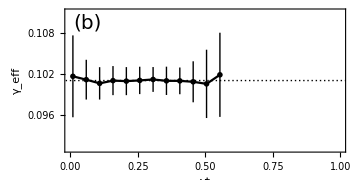

```mathematica
{ListLinePlot[MeanθeffWithErrorsTable,Frame->True,FrameLabel->{"γt","θ_eff"},LabelStyle->Directive["Helvetica", 14],ImageSize->Medium,GridLines->{{},{{Teff[rω,rT,rTp,nα],Thick}}},PlotRange->{{0,tmax},{0.9Teff[rω,rT,rTp,nα],1.1*Teff[rω,rT,rTp,nα]}},PlotTheme->"Monochrome",Epilog->Text[Style["(a)",Black,"Helvetica",20,Background->White],Scaled[{0.08,0.9}]],AspectRatio->0.5],ListLinePlot[MeanγeffWithErrorsTable,ImageSize->Medium,Frame->True,LabelStyle->Directive["Helvetica", 14],FrameLabel->{"γt","γ_eff"},GridLines->{{},{{nγ(1+nα),Thick}}},PlotRange->{{0,tmax},{0.9nγ(1+nα),1.1*nγ(1+nα)}},PlotTheme->"Monochrome",Epilog->Text[Style["(b)",Black,"Helvetica",20,Background->White],Scaled[{0.08,0.9}]],AspectRatio->0.5]}
```

```mathematica
r𝒩=10^12;

nsamples=50;

times=Table[t,{t,tlist}];


MeanθeffvsγeffTable=ParallelTable[Mean[Table[First@FindEffectiveModelFromConditionalDist2[meas2PMConditional[t/nγ,rω,r𝒩],t/nγ,rω],{nsamples}]],{t,tlist}];
ErrorsθeffvsγeffTable=ParallelTable[Sqrt@Variance[Table[First@FindEffectiveModelFromConditionalDist2[meas2PMConditional[t/nγ,rω,r𝒩],t/nγ,rω],{nsamples}]],{t,tlist}];

MeanθeffWithErrorsTable=Transpose[{times,Around@@@Transpose[{MeanθeffvsγeffTable,ErrorsθeffvsγeffTable}]}];

MeanγeffTable=ParallelTable[Mean[Table[Last@FindEffectiveModelFromConditionalDist2[meas2PMConditional[t/nγ,rω,r𝒩],t/nγ,rω],{nsamples}]],{t,tlist}];

ErrorsγeffTable=ParallelTable[Sqrt@Variance[Table[Last@FindEffectiveModelFromConditionalDist2[meas2PMConditional[t/nγ,rω,r𝒩],t/nγ,rω],{nsamples}]],{t,tlist}];

MeanγeffWithErrorsTable=Transpose[{times,Around@@@Transpose[{MeanγeffTable,ErrorsγeffTable}]}];
```

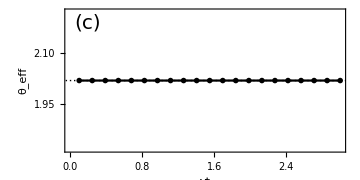
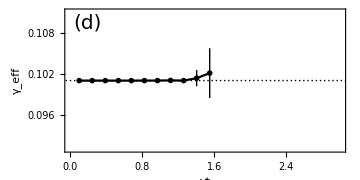

```mathematica
{ListLinePlot[MeanθeffWithErrorsTable,Frame->True,FrameLabel->{"γt","θ_eff"},LabelStyle->Directive["Helvetica", 14],ImageSize->Medium,GridLines->{{},{{Teff[rω,rT,rTp,nα],Thick}}},PlotRange->{{0,tmax},{0.9Teff[rω,rT,rTp,nα],1.1*Teff[rω,rT,rTp,nα]}},PlotTheme->"Monochrome",Epilog->Text[Style["(c)",Black,"Helvetica",20,Background->White],Scaled[{0.08,0.9}]],AspectRatio->0.5],ListLinePlot[MeanγeffWithErrorsTable,ImageSize->Medium,Frame->True,LabelStyle->Directive["Helvetica", 14],FrameLabel->{"γt","γ_eff"},GridLines->{{},{{nγ(1+nα),Thick}}},PlotRange->{{0,tmax},{0.9nγ(1+nα),1.1*nγ(1+nα)}},PlotTheme->"Monochrome",Epilog->Text[Style["(d)",Black,"Helvetica",20,Background->White],Scaled[{0.08,0.9}]],AspectRatio->0.5]}
```

#### Inverse problem: Trying to find 2 bath dissipator from (2 and 3 bath) dynamics

One bath (splitting doesn’t converge)

```mathematica
rT=1;

nΛ=10^4;

nα=0;
nγ=0.1;

rt=0.1;

rω1=RandomReal[{rT}]

ConditionalDistData1=PConditional2PMExact[rt,rω1,rT,rTp,nα,nγ,nΛ];

{θeff1,γeff1}=FindEffectiveModelFromConditionalDist[ConditionalDistData1,rt,rω1,nΛ]
(*teff1=Teff[rω1,rT,rTp,nα]*)

rω2=RandomReal[{rT}]

ConditionalDistData2=PConditional2PMExact[rt,rω2,rT,rTp,nα,nγ,nΛ];

{θeff2,γeff2}=FindEffectiveModelFromConditionalDist[ConditionalDistData2,rt,rω2,nΛ]
(*teff2=Teff[rω2,rT,rTp,nα]*)

rω3=RandomReal[{rT}]

ConditionalDistData3=PConditional2PMExact[rt,rω3,rT,rTp,nα,nγ,nΛ];

{θeff3,γeff3}=FindEffectiveModelFromConditionalDist[ConditionalDistData3,rt,rω3,nΛ]
(*teff3=Teff[rω3,rT,rTp,nα]*)
```

0.404905

{1.,0.1}

0.168345

{1.,0.1}

0.26577

{1.,0.1}

```mathematica
FindRoot[{γeff1==γ(1+α)&&θeff1==Teff[rω1,T,Tp,α]&&θeff2==Teff[rω2,T,Tp,α]&&θeff3==Teff[rω3,T,Tp,α]},{{γ,0.15},{α,0.1},{T,1.5},{Tp,200}},MaxIterations->1000,WorkingPrecision->MachinePrecision]//Chop
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{γ→0.0537614,α→0.737897,T→2.68409,Tp→-2.49831}

Two baths

```mathematica
{rT,rTp}={1,100};

nΛ=10^4;

nα=0.01;
nγ=0.1;

rt=0.1;

rω1=RandomReal[{rT}]

ConditionalDistData1=PConditional2PMExact[rt,rω1,rT,rTp,nα,nγ,nΛ];

{θeff1,γeff1}=FindEffectiveModelFromConditionalDist[ConditionalDistData1,rt,rω1,nΛ]
(*teff1=Teff[rω1,rT,rTp,nα]*)

rω2=RandomReal[{rTp}]

ConditionalDistData2=PConditional2PMExact[rt,rω2,rT,rTp,nα,nγ,nΛ];

{θeff2,γeff2}=FindEffectiveModelFromConditionalDist[ConditionalDistData2,rt,rω2,nΛ]
(*teff2=Teff[rω2,rT,rTp,nα]*)

rω3=RandomReal[{rTp}]

ConditionalDistData3=PConditional2PMExact[rt,rω3,rT,rTp,nα,nγ,nΛ];

{θeff3,γeff3}=FindEffectiveModelFromConditionalDist[ConditionalDistData3,rt,rω3,nΛ]
(*teff3=Teff[rω3,rT,rTp,nα]*)
```

0.889568

{2.01198,0.101}

34.3176

{9.16114,0.101}

36.7028

{9.59799,0.101}

```mathematica
FindRoot[{γeff1==γ(1+α)&&θeff1==Teff[rω1,T,Tp,α]&&θeff2==Teff[rω2,T,Tp,α]&&θeff3==Teff[rω3,T,Tp,α]},{{γ,0.15},{α,0.1},{T,1.5},{Tp,200}},MaxIterations->1000,WorkingPrecision->MachinePrecision]//Chop
```

{γ→0.1,α→0.01,T→1.,Tp→100.}

```mathematica
r𝒩=10^8;

meas2PM[t_,ω_]:=1/r𝒩 nmeasurements2PM[r𝒩,Flatten[Pness2PMExact[t,ω,rT,rTp,nα,Re@init[[2,2]],Re@init[[1,1]],nγ]]]
```

```mathematica
FindEffectiveModelFromJointDist[meas2PM[rt,rϵ[[2]]-rϵ[[1]]],rt,rϵ[[2]]-rϵ[[1]],Re@init[[2,2]],Re@init[[1,1]]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{34.5102,0.0425302}

3 baths

```mathematica
Teff3Baths[ω_,T_,Tp_,Tp2_,α_,α2_,γ_:10^-3,Λ_:10^2,ℏ_:1,kb_:1]:=-ω (Log[(Γ[-ω,T,γ,Λ,ℏ,kb]+α Γ[-ω,Tp,γ,Λ,ℏ,kb]+α2 Γ[-ω,Tp2,γ,Λ,ℏ,kb])/(Γ[ω,T,γ,Λ,ℏ,kb]+α Γ[ω,Tp,γ,Λ,ℏ,kb]+α2 Γ[ω,Tp2,γ,Λ,ℏ,kb])])^-1
```

```mathematica
p1Qubit3Baths[t_,ω_,T_,Tp_,α_,α2_,Tp2_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=Module[
{Γm=Γ[ω,T,γ,Λ]+α*Γ[ω,Tp,γ,Λ]+α2*Γ[ω,Tp2,γ,Λ],Γp=Γ[-ω,T,γ,Λ]+α*Γ[-ω,Tp,γ,Λ]+α2*Γ[-ω,Tp2,γ,Λ]},
-(-p1init Γm-p2init Γm+ⅇ^(t (-Γm-Γp)) p2init Γm-ⅇ^(t (-Γm-Γp)) p1init Γp)/(Γm+Γp)]
p2Qubit3Baths[t_,ω_,T_,Tp_,α_,α2_,Tp2_,p1init_,p2init_,γ_:10^-3,Λ_:10^2]:=Module[
{Γm=Γ[ω,T,γ,Λ]+α*Γ[ω,Tp,γ,Λ]+α2*Γ[ω,Tp2,γ,Λ],Γp=Γ[-ω,T,γ,Λ]+α*Γ[-ω,Tp,γ,Λ]+α2*Γ[-ω,Tp2,γ,Λ]},
(ⅇ^(t (-Γm-Γp)) p2init Γm+p1init Γp-ⅇ^(t (-Γm-Γp)) p1init Γp+p2init Γp)/(Γm+Γp)]
```

```mathematica
PConditional2PMExact3Baths[t_,ω_,T_,Tp_,α_,α2_,Tp2_,γ_,Λ_:10^2]:={{p2Qubit3Baths[t,ω,T,Tp,α,α2,Tp2,0,1,γ,Λ],p1Qubit3Baths[t,ω,T,Tp,α,α2,Tp2,0,1,γ,Λ]},{p2Qubit3Baths[t,ω,T,Tp,α,α2,Tp2,1,0,γ,Λ],p1Qubit3Baths[t,ω,T,Tp,α,α2,Tp2,1,0,γ,Λ]}}
```

```mathematica
{rT,rTp,rTp2}={1,100,200};
(*init=steadystate2[rϵ[[2]]-rϵ[[1]],rTp,rTp,0,10^-3,10^2];*)
(*init=randomPureDensityMatrix[2];*)

nα=0.1;
nα2=0.5;
nγ=0.1;
nΛ=10^4;

rt=0.1;

(*teff=Teff[rϵ[[2]]-rϵ[[1]],rT,rTp,nα]*)
```

```mathematica
nγ(1+nα+nα2)
```

0.106

```mathematica
rω1=RandomReal[{rT}];
rω1=5;

ConditionalDistData3Baths1=PConditional2PMExact3Baths[rt,rω1,rT,rTp,nα,nα2,rTp2,nγ,nΛ];

{θeff1,γeff1}=FindEffectiveModelFromConditionalDist[ConditionalDistData3Baths1,rt,rω1,nΛ]
θeff1=Teff3Baths[rω1,rT,rTp,rTp2,nα,nα2]


rω2=RandomReal[{rTp}];
rω2=10;

ConditionalDistData3Baths2=PConditional2PMExact3Baths[rt,rω2,rT,rTp,nα,nα2,rTp2,nγ,nΛ];

(*{θeff2,γeff2}=FindEffectiveModelFromConditionalDist[ConditionalDistData3Baths2,rt,rω2,nΛ]*)
θeff2=Teff3Baths[rω2,rT,rTp,rTp2,nα,nα2]

rω3=RandomReal[{rTp2}];
rω3=20;

ConditionalDistData3Baths3=PConditional2PMExact3Baths[rt,rω3,rT,rTp,nα,nα2,rTp2,nγ,nΛ];

(*{θeff3,γeff3}=FindEffectiveModelFromConditionalDist[ConditionalDistData3Baths3,rt,rω3,nΛ]*)
θeff3=Teff3Baths[rω3,rT,rTp,rTp2,nα,nα2]
```

{70.3086,0.16}

70.3086

71.7774

74.6268

```mathematica
FindRoot[{γeff1==γ(1+α)&&θeff1==Teff[rω1,T1,T2,α]&&θeff2==Teff[rω2,T1,T2,α]&&θeff3==Teff[rω3,T1,T2,α]},{{γ,0.15},{α,0.1},{T1,2},{T2,200}},MaxIterations->1000,WorkingPrecision->MachinePrecision]//Chop
```

{γ→0.100012,α→0.0598721,T1→1.00089,T2→183.696}

```mathematica
FindRoot[{θeff1==Teff[rω1,T1,T2,α]&&θeff2==Teff[rω2,T1,T2,α]&&θeff3==Teff[rω3,T1,T2,α]},{{α,0.1},{T1,2},{T2,200}},MaxIterations->1000,WorkingPrecision->MachinePrecision]//Chop
```

{α→0.598071,T1→1.00876,T2→183.696}

```mathematica
(nα*rTp+nα2*rTp2)/(nα+nα2)//N

nα+nα2
```

183.333

0.06

```mathematica
coldToHotRatio3Baths[ω_,T_,Tp_,Tp2_,α_,α2_]:=nBose[ω,T]/(α*nBose[ω,Tp]+α2*nBose[ω,Tp2])

ExpTeffSensitivity[ω_,T_,Tp_,Tp2_,α_,α2_]:=(ⅇ^(ω/T) (-1+ⅇ^(ω/Tp))^2 (-1+ⅇ^(ω/Tp2))^2 (1+α+α2) ω)/(T^2 (ⅇ^(ω/T)+ⅇ^(ω/Tp) α-ⅇ^((1/T+1/Tp) ω) (1+α)+ⅇ^(ω/Tp2) α2-ⅇ^((1/T+1/Tp2) ω) (1+α2)-ⅇ^((1/Tp+1/Tp2) ω) (α+α2)+ⅇ^((1/T+1/Tp+1/Tp2) ω) (1+α+α2))^2)
```

```mathematica
coldToHotRatio3Baths[rω1,rT,rTp,rTp2,nα,nα2]*100
ExpTeffSensitivity[rω1,rT,rTp,rTp2,nα,nα2]*100
```

0.559412

0.000546205

```mathematica
Series[Teff3Baths[ω,T,Tp,Tp2,α,α2],{Tp,Infinity,0},{Tp2,Infinity,0}]//FullSimplify
```

(α Tp)/(1+α+α2)+((α2 Tp2)/(1+α+α2)+(ω Coth[ω/(2 T)])/(2 (1+α+α2))+O[1/Tp2]^1)+O[1/Tp]^1

```mathematica
Normal@Series[Teff3Baths[ω,T,Tp,Tp2,α,α2],{Tp,Infinity,0},{Tp2,Infinity,0}]//FullSimplify
```

(2 Tp α+2 Tp2 α2+ω Coth[ω/(2 T)])/(2 (1+α+α2))

```mathematica
D[(2 Tp α+2 Tp2 α2+ω Coth[ω/(2 T)])/(2 (1+α+α2)),{T,2}]//FullSimplify
```

(ω^2 (-2 T+ω Coth[ω/(2 T)]) Csch[ω/(2 T)]^2)/(4 T^4 (1+α+α2))

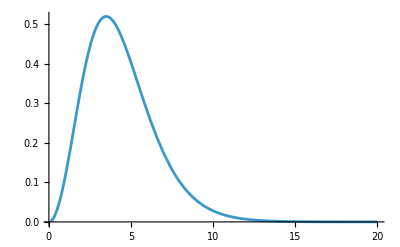

```mathematica
Plot[(ω^2 (-2 T+ω Coth[ω/(2 T)]) Csch[ω/(2 T)]^2)/(4 T^4 (1+α+α2))/.{T->1,α->0.1,α2->0.2},{ω,0.1,20}]
```

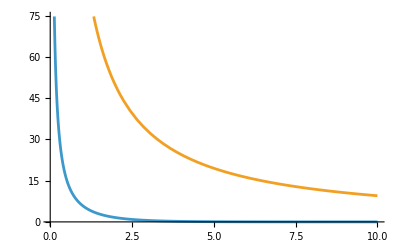
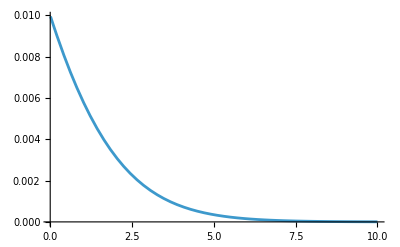

```mathematica
{Plot[{10*nBose[ω,1],nBose[ω,100]},{ω,0.01,10}],Plot[nBose[ω,1]/nBose[ω,100],{ω,0.01,10}]}
```

```mathematica
D[Exp[-ω/Teff3Baths[ω,T,Tp,Tp2,α,α2,γ,Λ]],T]//FullSimplify
```

(ⅇ^(ω/T) (-1+ⅇ^(ω/Tp))^2 (-1+ⅇ^(ω/Tp2))^2 (1+α+α2) ω)/(T^2 (ⅇ^(ω/T)+ⅇ^(ω/Tp) α-ⅇ^((1/T+1/Tp) ω) (1+α)+ⅇ^(ω/Tp2) α2-ⅇ^((1/T+1/Tp2) ω) (1+α2)-ⅇ^((1/Tp+1/Tp2) ω) (α+α2)+ⅇ^((1/T+1/Tp+1/Tp2) ω) (1+α+α2))^2)

```mathematica
Normal@Series[Teff3Baths[ω,T,Tp,Tp2,α,α2],{Tp,Infinity,0},{Tp2,Infinity,0},{T,Infinity,0}]//FullSimplify
```

(T+Tp α+Tp2 α2)/(1+α+α2)

```mathematica
Teff2BathLargeTp[ω_,T_,Tp_,α_]:=(α*Tp+ω/2*Coth[ω/(2*T)])/(1+α)
```

```mathematica
Teff3BathLargeTp[ω_,T_,Tp1_,Tp2_,α1_,α2_]:=(α1*Tp1+α2*Tp2+ω/2*Coth[ω/(2*T)])/(1+α1+α2)
```

```mathematica
Reduce[{Teff2BathLargeTp[ω1,T,Tp,α]==Teff3BathLargeTp[ω1,T1,Tp1,Tp2,α1,α2]&&Teff2BathLargeTp[ω2,T,Tp,α]==Teff3BathLargeTp[ω2,T1,Tp1,Tp2,α1,α2]&&Teff2BathLargeTp[ω3,T,Tp,α]==Teff3BathLargeTp[ω3,T1,Tp1,Tp2,α1,α2]},{α,T,Tp}]
```

$Aborted

```mathematica
FindTwoBathModelParametersFromJointDistData[t_,T_,Tp_,α_,p1init_,p2init_,𝒩_,γ_,Λ_:10^2]:=Module[{ϵ1,ϵ2,ϵ3,ω1,ω2,ω3,meas2PMω1,meas2PMω2,meas2PMω3,θeff1,θeff2,θeff3,γeff1,γeff2,γeff3},

ϵ1=RandomReal[{},2]//Sort;
ϵ2=RandomReal[{},2]//Sort;
ϵ3=RandomReal[{},2]//Sort;

ω1=ϵ1[[2]]-ϵ1[[1]];
ω2=ϵ2[[2]]-ϵ2[[1]];
ω3=ϵ3[[2]]-ϵ3[[1]];

(*ω1=RandomReal[];
ω2=RandomReal[];
ω3=RandomReal[];*)

ω1=RandomReal[];
ω2=RandomReal[T];
ω3=RandomReal[Tp];

meas2PMω1=1/𝒩 nmeasurements2PM[𝒩,Flatten[Pness2PMExact[t,ω1,T,Tp,α,Re@p1init,Re@p2init,γ,Λ]]];
meas2PMω2=1/𝒩 nmeasurements2PM[𝒩,Flatten[Pness2PMExact[t,ω2,T,Tp,α,Re@p1init,Re@p2init,γ,Λ]]];
meas2PMω3=1/𝒩 nmeasurements2PM[𝒩,Flatten[Pness2PMExact[t,ω3,T,Tp,α,Re@p1init,Re@p2init,γ,Λ]]];

meas2PMω1=Pness2PMExact[t,ω1,T,Tp,α,Re@p1init,Re@p2init,γ,Λ];
meas2PMω2=Pness2PMExact[t,ω2,T,Tp,α,Re@p1init,Re@p2init,γ,Λ];
meas2PMω3=Pness2PMExact[t,ω3,T,Tp,α,Re@p1init,Re@p2init,γ,Λ];


{θeff1,γeff1}=FindEffectiveModelFromJointDist[meas2PMω1,t,ω1,Re@p1init,Re@p2init];
{θeff2,γeff2}=FindEffectiveModelFromJointDist[meas2PMω2,t,ω1,Re@p1init,Re@p2init];
{θeff3,γeff3}=FindEffectiveModelFromJointDist[meas2PMω3,t,ω1,Re@p1init,Re@p2init];

FindRoot[{γeff1==γg(1+αg)&&θeff1==Teff[ω1,Tg,Tpg,αg]&&θeff2==Teff[ω2,Tg,Tpg,αg]&&θeff3==Teff[ω3,Tg,Tpg,αg]},{{γg,0.5γ},{αg,1.1α},{Tg,1.1T},{Tpg,1.1Tp}},AccuracyGoal->5,WorkingPrecision->MachinePrecision,MaxIterations->10000]

(*NSolve[{γeff1==γg(1+αg)&&θeff1==Teff[ω1,Tg,Tpg,αg]&&θeff2==Teff[ω2,Tg,Tpg,αg]&&θeff3==Teff[ω3,Tg,Tpg,αg]},{γg,αg,Tg,Tpg},WorkingPrecision->MachinePrecision]*)

(*FindRoot[{γeff1==γg(1+αg)&&θeff1==Simplify[TeffLargeTp[ω1,Tg,Tpg,αg]]&&θeff2==Simplify[TeffLargeTp[ω2,Tg,Tpg,αg]]&&θeff3==Simplify[TeffLargeTp[ω3,Tg,Tpg,αg]]},{{γg,1.01γ},{αg,1.01α},{Tg,1.01T},{Tpg,1.01Tp}},AccuracyGoal->5,PrecisionGoal->10,WorkingPrecision->MachinePrecision]*)

]
```

### Quadratic optimisation

#### Test

```mathematica
(*Example data*)
{rT,rTp,rTp2}={1,10,100};


nα=0.5;
nα2=0;
nγ=0.1;
nΛ=10^4;

(*omegaList={0.5,1.,3.,10.,20.0,50.0,100.0,200.0};*)

ωmin=5;ωmax=20.;ωpoints=5;
omegaList=Exp[Range[Log[ωmin],Log[ωmax],(Log[ωmax]-Log[ωmin])/(ωpoints-1)]];

(*omegaList={0.1,0.5,0.8,1.2,1.5};*)


TeffList=Teff3Baths[#,rT,rTp,rTp2,nα,nα2,nγ,nΛ]&/@omegaList;
yList=Exp[-omegaList/TeffList];
nEffObs=yList/(1-yList);  (*observed effective occupation*)
```

```mathematica
RandomVariate[NormalDistribution[]]
```

0.332516

```mathematica
(* ==============================================NNLS with QuadraticOptimization (explicit vars)==============================================*)

(*Temperature grid*)
Tmin=0.1;Tmax=20.;nT=100;
Tgrid=Exp[Range[Log[Tmin],Log[Tmax],(Log[Tmax]-Log[Tmin])/(nT-1)]];

(*AppendTo[Tgrid,rT];
AppendTo[Tgrid,rTp];

nT=102;*)

A=Table[nBose[ω,T],{ω,omegaList},{T,Tgrid}];


λ=1*10^-3;
λ=0;

(*Declare symbolic variables*)
wvars=Array[w,nT];

(*Objective function*)
obj=1/2 Total[(A.wvars-nEffObs)^2]+λ Total[wvars];

(*Constraints:w_i>=0*)
constraints={Thread[wvars>=0],Total[wvars]==1};

(*Solve*)
sol=QuadraticOptimization[obj,constraints,wvars,Method->"COIN"];

(*Extract numeric vector*)
wSol=wvars/. sol;

(*sol=NMinimize[{obj,constraints},wvars];
wSol=wvars/. sol[[2]];*)
```

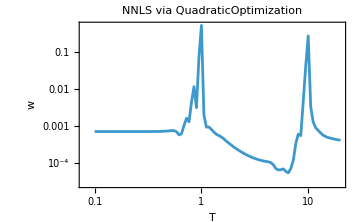
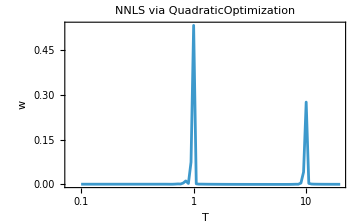

```mathematica
{ListLogLogPlot[Transpose[{Tgrid,wSol}],Joined->True,Frame->True,FrameLabel->{"T","w"},PlotLabel->"NNLS via QuadraticOptimization",ImageSize->Medium],ListLogLinearPlot[Transpose[{Tgrid,wSol}],Joined->True,Frame->True,FrameLabel->{"T","w"},PlotLabel->"NNLS via QuadraticOptimization",PlotRange->All,ImageSize->Medium]}
```

```mathematica
(*Detect peaks*)
(*thresh=Max[10^-4,10^-1 Max[wSol]];*)
(*thresh=10^-3;
peakIdx=Flatten@Position[wSol,_?(#>thresh&)];
peakTemps=Tgrid[[peakIdx]];
peakWeights=wSol[[peakIdx]];*)

peakPos=FindPeaks[wSol][[All,1]];

peakTemps=Tgrid[[peakPos]];
peakWeights=wSol[[peakPos]];

thresh=1*10^-3;
peakPos2=peakPos[[Flatten@Position[peakWeights,_?(#>thresh&)]]];
peakTemps2=Tgrid[[peakPos2]];
peakWeights2=wSol[[peakPos2]];

TableForm[Transpose[{peakTemps2,peakWeights2}],TableHeadings->{None,{"T","Weight"}}]
```

T | Weight
0.998705 | 0.531827
9.97412 | 0.275257

```mathematica
peakWeights2[[2]]/peakWeights2[[1]]
peakWeights2[[3]]/peakWeights2[[1]]
```

0.517569

Part::partw: Part 3 of {0.531827,0.275257} does not exist.

1.88031 {0.531827,0.275257}⟦3⟧

```mathematica
peakWeights//Total
wSol//Total
```

0.808543

1.

```mathematica
lambdas=10^Range[-6,-1,0.5];
results=Table[sol=QuadraticOptimization[1/2 Total[(A.wvars-nEffObs)^2]+λ Total[wvars],Thread[wvars>=0],wvars];
wSol=wvars/. sol//N//Flatten;
{λ,Norm[A.wSol-nEffObs]^2,Length[FindPeaks[wSol]]},{λ,lambdas}];
```

General::munfl: 9.28072×10^-9 3.586810744146×10^-321 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.89164×10^-26 6.15818162584×10^-640 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.198259 1.27304872531×10^-690 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

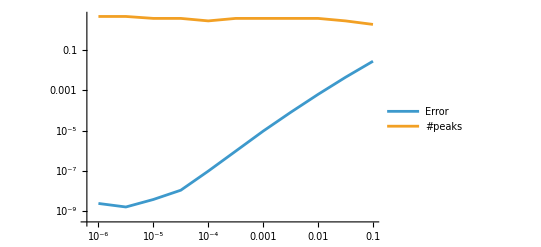

```mathematica
ListLogLogPlot[{Transpose[{results[[All,1]],results[[All,2]]}],Transpose[{results[[All,1]],results[[All,3]]}]},Joined->True,PlotLegends->{"Error","#peaks"}]
```

#### Choose ω which minimise condition number

```mathematica
vVec[ω_]:=Table[nBose[ω,Tgrid[[j]]],{j,1,Length[Tgrid]}];

(*build normalized design from a list of omegas*)
BuildNnorm[omegas_List]:=Module[{N,Nnorm},N=Table[vVec[ω],{ω,omegas}];(*rows:omegas x J*)(*normalize columns*)
N=Transpose[N];(*columns as rows temporarily*)
Nnorm=Map[#/Norm[#]&,N,{1}];
Transpose[Nnorm]  (*back to rows x J*)];

MinSingularValueForCandidate[omegas_List,omegaCand_]:=Module[{Ntest,sv},Ntest=BuildNnorm[Append[omegas,omegaCand]];
sv=SingularValueList[Ntest];
(*Min[sv]*)
First[sv]/Last[sv]];

MinSingularValueForCandidate[omegas_List,omegaCand_]:=Module[{Ntest,sv},Ntest=Table[vVec[ω],{ω,Append[omegas,omegaCand]}];
sv=SingularValueList[Ntest];
(*Min[sv]*)
First[sv]/Last[sv]];
```

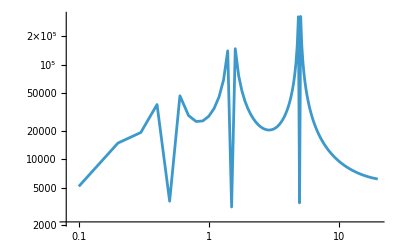

3687.39

```mathematica
(*greedy pick*)
selected={0.1,5,0.5,1.5};  (*current measured omegas*)
(*bestOmega=First@First@MaximalBy[Table[{ω,MinSingularValueForCandidate[selected,ω]},{ω,Range[0.1,50,0.1]}],Last]*)
ListLogLogPlot[Table[{ω,MinSingularValueForCandidate[selected,ω]},{ω,Range[0.1,20,0.1]}],PlotRange->All,Joined->True]

With[{sv=SingularValueList[Table[vVec[ω],{ω,selected}]]},First[sv]/Last[sv]]
```

{39.5058,0.518354,7.52905,2.2512}

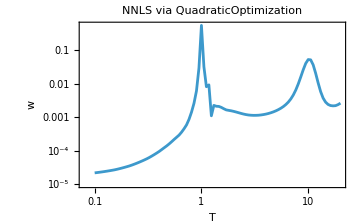
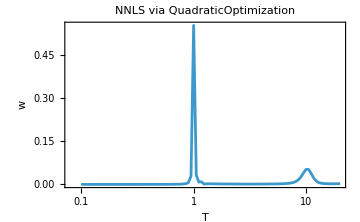

```mathematica
{rT,rTp}={1,10};

TeffList=Teff3Baths[#,rT,rTp,rTp2,nα,nα2,nγ,nΛ]&/@selected;
yList=Exp[-selected/TeffList];
nEffObs=yList/(1-yList)

A=Table[nBose[ω,T],{ω,selected},{T,Tgrid}];

(*Declare symbolic variables*)
wvars=Array[w,nT];

(*Objective function*)
obj=1/2 Total[(A.wvars-nEffObs)^2];

(*Constraints:w_i>=0*)
constraints={Thread[wvars>=0],Total[wvars]==1};

(*Solve*)
sol=QuadraticOptimization[obj,constraints,wvars,Method->"COIN"];

(*Extract numeric vector*)
wSol=wvars/. sol;

{ListLogLogPlot[Transpose[{Tgrid,wSol}],Joined->True,Frame->True,FrameLabel->{"T","w"},PlotLabel->"NNLS via QuadraticOptimization",ImageSize->Medium],ListLogLinearPlot[Transpose[{Tgrid,wSol}],Joined->True,Frame->True,FrameLabel->{"T","w"},PlotLabel->"NNLS via QuadraticOptimization",PlotRange->All,ImageSize->Medium]}
```

```mathematica
A//Dimensions
```

{4,100}

```mathematica
MatrixRank[A]
```

4

```mathematica
obj/.sol
```

1.36963×10^-9

```mathematica
(First@SingularValueList[A])/(Last@SingularValueList[A])
```

3687.39

#### Now try for different spectral densities

```mathematica
?Teff3Baths
```

```mathematica
Teff3BathsDifferentΛ[ω_,T_,Tp_,Tp2_,α_,α2_,γ_,Λ1_,Λ2_,Λ3_,ℏ_:1,kb_:1]:=-ω/Log[(Γ[-ω,T,γ,Λ1,ℏ,kb]+α Γ[-ω,Tp,γ,Λ2,ℏ,kb]+α2 Γ[-ω,Tp2,γ,Λ3,ℏ,kb])/(Γ[ω,T,γ,Λ1,ℏ,kb]+α Γ[ω,Tp,γ,Λ2,ℏ,kb]+α2 Γ[ω,Tp2,γ,Λ3,ℏ,kb])]
```

```mathematica
(*Example data*)
{rT,rTp,rTp2}={1,2,100};


nα=0.5;
nα2=0.1;
nγ=0.1;
nΛ1=10^3;
nΛ2=10^3;
nΛ3=10^5;

(*omegaList={0.5,1.,3.,10.,20.0,50.0,100.0,200.0};*)

ωmin=0.1;ωmax=20.;ωpoints=10;
omegaList=Exp[Range[Log[ωmin],Log[ωmax],(Log[ωmax]-Log[ωmin])/(ωpoints-1)]];


TeffList=Teff3BathsDifferentΛ[#,rT,rTp,rTp2,nα,nα2,nγ,nΛ1,nΛ2,nΛ3]&/@omegaList;
yList=Exp[-omegaList/TeffList];
nEffObs=yList/(1-yList);  (*observed effective occupation*)
```

```mathematica
(* ==============================================NNLS with QuadraticOptimization (explicit vars)==============================================*)

(*Temperature grid*)
Tmin=0.1;Tmax=100.;nT=100;
Tgrid=Exp[Range[Log[Tmin],Log[Tmax],(Log[Tmax]-Log[Tmin])/(nT-1)]];

A=Table[nBose[ω,T],{ω,omegaList},{T,Tgrid}];


λ=1*10^-12;
λ=0;

(*Declare symbolic variables*)
wvars=Array[w,nT];

(*Objective function*)
obj=1/2 Total[(A.wvars-nEffObs)^2]+λ Total[wvars];

(*Constraints:w_i>=0*)
constraints={Thread[wvars>=0],Total[wvars]==1};

(*Solve*)
sol=QuadraticOptimization[obj,constraints,wvars,PerformanceGoal->"Quality"];

(*Extract numeric vector*)
wSol=wvars/. sol/. x_/;NumericQ[x]:>Max[0.,x];
```

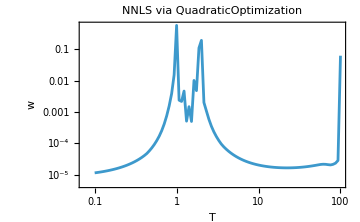
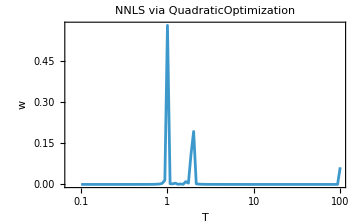

```mathematica
{ListLogLogPlot[Transpose[{Tgrid,wSol}],Joined->True,Frame->True,FrameLabel->{"T","w"},PlotLabel->"NNLS via QuadraticOptimization",ImageSize->Medium],ListLogLinearPlot[Transpose[{Tgrid,wSol}],Joined->True,Frame->True,FrameLabel->{"T","w"},PlotLabel->"NNLS via QuadraticOptimization",PlotRange->All,ImageSize->Medium]}
```

```mathematica
(*Detect peaks*)
(*thresh=Max[10^-4,10^-1 Max[wSol]];*)
(*thresh=10^-3;
peakIdx=Flatten@Position[wSol,_?(#>thresh&)];
peakTemps=Tgrid[[peakIdx]];
peakWeights=wSol[[peakIdx]];*)

peakPos=FindPeaks[wSol][[All,1]];

peakTemps=Tgrid[[peakPos]];
peakWeights=wSol[[peakPos]];

thresh=1*10^-1;
peakPos2=peakPos[[Flatten@Position[peakWeights,_?(#>thresh&)]]];
peakTemps2=Tgrid[[peakPos2]];
peakWeights2=wSol[[peakPos2]];

TableForm[Transpose[{peakTemps2,peakWeights2}],TableHeadings->{None,{"T","Weight"}}]
```

T | Weight
1. | 0.579279
2.00923 | 0.192838

```mathematica
peakWeights2[[2]]/peakWeights2[[1]]
```

0.332893

```mathematica
(*Example data*)
{rT,rTp,rTp2}={1,10,100};

ωmin=0.1;ωmax=20.;ωpoints=20;
omegaList=Exp[Range[Log[ωmin],Log[ωmax],(Log[ωmax]-Log[ωmin])/(ωpoints-1)]];


TeffList=Teff3BathsDifferentΛ[#,rT,rTp,rTp2,nα,nα2,nγ,nΛ1,nΛ2,nΛ3]&/@omegaList;
yList=Exp[-omegaList/TeffList];
nEffObs=yList/(1-yList);  

(*Temperature grid*)
Tmin=0.1;Tmax=100.;nT=20;
Tgrid=Exp[Range[Log[Tmin],Log[Tmax],(Log[Tmax]-Log[Tmin])/(nT-1)]];

A=Table[nBose[ω,T],{ω,omegaList},{T,Tgrid}];
```

```mathematica
(*Flatten variables*)wvars=Array[w,nT*Length[omegaList]];
(*helper to index w_jk at position (j,k):position=(k-1)*J+j*)
wIndex[j_,k_]:=(k-1)*nT+j;

(*Data term:sum_k (A_k.w^{(k)}-n_k)^2*)
dataTerm=Sum[(Sum[A[[k,j]]*wvars[[wIndex[j,k]]],{j,1,nT}]-nEffObs[[k]])^2,{k,1,Length[omegaList]}];

(*Smoothness term:sum_j sum_{k=1}^{K-1} (a_{j,k+1}-a_{j,k})^2*)
lambdaS=1.*10^-1;
lambdaS=0;

smoothTerm=lambdaS*Sum[(wvars[[wIndex[j,k+1]]]-wvars[[wIndex[j,k]]])^2,{j,1,nT},{k,1,Length[omegaList]-1}];

λL21=10;

l21Term=λL21*Sum[Sqrt[Total[Table[(wvars[[wIndex[j,k]]])^2,{k,1,Length[omegaList]}]]],{j,1,nT}];

objective=dataTerm+smoothTerm+l21Term;

(*Constraints:nonnegativity and column simplex*)
ineq=Thread[wvars>=0];
eqs=Table[Sum[wvars[[wIndex[j,k]]],{j,1,nT}]==1,{k,1,Length[omegaList]}];

(*sol=QuadraticOptimization[objective,Join[ineq,eqs],wvars];
wSol=N[wvars/. sol];*)

sol=NMinimize[{objective,Join[ineq,eqs]},wvars,Method->"IPOPT"];
wSol=wvars/.sol[[2]];
```

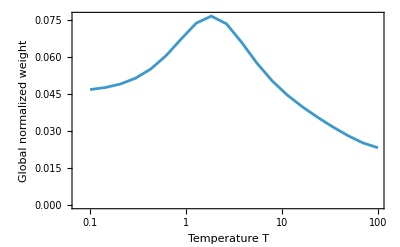

```mathematica
(*reshape*)Wcols=Partition[wSol,nT];  (*{K,nT}*)
W=Transpose[Wcols];          (*{nT,K}*)

(*derive per-T summaries*)
(*wmeanperT=Total[W,{2}]/Length[omegaList];*)
wsumperT=Total[W,{2}];
wglobal=wsumperT/Total[wsumperT];

wmaxperT=Max/@W; (*elementwise max across each row*)

(*plot*)
ListLinePlot[Transpose[{Tgrid,wmaxperT}],Joined->True,Frame->True,FrameLabel->{"Temperature T","Global normalized weight"},ScalingFunctions->{"Log",None},PlotRange->All]
```

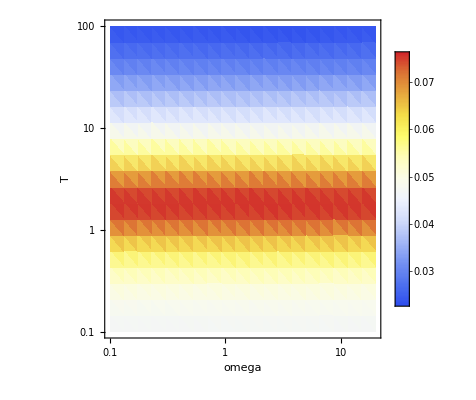

```mathematica
ListDensityPlot[Table[{omegaList[[k]],Tgrid[[j]],W[[j,k]]},{j,nT},{k,Length[omegaList]}]//Flatten[#,1]&,InterpolationOrder->2,PlotRange->All,FrameLabel->{"omega","T","W"},ColorFunction->"TemperatureMap",ScalingFunctions->{"Log","Log"},PlotLegends->Automatic]
```

```mathematica
(*Parametric Lorentzian spectral density*)
JLorentzian[ω_,γ_,ω0_,λ_]:=(γ*λ^2*ω)/((ω^2-ω0^2)^2+λ^2*ω^2)
```

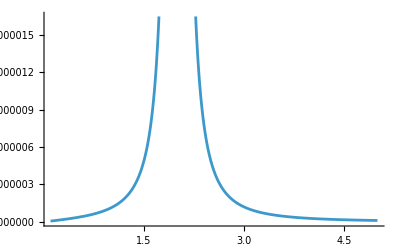

```mathematica
Plot[JLorentzian[ω,0.1,2,0.01],{ω,0.1,5}]
```

```mathematica
ΓLorentzian[ω_,T_,γ_,ω0_,λ_,ℏ_:1,kb_:1]:=2JLorentzian[ω,γ,ω0,λ](1+1/(ⅇ^((ℏ ω)/(kb T))-1));
```

```mathematica
Teff3BathsLorentzian[ω_,T_,Tp_,Tp2_,α_,α2_,γ_,ω01_,ω02_,ω03_,λ1_,λ2_,λ3_,ℏ_:1,kb_:1]:=-ω/Log[(ΓLorentzian[-ω,T,γ,ω01,λ1,ℏ,kb]+α ΓLorentzian[-ω,Tp,γ,ω02,λ2,ℏ,kb]+α2 ΓLorentzian[-ω,Tp2,γ,ω03,λ3,ℏ,kb])/(ΓLorentzian[ω,T,γ,ω01,λ1,ℏ,kb]+α ΓLorentzian[ω,Tp,γ,ω02,λ2,ℏ,kb]+α2 ΓLorentzian[ω,Tp2,γ,ω03,λ3,ℏ,kb])]
```

```mathematica
(*Example data*)
{rT,rTp,rTp2}={1,10,100};


nα=0.5;
nα2=0.1;
nγ=0.1;
nω01=1;
nω02=10;
nω03=100;
nλ1=0.01;
nλ2=0.01;
nλ3=0.01;


ωmin=0.1;ωmax=20.;ωpoints=10;
omegaList=Exp[Range[Log[ωmin],Log[ωmax],(Log[ωmax]-Log[ωmin])/(ωpoints-1)]];


TeffList=Teff3BathsLorentzian[#,rT,rTp,rTp2,nα,nα2,nγ,nω01,nω02,nω03,nλ1,nλ2,nλ3]&/@omegaList;
yList=Exp[-omegaList/TeffList];
nEffObs=yList/(1-yList);  (*observed effective occupation*)
```

```mathematica
(* ==============================================NNLS with QuadraticOptimization (explicit vars)==============================================*)

(*Temperature grid*)
Tmin=0.1;Tmax=100.;nT=100;
Tgrid=Exp[Range[Log[Tmin],Log[Tmax],(Log[Tmax]-Log[Tmin])/(nT-1)]];

A=Table[nBose[ω,T],{ω,omegaList},{T,Tgrid}];


λ=1*10^-6;
λ=0;

(*Declare symbolic variables*)
wvars=Array[w,nT];

(*Objective function*)
obj=1/2 Total[(A.wvars-nEffObs)^2]+λ Total[wvars];

(*Constraints:w_i>=0*)
constraints={Thread[wvars>=0],Total[wvars]==1};

(*Solve*)
sol=QuadraticOptimization[obj,constraints,wvars,PerformanceGoal->"Quality"];

(*Extract numeric vector*)
wSol=wvars/. sol/. x_/;NumericQ[x]:>Max[0.,x];
```

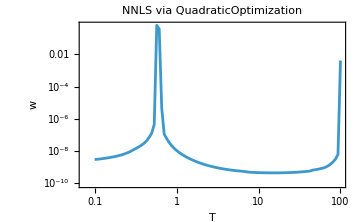
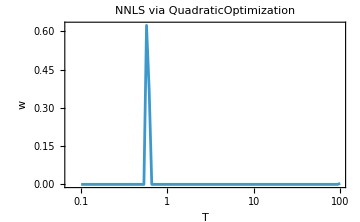

```mathematica
{ListLogLogPlot[Transpose[{Tgrid,wSol}],Joined->True,Frame->True,FrameLabel->{"T","w"},PlotLabel->"NNLS via QuadraticOptimization",ImageSize->Medium],ListLogLinearPlot[Transpose[{Tgrid,wSol}],Joined->True,Frame->True,FrameLabel->{"T","w"},PlotLabel->"NNLS via QuadraticOptimization",PlotRange->All,ImageSize->Medium]}
```

```mathematica
ωmin=0.1;ωmax=200.;ωpoints=200;
omegaList=Exp[Range[Log[ωmin],Log[ωmax],(Log[ωmax]-Log[ωmin])/(ωpoints-1)]];


TeffList=Teff3BathsLorentzian[#,rT,rTp,rTp2,nα,nα2,nγ,nω01,nω02,nω03,nλ1,nλ2,nλ3]&/@omegaList;
```

```mathematica
(*Observed spectrum:nEffObs,omegaList already defined*)(*Parameters:T1,T2,T3,alpha1,alpha2,gamma,Omega01,Omega02,Omega03,Lambda1,Lambda2,Lambda3*)paramsNames={T1,T2,T3,alpha1,alpha2,Omega01,Omega02,Omega03,Lambda1,Lambda2,Lambda3};

(*Model function wrapper*)
model[ω_,T1_,T2_,T3_,alpha1_,alpha2_,Omega01_,Omega02_,Omega03_,Lambda1_,Lambda2_,Lambda3_]:=Teff3BathsLorentzian[ω,T1,T2,T3,alpha1,alpha2,nγ,Omega01,Omega02,Omega03,Lambda1,Lambda2,Lambda3];
```

```mathematica
initGuess={10,15,150.0,0.4,0.14,10,10.2,101.0,0.02,0.04,0.015};

fit=FindFit[Transpose[{omegaList,TeffList}],Re@model[ω,T1,T2,T3,alpha1,alpha2,Omega01,Omega02,Omega03,Lambda1,Lambda2,Lambda3],Partition[Riffle[paramsNames,initGuess],2],ω,MaxIterations->1000]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{T1→0.999924,T2→10.0002,T3→100.,alpha1→0.559743,alpha2→0.264586,Omega01→1.0002,Omega02→9.99982,Omega03→100.,Lambda1→0.0366503,Lambda2→0.0346386,Lambda3→0.0225316}

### Bayesian estimation of couplings

#### Definitions and max likelihood

```mathematica
ClearAll[nEffObs,nEffModel,pObs,pModel]
(*-------------------------------------Setup-------------------------------------*)
Ttrue={1,10};
γtrue={0.5,0.1};

wtrue=γtrue/Total[γtrue];


omegaList={0.1,0.5,1.5,8,15};

(*Effective occupation model*)
nEffTrue[ω_]:=Sum[γtrue[[j]]* nBose[ω,Ttrue[[j]]],{j,Length[γtrue]}]/Total[γtrue];

(*Convert n_eff -> excitation probability*)
pExc[n_]:=n/(1+2n);

(*Effective occupation model*)
nEffModel[ω_,γ_List,T_List]:=Module[{num,den},num=Sum[γ[[j]] nBose[ω,T[[j]]],{j,Length[γ]}];
den=Total[γ];
num/den]

pModel=pExc[nEffModel[#,{γ1,γ2},{T1,T2}]&/@omegaList]

(*Effective occupation model with relative weights*)
nEffModelRelative[ω_,w_List,T_List]:=Sum[w[[j]] nBose[ω,T[[j]]],{j,Length[w]}]

pModelRelative=pExc[nEffModelRelative[#,{w1,w2},{T1,T2}]&/@omegaList];

(*Generate observed data (no noise for now)*)
nEffObs=nEffTrue[#]&/@omegaList;
pObs=pExc[nEffObs]
```

{(γ1/(-1+ⅇ^(0.1/T1))+γ2/(-1+ⅇ^(0.1/T2)))/((γ1+γ2) (1+(2 (γ1/(-1+ⅇ^(0.1/T1))+γ2/(-1+ⅇ^(0.1/T2))))/(γ1+γ2))),(γ1/(-1+ⅇ^(0.5/T1))+γ2/(-1+ⅇ^(0.5/T2)))/((γ1+γ2) (1+(2 (γ1/(-1+ⅇ^(0.5/T1))+γ2/(-1+ⅇ^(0.5/T2))))/(γ1+γ2))),(γ1/(-1+ⅇ^(1.5/T1))+γ2/(-1+ⅇ^(1.5/T2)))/((γ1+γ2) (1+(2 (γ1/(-1+ⅇ^(1.5/T1))+γ2/(-1+ⅇ^(1.5/T2))))/(γ1+γ2))),(γ1/(-1+ⅇ^(8/T1))+γ2/(-1+ⅇ^(8/T2)))/((γ1+γ2) (1+(2 (γ1/(-1+ⅇ^(8/T1))+γ2/(-1+ⅇ^(8/T2))))/(γ1+γ2))),(γ1/(-1+ⅇ^(15/T1))+γ2/(-1+ⅇ^(15/T2)))/((γ1+γ2) (1+(2 (γ1/(-1+ⅇ^(15/T1))+γ2/(-1+ⅇ^(15/T2))))/(γ1+γ2)))}

{0.490003,0.45035,0.358694,0.107088,0.0436872}

```mathematica
pModel/.{γ1->γtrue[[1]],γ2->γtrue[[2]],T1->Ttrue[[1]],T2->Ttrue[[2]]}

pModelRelative/.{w1->wtrue[[1]],w2->wtrue[[2]],T1->Ttrue[[1]],T2->Ttrue[[2]]}
```

{0.960795,0.81934,0.559318,0.119931,0.0456829}

{0.960795,0.81934,0.559318,0.119931,0.0456829}

```mathematica
Ncounts=1000000;

countsExc=RandomVariate[BinomialDistribution[Ncounts,#]]&/@pObs
```

{489726,450734,359050,106948,43817}

```mathematica
(*-------------------------------------Likelihood function-------------------------------------*)
loglikelihood[γ1_,γ2_,T1_,T2_]:=Module[{pModel=pExc[nEffModel[#,{γ1,γ2},{T1,T2}]&/@omegaList]},
countsExc.Log[pModel]+(Ncounts-countsExc).Log[1-pModel]]

loglikelihoodRelative[w1_,w2_,T1_,T2_]:=Module[{pModel=pExc[nEffModelRelative[#,{w1,w2},{T1,T2}]&/@omegaList]},
countsExc.Log[pModel]+(Ncounts-countsExc).Log[1-pModel]]
```

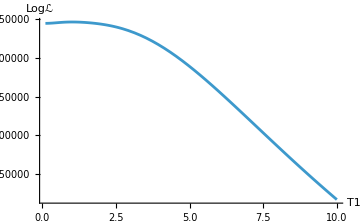
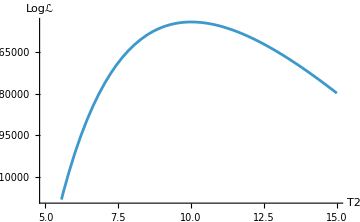

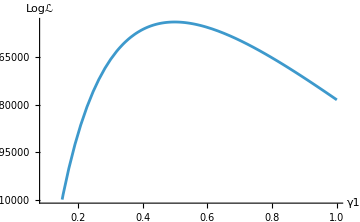
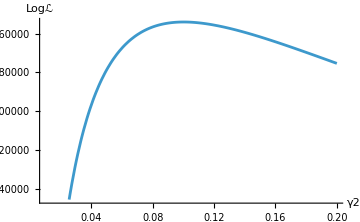

```mathematica
{Plot[loglikelihood[γtrue[[1]],γtrue[[2]],T,Ttrue[[2]]],{T,0.1,10},AxesLabel->{T1, Logℒ},ImageSize->Medium]
,Plot[loglikelihood[γtrue[[1]],γtrue[[2]],Ttrue[[1]],T],{T,5,15},AxesLabel->{T2, Logℒ},ImageSize->Medium]}

{Plot[loglikelihood[γ1,γtrue[[2]],Ttrue[[1]],Ttrue[[2]]],{γ1,0.1,1},AxesLabel->{γ1, Logℒ},ImageSize->Medium]
,Plot[loglikelihood[γtrue[[1]],γ2,Ttrue[[1]],Ttrue[[2]]],{γ2,0.01,0.2},AxesLabel->{γ2, Logℒ},ImageSize->Medium]}
```

```mathematica
Plot3D[loglikelihood[γtrue[[1]],γtrue[[2]],T1,T2],{T1,0.1,2},{T2,5,15},AxesLabel->{T1, T2, Logℒ}]
```

-Graphics3D-

```mathematica
omegaList={0.1,0.2,0.5,0.7,0.9,1.5,10,12};

pObs=pExc[nEffTrue[#]&/@omegaList];

pModel=pExc[nEffModel[#,{γ1,γ2},{T1,T2}]&/@omegaList];
pModelRelative=pExc[nEffModelRelative[#,{w1,w2},{T1,T2}]&/@omegaList];

Ncounts=1000000;

countsExc=RandomVariate[BinomialDistribution[Ncounts,#]]&/@pObs;
```

```mathematica
(*-------------------------------------Find max likelihood for different pairs of Subscript[γ, i],Subscript[T, i]-------------------------------------*)
Print["T_1=",Ttrue[[1]],", T_2=",Ttrue[[2]],", γ_1=",γtrue[[1]],", γ_2=",γtrue[[2]]]

FindMaximum[loglikelihood[γtrue[[1]],γtrue[[2]],T1,T2],{T1,0.1},{T2,5}]

FindMaximum[{loglikelihood[γ1,γ2,Ttrue[[1]],Ttrue[[2]]],1>γ1>0&&1>γ2>0},{γ1,0.4},{γ2,0.2}]

FindMaximum[{loglikelihood[γ1,γtrue[[2]],T1,Ttrue[[2]]],1>γ1>0&&T1>0},{{γ1,0.4},{T1,5}}]

FindMaximum[{loglikelihood[γtrue[[1]],γ2,Ttrue[[1]],T2],1>γ2>0&&T2>0},{{γ2,0.4},{T2,5}}]

FindMaximum[{loglikelihood[γ1,γ2,T1,T2],1>γ1>0&&1>γ2>0&&T1>0&&T2>0},{γ1,0.4},{γ2,0.2},{T1,5},{T2,5}]
```

T_1=1, T_2=10, γ_1=0.5, γ_2=0.1

{-4.60405×10^6,{T1→0.981231,T2→10.0168}}

{-4.60405×10^6,{γ1→0.653407,γ2→0.130633}}

{-4.60405×10^6,{γ1→0.498318,T1→0.979361}}

{-4.60405×10^6,{γ2→0.0968079,T2→10.1824}}

{-4.60405×10^6,{γ1→0.64856,γ2→0.133871,T1→0.964031,T2→9.85904}}

```mathematica
(*-------------------------------------Find max likelihood for different pairs of Subscript[γ, i],Subscript[T, i]-------------------------------------*)
Print["T_1=",Ttrue[[1]],", T_2=",Ttrue[[2]],", w_1=",wtrue[[1]],", γ_2=",wtrue[[2]]]

FindMaximum[loglikelihoodRelative[wtrue[[1]],wtrue[[2]],T1,T2],{T1,0.1},{T2,5}]

FindMaximum[{loglikelihoodRelative[w1,w2,Ttrue[[1]],Ttrue[[2]]],1>w1>0&&1>w2>0&&w1+w2==1},{w1,0.4},{w2,0.2}]

FindMaximum[{loglikelihoodRelative[w1,wtrue[[2]],T1,Ttrue[[2]]],1>w1>0&&T1>0},{{w1,0.4},{T1,5}}]

FindMaximum[{loglikelihoodRelative[wtrue[[1]],w2,Ttrue[[1]],T2],1>w2>0},{{w2,0.4},{T2,5}}]

FindMaximum[{loglikelihoodRelative[w1,w2,T1,T2],1>w1>0&&1>w2>0&&T1>0&&T2>0&&w1+w2==1},{w1,0.4},{w2,0.2},{T1,5},{T2,5}]
```

T_1=1, T_2=10, w_1=0.833333, γ_2=0.166667

{-2.55407×10^6,{T1→1.01045,T2→10.0015}}

{-2.55407×10^6,{w1→0.833143,w2→0.166857}}

{-2.55407×10^6,{w1→0.863513,T1→0.990965}}

{-2.55407×10^6,{w2→0.167099,T2→9.99051}}

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{-2.55544×10^6,{w1→0.692501,w2→0.307499,T1→0.0211332,T2→7.5337}}

Now calculate the posterior

```mathematica
?priorLogUniform
```

{4883,4593,3518,842,614}

-25512.9

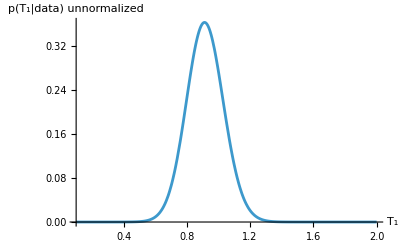

```mathematica
Ncounts=10000;

countsExc=RandomVariate[BinomialDistribution[Ncounts,#]]&/@pObs

peak=FindMaximum[loglikelihood[γtrue[[1]],γtrue[[2]],T1,Ttrue[[2]]],{T1,0.1,2}][[1]]

Plot[Exp[loglikelihood[γtrue[[1]],γtrue[[2]],T,Ttrue[[2]]]+Log[priorLogUniform[T,0.1,2]]-peak],{T,0.1,2},PlotRange->All,AxesLabel->{Subscript[T, 1],"p(T_1|data) unnormalized"}]
```

```mathematica
Exp[loglikelihood[γtrue[[1]],γtrue[[2]],T,Ttrue[[2]]]+Log[priorLogUniform[T,0.1,2]]-peak/.T->1]
```

0.273296

```mathematica
NIntegrate[Exp[loglikelihood[γtrue[[1]],γtrue[[2]],T,Ttrue[[2]]]+Log[priorLogUniform[T,0.1,2]]-peak],{T,0.1,2},AccuracyGoal->10]
```

0.

```mathematica
posteriorDiscrete1Temp[θmin_,θmax_,θpoints_:200]:=Module[{grid,logPostVals,shifted,unnormalizedPosterior},
grid=Subdivide[θmin,θmax,θpoints];
logPostVals=loglikelihood[γtrue[[1]],γtrue[[2]],#,Ttrue[[2]]]+Log[priorLogUniform[#,θmin,θmax]]&/@grid;
shifted=logPostVals-Max[logPostVals];
unnormalizedPosterior=Exp[shifted];

unnormalizedPosterior/Total[unnormalizedPosterior]

]
```

{4857,4516,3542,803,641}

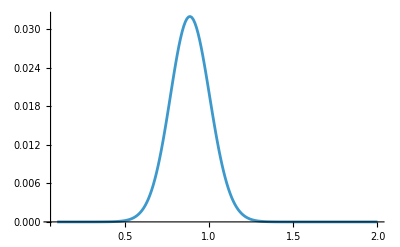

```mathematica
Ncounts=10000;

countsExc=RandomVariate[BinomialDistribution[Ncounts,#]]&/@pObs

θgrid=Subdivide[0.1,2,200];

ListLinePlot[Partition[Riffle[θgrid,posteriorDiscrete1Temp[0.1,2]],2],PlotRange->All]
```

```mathematica
Total[posteriorDiscrete1Temp[0.1,2]]
```

1.

```mathematica
μpost=Total[θgrid*posteriorDiscrete1Temp[0.1,2]]

σpost=Sqrt[Total[θgrid^2*posteriorDiscrete1Temp[0.1,2]]-μpost^2]
```

0.888743

0.119889

```mathematica
θgrid[[Position[posteriorDiscrete1Temp[0.1,2],Max[posteriorDiscrete1Temp[0.1,2]]][[1]]//First]] (*MAP estimate*)
```

0.8885

#### Multi-parameter posterior

For the multi-parameter posterior, we need to use either importance sampling or MCMC

```mathematica
(*Log-prior:example:uniform w1 on (0,1),log-uniform T in[Tmin,Tmax]*)
Tmin=0.05;Tmax=50.;
logPriorParams[w1_,T1_,T2_]:=Module[{},If[w1<=0||w1>=1,Return[-Infinity]];
If[T1<=Tmin||T1>=Tmax||T2<=Tmin||T2>=Tmax,Return[-Infinity]];
(-Log[T1]-Log[T2])   (*log-uniform on T1 and T2*)];
```

```mathematica
logPriorParams[w,2,3]
```

-Log[2]-Log[3]

```mathematica
omegaList={0.1,5,12};

pObs=pExc[nEffTrue[#]&/@omegaList];

pModelRelative=pExc[nEffModelRelative[#,{w1,w2},{T1,T2}]&/@omegaList];

Ncounts=1000000;

countsExc=RandomVariate[BinomialDistribution[Ncounts,#]]&/@pObs;
```

```mathematica
logposteriorRelative[w1_,T1_,T2_]:=loglikelihoodRelative[w1,1-w1,T1,T2]+logPriorParams[w1,T1,T2]
```

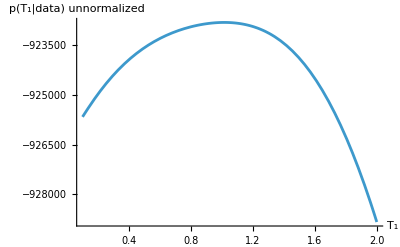

```mathematica
Plot[logposteriorRelative[wtrue[[1]],T,Ttrue[[2]]],{T,0.1,2},PlotRange->All,AxesLabel->{Subscript[T, 1],"p(T_1|data) unnormalized"}]
```

```mathematica
FindMaximum[{logposteriorRelative[w1,T1,T2],1>w1>0&&T1>0&&T2>0},{w1,0.4},{T1,5},{T2,5}]
```

{-922819.,{w1→0.169943,T1→9.88066,T2→0.995959}}

```mathematica
(*Find MAP in original param space*)
MAPestimates=FindMaximum[{logposteriorRelative[w1,T1,T2],1>w1>0&&T1>0&&T2>0},{w1,0.4},{T1,5},{T2,5}];
thetaMAP={w1,T1,T2}/. MAPestimates[[2]]
maxLogPost=MAPestimates[[1]]
```

{0.169943,9.88066,0.995959}

-922819.

```mathematica
NumericHessian[f_,x0_List,h_:1.*10^-5]:=Module[{n=Length[x0],H,e,xp,xm,xpp,xpm,xmp,xmm},H=ConstantArray[0.,{n,n}];
Do[If[i==j,(*diagonal*)xp=ReplacePart[x0,i->x0[[i]]+h];
xm=ReplacePart[x0,i->x0[[i]]-h];
H[[i,i]]=(f[xp]-2 f[x0]+f[xm])/h^2;,(*off-diagonal mixed partial*)xpp=ReplacePart[x0,{i->x0[[i]]+h,j->x0[[j]]+h}];
xpm=ReplacePart[x0,{i->x0[[i]]+h,j->x0[[j]]-h}];
xmp=ReplacePart[x0,{i->x0[[i]]-h,j->x0[[j]]+h}];
xmm=ReplacePart[x0,{i->x0[[i]]-h,j->x0[[j]]-h}];
H[[i,j]]=(f[xpp]-f[xpm]-f[xmp]+f[xmm])/(4 h^2);
H[[j,i]]=H[[i,j]];],{i,n},{j,i,n}];
H];
```

```mathematica
neglogposteriorRelative[{w1_,T1_,T2_}]:=-(loglikelihoodRelative[w1,1-w1,T1,T2]+logPriorParams[w1,T1,T2])
```

```mathematica
Hess=NumericHessian[neglogposteriorRelative,{w1,T1,T2}]/.Thread[MAPestimates[[2]]];
covProp=Inverse[Hess];
```

```mathematica
Hess//Eigenvalues
```

{8.09198×10^6,3530.68,54.6509}

```mathematica
(*3) Importance sampling from N(thetaMAP,c*covProp)*)
Hess=NumericHessian[neglogposteriorRelative,{w1,T1,T2}]/.Thread[MAPestimates[[2]]];
covProp=Inverse[Hess];

c=3;
proposal=MultinormalDistribution[thetaMAP,c covProp];
S=20000;
samples=RandomVariate[proposal,S];
```

```mathematica
logposteriorRelative2[{w1_,T1_,T2_}]:=loglikelihoodRelative[w1,1-w1,T1,T2]+logPriorParams[w1,T1,T2]
(*4) compute robust log-weights*)
logpostList=Table[logposteriorRelative2[samples[[i]]],{i,S}];
logqList=Table[Log[PDF[proposal,samples[[i]]]],{i,S}];
(*discard-Infinity logpost samples*)
validInd=Flatten@Position[logpostList,_?NumericQ];
samples=samples[[validInd]];
logpostList=logpostList[[validInd]];
logqList=logqList[[validInd]];
```

```mathematica
logw=logpostList-logqList;
Lmax=Max[logw];
wtilde=Exp[logw-Lmax];
w=wtilde/Total[wtilde];

(*Weighted marginal for w1,T1,T2:do weighted kernel density or histogram*)
(*Example:weighted mean and credible intervals*)
weightedMean=Total[(samples*w)];  (*vector of means*)
weightedMean
```

{0.169745,9.89035,0.997134}

```mathematica
w//Dimensions
```

{20000}

```mathematica
(*Work on unconstrained space:u=logit(w1),lT1=Log[T1],lT2=Log[T2]*)
Logit[x_]:=Log[x/(1-x)];
InvLogit[y_]:=1/(1+Exp[-y]);

logPosteriorTrans[uVec_]:=Module[{w1=InvLogit[uVec[[1]]],T1=Exp[uVec[[2]]],T2=Exp[uVec[[3]]]},logposteriorRelative2[{w1,T1,T2}]  (*your logPosterior in original space*)];

(*Simple adaptive MH*)
nIter=50000;burn=10000;
cur={Logit[0.7],Log[2],Log[5]};
curLP=logPosteriorTrans[cur];
samplesMH={};
accept=0;

Hess=NumericHessian[neglogposteriorRelative,{w1,T1,T2}]/.Thread[MAPestimates[[2]]];
covProp=3*Inverse[Hess];
Do[prop=cur+RandomVariate[MultinormalDistribution[{0,0,0},covProp]];
propLP=logPosteriorTrans[prop];
If[propLP>-Infinity&&Log[RandomReal[]]<propLP-curLP,cur=prop;curLP=propLP;accept++;];
If[i>burn,AppendTo[samplesMH,cur]];,{i,nIter}];

(*transform back*)

invTransform[{u_,v1_,v2_}]:={InvLogit[u],Exp[v1],Exp[v2]};
samplesPhys=invTransform/@samples;
w1samples=samplesPhys[[All,1]];
T1samples=samplesPhys[[All,2]];
T2samples=samplesPhys[[All,3]];

(*compute marginals via histograms*)
```

```mathematica
meanw1=Total[w*w1samples]
meanT1=Total[w*T1samples]
meanT2=Total[w*T2samples]
```

0.542334

19918.6

2.71122

```mathematica
Total[w^2*w1samples]-meanw1^2
Total[w^2*T1samples]-meanT1^2
Total[w^2*T2samples]-meanT1^2
```

-0.294061

-3.96751×10^8

-3.96751×10^8

#### Choosing the best next ω

```mathematica
fisherMatrix[ω_,w1_,T1_,T2_]:=Module[
{p=pExc[nEffModelRelative[ω,{w1p,1-w1p},{T1p,T2p}]],grad},

grad=D[p,{{w1p,T1p,T2p}}];(*gradient as vector*)
Outer[#1 #2&,grad,grad]/(p (1-p))]/.{w1p->w1,T1p->T1,T2p->T2}
```

```mathematica
fisherMatrix[1,0.5,1,2]
```

{{0.0431104,-0.0206826,-0.0220024},{-0.0206826,0.00992264,0.0105558},{-0.0220024,0.0105558,0.0112294}}

```mathematica
D[pExc[nEffModel[ω,{γ1p,1-γ1p},{T1p,T2p}]],{{γ1p,T1p,T2p}}]//FullSimplify
```

{-((-1+ⅇ^(ω/T1p)) (ⅇ^(ω/T1p)-ⅇ^(ω/T2p)) (-1+ⅇ^(ω/T2p)))/((-1+ⅇ^((1/T1p+1/T2p) ω)+ⅇ^(ω/T1p) (1-2 γ1p)+ⅇ^(ω/T2p) (-1+2 γ1p))^2),(ⅇ^(ω/T1p) (-1+ⅇ^(ω/T2p))^2 γ1p ω)/(T1p^2 (-1+ⅇ^((1/T1p+1/T2p) ω)+ⅇ^(ω/T1p) (1-2 γ1p)+ⅇ^(ω/T2p) (-1+2 γ1p))^2),-(ⅇ^(ω/T2p) (-1+ⅇ^(ω/T1p))^2 (-1+γ1p) ω)/(T2p^2 (-1+ⅇ^((1/T1p+1/T2p) ω)+ⅇ^(ω/T1p) (1-2 γ1p)+ⅇ^(ω/T2p) (-1+2 γ1p))^2)}

```mathematica
bestOmega[w1_,T1_,T2_,ωmin_,ωmax_]:=NMaximize[{Det[fisherMatrix[ω,w1,T1,T2]],ωmin<ω<ωmax},ω][[2,1,2]]
```

```mathematica
bestOmega[0.4,1,10,0.01,10]
```

0.01

```mathematica
Det[Sum[fisherMatrix[ω,0.4,1,10],{ω,{0.1,1,5,10,15}}]]
```

1.48572×10^-9

```mathematica
fisherMatrix[1,0.4,1,10]//MatrixRank

Sum[fisherMatrix[ω,0.4,1,10],{ω,{0.1,1,5}}]//MatrixRank
```

1

3

```mathematica
sv=SingularValueList[Sum[fisherMatrix[ω,0.4,1,10],{ω,{0.1,1,5,10,15,0.5}}]];
Max[sv]/Min[sv]
```

41485.

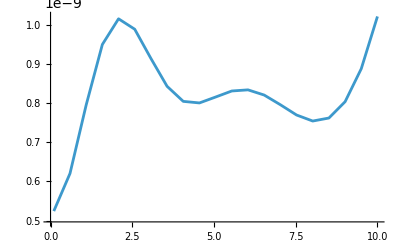

```mathematica
ListLinePlot[Table[{ω,Det[fisherMatrix[ω,0.4,1,10]+Sum[fisherMatrix[ωp,0.4,1,10],{ωp,{0.1,5,10,2,7}}]]},{ω,0.1,10,(10-0.1)/20}]]
```

### Lambda system

#### Exact solution

```mathematica
solLambda={p1[t],p2[t],p3[t]}/.DSolve[{p1'[t]==Γ31*p3[t]-Γ13*p1[t],p2'[t]==Γ32*p3[t]-Γ23*p2[t],p3'[t]==-(Γ31+Γ32)*p3[t]+Γ13*p1[t]+Γ23*p2[t],p1[0]==p1init,p2[0]==p2init,p3[0]==p3init}, {p1,p2,p3},t][[1]]//Simplify
```

```mathematica
{p1[t],p2[t],p3[t]}/.DSolve[{p1'[t]==Γ31*p3[t]-Γ13*p1[t],p2'[t]==Γ32*p3[t]-Γ23*p2[t],p3'[t]==-(Γ31+Γ32)*p3[t]+Γ13*p1[t]+Γ23*p2[t],p1[0]==p1init,p2[0]==p2init,p3[0]==p3init}, {p1,p2,p3},t][[1]]//Tr//Simplify
```

p1init+p2init+p3init

#### Populations and MLE

```mathematica
?steadystate3
?evolution3
```

```mathematica
rϵ=RandomReal[{},3]//Sort;
{rT,rTp}={(rϵ[[3]]-rϵ[[1]]),100(rϵ[[3]]-rϵ[[2]])}//Sort;
init=steadystate3[rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rTp,rTp,0,10^-3,10^2];
(*init=randomPureDensityMatrix[3];*)
nα=0.01;

sol[time_]=evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα,10^-3,10^2]/.t->time;
sol0[time_]=evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,0,10^-3,10^2]/.t->time;
```

```mathematica
r𝒫ness=ReverseSort[Diagonal[steadystate3[rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]]]
r𝒫eq=ReverseSort[Diagonal[steadystate3[rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,0]]]
```

{0.558269,0.236355,0.205376}

{0.555466,0.240189,0.204345}

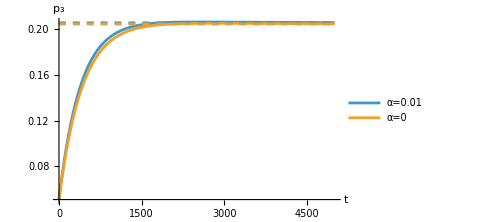
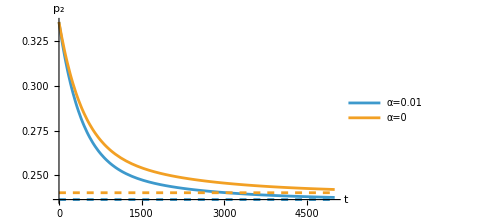
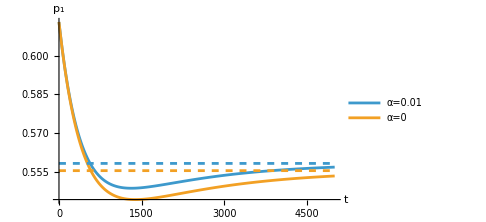

```mathematica
{Plot[{sol[t][[1,1]],sol0[t][[1,1]],r𝒫ness[[3]],r𝒫eq[[3]]},{t,0,5*10^3},PlotRange->All,PlotLegends->{StringForm["α=``",nα],"α=0"},PlotStyle->{defaultPlotColors[[1]],defaultPlotColors[[2]],{defaultPlotColors[[1]],Dashed},{defaultPlotColors[[2]],Dashed}},AxesLabel->{"t","p_3"},ImageSize->Medium],

Plot[{sol[t][[2,2]],sol0[t][[2,2]],r𝒫ness[[2]],r𝒫eq[[2]]},{t,0,5*10^3},PlotRange->All,PlotLegends->{StringForm["α=``",nα],"α=0"},PlotStyle->{defaultPlotColors[[1]],defaultPlotColors[[2]],{defaultPlotColors[[1]],Dashed},{defaultPlotColors[[2]],Dashed}},AxesLabel->{"t","p_2"},ImageSize->Medium],

Plot[{sol[t][[3,3]],sol0[t][[3,3]],r𝒫ness[[1]],r𝒫eq[[1]]},{t,0,5*10^3},PlotRange->All,PlotLegends->{StringForm["α=``",nα],"α=0"},PlotStyle->{defaultPlotColors[[1]],defaultPlotColors[[2]],{defaultPlotColors[[1]],Dashed},{defaultPlotColors[[2]],Dashed}},AxesLabel->{"t","p_1"},ImageSize->Medium]}
```

```mathematica
teff=Teff[rϵ[[3]]-rϵ[[2]],rT,rTp,0.01];
```

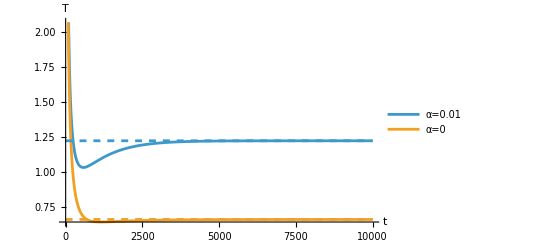

```mathematica
Show[Plot[{-(rϵ[[3]]-rϵ[[2]])/Log[(sol[t][[1,1]])/(sol[t][[2,2]])],-(rϵ[[3]]-rϵ[[2]])/Log[(sol0[t][[1,1]])/(sol0[t][[2,2]])]},{t,0,10^4},PlotRange->Automatic,PlotLegends->{"α=0.01","α=0"}],Plot[{teff,rT},{t,0,10^4},PlotRange->All,PlotStyle->Dashed],AxesLabel->{"t","T"}]
```

```mathematica
r𝒩=10^5;
nness2=measurementsn[r𝒩,r𝒫ness,3]
neq2=measurementsn[r𝒩,r𝒫eq,3]
```

{52088,28717,19140}

{47906,34826,17811}

```mathematica
teff=Teff[rϵ[[3]]-rϵ[[2]],rT,rTp,0.01];

{mle[nness2,rϵ],teff}
{mle[neq2,rϵ],rT}
```

{0.667392,1.05029}

{0.734475,0.692264}

```mathematica
rϵ=RandomReal[{},3]//Sort;
{rT,rTp}={(rϵ[[3]]-rϵ[[1]]),100(rϵ[[3]]-rϵ[[2]])}//Sort;
init=steadystate3[rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rTp,rTp,10^-3,10^2];
(*init=randomPureDensityMatrix[3];*)
init=({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}});
nα=0.01;

sol[time_]=evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα,10^-3,10^2]/.t->time;
sol0[time_]=evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,0,10^-3,10^2]/.t->time;
```

```mathematica
r𝒩=10^4;
nsol[t_]:=measurementsn[r𝒩,ReverseSort[Diagonal[sol[t]]],3]
nsol0[t_]:=measurementsn[r𝒩,ReverseSort[Diagonal[sol0[t]]],3]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ListLinePlot::ioproc: {{0,θ/.{}⟦1⟧},{1000.,0.145472},{2000.,0.233506},{3000.,0.260325},{4000.,0.310521},{5000.,0.321578},{6000.,0.332709},{7000.,0.330181},{8000.,0.334665},{9000.,0.345761},{10000.,0.343441}} may contain non-machine-precision numbers, complex numbers, or invalid entries.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ListLinePlot::ioproc: {{0,θ/.{}⟦1⟧},{1000.,0.132964},{2000.,0.22942},{3000.,0.270223},{4000.,0.29686},{5000.,0.321955},{6000.,0.335712},{7000.,0.33794},{8000.,0.354526},{9000.,0.337656},{10000.,0.363303}} may contain non-machine-precision numbers, complex numbers, or invalid entries.

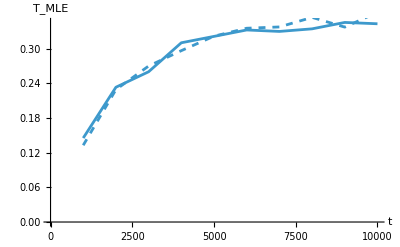

```mathematica
teff=Teff[rϵ[[3]]-rϵ[[2]],rT,rTp,0.01];
tmax=10^4;
points=10;

Show[ListLinePlot[ParallelTable[{t,Quiet@mle[nsol[t],rϵ]},{t,0,tmax,tmax/points}],AxesLabel->{"t","T_MLE"},InterpolationOrder->2,PlotRange->Automatic,GridLines->{{},{{rT,Directive[Thick,Black]},{rTp,Directive[Thick,Red]},{teff,Directive[Thick,Cyan]}}}],
ListLinePlot[ParallelTable[{t,Quiet@mle[nsol0[t],rϵ]},{t,0,tmax,tmax/points}],InterpolationOrder->2,PlotRange->All,PlotStyle->Dashed]]
```

```mathematica
{rT,rTp,teff}
```

{0.310338,4.64237,0.353294}

#### KL divergence

```mathematica
{ρ00,ρ11,ρ22}={({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}}),({{0, 0, 0}, {0, 1, 0}, {0, 0, 0}}),({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}})};
rϵ=RandomReal[{},3]//Sort;
{rT,rTp}={(rϵ[[3]]-rϵ[[1]]),100(rϵ[[3]]-rϵ[[2]])}//Sort;
init=steadystate3[rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rTp,rTp,0,10^-3,10^2];
(*init=randomPure*DensityMatrix[3];*)
nα=0.01;

sol[time_]=evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα,10^-3,10^2]/.t->time;
sol0[time_]=evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,0,10^-3,10^2]/.t->time;
```

```mathematica
init//MatrixForm
```

(0.330555 | 0 | 0
0 | 0.333877 | 0
0 | 0 | 0.335568)

```mathematica
evolution3[ρ00,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]
```

{{0.190249 ⅇ^(-0.00283598 t) (-0.543076 ⅇ^(0.000437673 t)-0.456924 ⅇ^(0.00239831 t)+1. ⅇ^(0.00283598 t)),0,0},{0,0.292601 ⅇ^(-0.00283598 t) (0.22323 ⅇ^(0.000437673 t)-1.22323 ⅇ^(0.00239831 t)+1. ⅇ^(0.00283598 t)),0},{0,0,0.51715 ⅇ^(-0.00283598 t) (0.0734839 ⅇ^(0.000437673 t)+0.860192 ⅇ^(0.00239831 t)+1. ⅇ^(0.00283598 t))}}

```mathematica
?evolution3
```

```mathematica
Pness3[time_]:={
Diagonal[evolution3[init[[1,1]] ρ22,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]],
Diagonal[evolution3[init[[2,2]] ρ11,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]],
Diagonal[evolution3[init[[3,3]] ρ00,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]]}/.t->time;

Peq3[time_,θ_]:={
Diagonal[evolution3[init[[1,1]] ρ22,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],θ,rTp,0]],
Diagonal[evolution3[init[[2,2]] ρ11,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],θ,rTp,0]],
Diagonal[evolution3[init[[3,3]] ρ00,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],θ,rTp,0]]}/.t->time;
f3[t_,θ_]:=dKL[Pness3[t],Peq3[t,θ]];
```

```mathematica
evolution3[init[[1,1]] ρ22,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]
```

{{0.0634493 ⅇ^(-0.00619652 t) (3.98408 ⅇ^(0.000984493 t)+0.225674 ⅇ^(0.00521202 t)+1. ⅇ^(0.00619652 t)),0,0},{0,0.0946327 ⅇ^(-0.00619652 t) (-1.64045 ⅇ^(0.000984493 t)+0.640452 ⅇ^(0.00521202 t)+1. ⅇ^(0.00619652 t)),0},{0,0,0.172473 ⅇ^(-0.00619652 t) (-0.565575 ⅇ^(0.000984493 t)-0.434425 ⅇ^(0.00521202 t)+1. ⅇ^(0.00619652 t))}}

```mathematica
teff=Teff[rϵ[[3]]-rϵ[[2]],rT,rTp,0.01];
{rT,rTp,teff}
```

{0.358549,30.8415,0.6702}

```mathematica
rT+nα*(rTp-rT)
```

0.92096

```mathematica
Tmin=rT/4;
Tmax=5*rT;

tmin=0.1;
tmax=10^5;
points=10;
θest3=ParallelTable[{time,Quiet@First@First@SortBy[Table[{T,f3[time,T]},{T,Tmin,Tmax,(Tmax-Tmin)/points}],Last]},{time,tmin,tmax,(tmax-tmin)/points}];
```

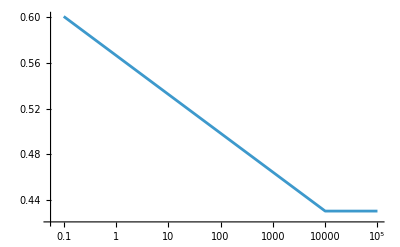

```mathematica
Show[ListLogLinearPlot[θest3,PlotRange->All,Joined->True,InterpolationOrder->1]]
```

```mathematica
teff=Teff[rϵ[[3]]-rϵ[[2]],rT,rTp,0.01];
{rT,rTp,teff}
```

{0.358549,30.8415,0.6702}

```mathematica
{ρ00,ρ11,ρ22}={({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}}),({{0, 0, 0}, {0, 1, 0}, {0, 0, 0}}),({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}})};
rϵ=RandomReal[{},3]//Sort;
{rT,rTp}={(rϵ[[3]]-rϵ[[1]]),100(rϵ[[3]]-rϵ[[2]])}//Sort;
init=steadystate3[rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rTp,rTp,0,10^-3,10^2];
(*init=randomPureDensityMatrix[3];*)
nα=0.01;

sol[time_]=evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα,10^-3,10^2]/.t->time;
sol0[time_]=evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,0,10^-3,10^2]/.t->time;
```

```mathematica
Pness3test[time_]:={
Diagonal[evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]],
Diagonal[evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]],
Diagonal[evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]]}/.t->time;

Peq3test[time_,θ_]:={
Diagonal[evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],θ,rTp,0]],
Diagonal[evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],θ,rTp,0]],
Diagonal[evolution3[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],θ,rTp,0]]}/.t->time;
f3test[t_,θ_]:=dKL[Pness3test[t],Peq3test[t,θ]];
```

```mathematica
Tmin=rT/4;
Tmax=4*rT;
points=20;

tmin=0.1;
tmax=10^4;
θest3=ParallelTable[{time,First@First@SortBy[Table[{T,f3test[time,T]},{T,Tmin,Tmax,(Tmax-Tmin)/points}],Last]},{time,tmin,tmax,(tmax-tmin)/points}];
```

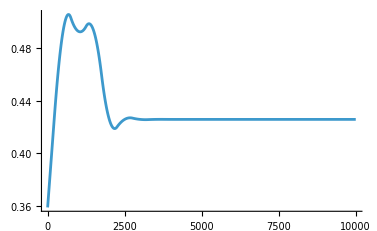

```mathematica
ListPlot[θest3,PlotRange->All,Joined->True,InterpolationOrder->2]
```

```mathematica
teff=Teff[rϵ[[3]]-rϵ[[2]],rT,rTp,0.01];
{rT,rTp,teff}
```

{0.358549,30.8415,0.6702}

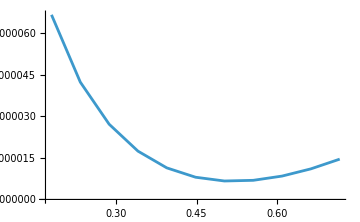
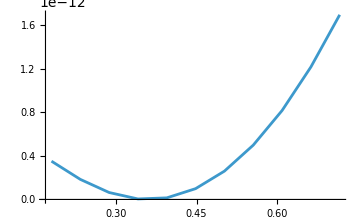

```mathematica
Tmin=rT/2;
Tmax=2*rT;
points=10;

f3Table=Table[{T,f3[0.1,T]},{T,Tmin,Tmax,(Tmax-Tmin)/points}];
f3testTable=Table[{T,f3test[0.1,T]},{T,Tmin,Tmax,(Tmax-Tmin)/points}];
{ListLinePlot[f3Table,ImageSize->Medium],ListLinePlot[f3testTable,ImageSize->Medium]}
```

```mathematica
tmin=0.1;
tmax=10^4;

θest=ParallelTable[{ⅇ^time,θ/.NMinimize[{Chop[f3test[ⅇ^time,θ]],rT/2<θ<2*rT},θ][[2]]},{time,Log[tmin],Log[tmax],(Log[tmax]-Log[tmin])/10}];
```

$Aborted

```mathematica
NMinimize[{Chop[f3test[100,θ]],rT/2<θ<2*rT},θ,WorkingPrecision->5]
```

$Aborted

```mathematica
Show[ListLogLinearPlot[θest,PlotRange->All,Joined->True,InterpolationOrder->2,AxesLabel->{"t","θest"}]]
```

#### KL divergence Full parasite

```mathematica
evolution3FullParasite[init_,ω13_,ω23_,T_,Tp_,α_,γ_:10^-3,Λ_:10^2,kb_:1,ℏ_:1]:=
Module[
{Ω13,Ω23,ρ,ϱ,solution,ℒ},
Ω13={ω13,-ω13};
Ω23={ω23,-ω23};
ϱ=Table[ϱ0[i,j],{i,3},{j,3}];
ρ[t_]=Table[ϱ0[i,j][t],{i,3},{j,3}];
ℒ[X_]:=-ⅈ comm[H3[ℏ ω13,ℏ ω23],X,-1]+Sum[(Γ[Ω23[[i]],T,γ,Λ]+α Γ[Ω23[[i]],Tp,γ,Λ])(A23[[i]].X.A23[[i]]†-1/2 comm[A23[[i]]†.A23[[i]],X,1]),{i,2}]+Sum[(Γ[Ω13[[i]],T,γ,Λ]+α Γ[Ω13[[i]],Tp,γ,Λ])(A13[[i]].X.A13[[i]]†-1/2 comm[A13[[i]]†.A13[[i]],X,1]),{i,2}];
solution=DSolve[Join[Flatten[Table[ρ'[t][[i,j]]==ℒ[ρ[t]][[i,j]],{i,3},{j,3}]]//Chop,Flatten[Table[ρ[0][[i,j]]==init[[i,j]],{i,3},{j,3}]]//Chop],Flatten[ϱ],t];
Return[ρ[t]/.solution⟦1⟧]
]
evolution3FullParasite::usage="evolution3FullParasite[init,ω13,ω23,T,Tp,α,γ,Λ,kb,ℏ] returns the dynamics of a three-level λ-system on two baths (one parasitic with coupling strength attenuated by a factor α and at temperature Tp)";
```

```mathematica
{ρ00,ρ11,ρ22}={({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}}),({{0, 0, 0}, {0, 1, 0}, {0, 0, 0}}),({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}})};
rϵ=RandomReal[{},3]//Sort;
{rT,rTp}={(rϵ[[3]]-rϵ[[1]]),100(rϵ[[3]]-rϵ[[2]])}//Sort;
init=steadystate3[rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rTp,rTp,0,10^-3,10^2];
(*init=randomPure*DensityMatrix[3];*)
nα=0.01;

sol[time_]=evolution3FullParasite[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα,10^-3,10^2]/.t->time;
sol0[time_]=evolution3FullParasite[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,0,10^-3,10^2]/.t->time;
```

```mathematica
init//MatrixForm
```

(0.330555 | 0 | 0
0 | 0.333877 | 0
0 | 0 | 0.335568)

```mathematica
Pness3FullParasite[time_]:={
Diagonal[evolution3FullParasite[init[[1,1]] ρ22,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]],
Diagonal[evolution3FullParasite[init[[2,2]] ρ11,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]],
Diagonal[evolution3FullParasite[init[[3,3]] ρ00,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]]}/.t->time;

Peq3FullParasite[time_,θ_]:={
Diagonal[evolution3FullParasite[init[[1,1]] ρ22,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],θ,rTp,0]],
Diagonal[evolution3FullParasite[init[[2,2]] ρ11,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],θ,rTp,0]],
Diagonal[evolution3FullParasite[init[[3,3]] ρ00,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],θ,rTp,0]]}/.t->time;
f3FullParasite[t_,θ_]:=dKL[Pness3FullParasite[t],Peq3FullParasite[t,θ]];
```

```mathematica
Tmin=rT/4;
Tmax=5*rT;

tmin=0.1;
tmax=10^5;
points=10;
θest3=ParallelTable[{time,Quiet@First@First@SortBy[Table[{T,f3FullParasite[time,T]},{T,Tmin,Tmax,(Tmax-Tmin)/points}],Last]},{time,tmin,tmax,(tmax-tmin)/points}];
```

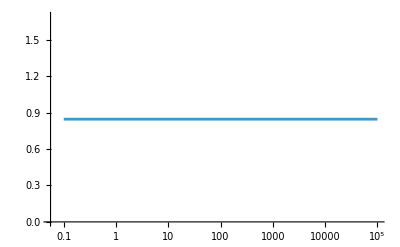

```mathematica
Show[ListLogLinearPlot[θest3,PlotRange->All,Joined->True,InterpolationOrder->1]]
```

```mathematica
θest3
```

{{0.1,0.846667},{10000.1,0.846667},{20000.1,0.846667},{30000.1,0.846667},{40000.1,0.846667},{50000.,0.846667},{60000.,0.846667},{70000.,0.846667},{80000.,0.846667},{90000.,0.846667},{100000.,0.846667}}

```mathematica
teff=Teff[rϵ[[3]]-rϵ[[2]],rT,rTp,0.01];
{rT,rTp,teff}
```

{0.705556,18.1017,0.878518}

```mathematica
Pness3testFullParasite[time_]:={
Diagonal[evolution3FullParasite[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]],
Diagonal[evolution3FullParasite[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]],
Diagonal[evolution3FullParasite[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],rT,rTp,nα]]}/.t->time;

Peq3testFullParasite[time_,θ_]:={
Diagonal[evolution3FullParasite[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],θ,rTp,0]],
Diagonal[evolution3FullParasite[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],θ,rTp,0]],
Diagonal[evolution3FullParasite[init,rϵ[[3]]-rϵ[[1]],rϵ[[3]]-rϵ[[2]],θ,rTp,0]]}/.t->time;
f3testFullParasite[t_,θ_]:=dKL[Pness3testFullParasite[t],Peq3testFullParasite[t,θ]];
```

```mathematica
Tmin=rT/4;
Tmax=4*rT;
points=20;

tmin=0.1;
tmax=10^4;
θest3=ParallelTable[{time,First@First@SortBy[Table[{T,f3testFullParasite[time,T]},{T,Tmin,Tmax,(Tmax-Tmin)/points}],Last]},{time,tmin,tmax,(tmax-tmin)/points}];
```

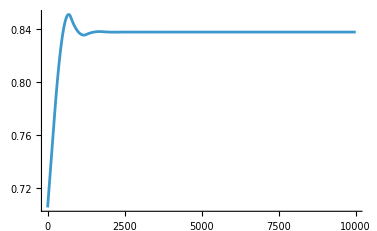

```mathematica
ListPlot[θest3,PlotRange->All,Joined->True,InterpolationOrder->2]
```

```mathematica
teff=Teff[rϵ[[3]]-rϵ[[2]],rT,rTp,0.01];
{rT,rTp,teff}
teff=Teff[rϵ[[3]]-rϵ[[1]],rT,rTp,0.01]
```

{0.705556,18.1017,0.878518}

0.888898

```mathematica
Tmin=rT/2;
Tmax=2*rT;
points=10;

f3Table=Table[{T,f3[0.1,T]},{T,Tmin,Tmax,(Tmax-Tmin)/points}];
f3testTable=Table[{T,f3test[0.1,T]},{T,Tmin,Tmax,(Tmax-Tmin)/points}];
{ListLinePlot[f3Table,ImageSize->Medium],ListLinePlot[f3testTable,ImageSize->Medium]}
```

{-Graphics-,-Graphics-}

```mathematica
tmin=0.1;
tmax=10^4;

θest=ParallelTable[{ⅇ^time,θ/.NMinimize[{Chop[f3test[ⅇ^time,θ]],rT/2<θ<2*rT},θ][[2]]},{time,Log[tmin],Log[tmax],(Log[tmax]-Log[tmin])/10}];
```

$Aborted

```mathematica
NMinimize[{Chop[f3test[100,θ]],rT/2<θ<2*rT},θ,WorkingPrecision->5]
```

$Aborted

```mathematica
Show[ListLogLinearPlot[θest,PlotRange->All,Joined->True,InterpolationOrder->2,AxesLabel->{"t","θest"}]]
```